```mathematica
Clear["Global`*"]
```

## Ranft et al. model - numerical simulations

### Saved parameters

Good results for

```mathematica
params = {Λ -> 1, β -> 0, V0 -> 1, ϵ -> 0.1};
tmax =5; L= 20;
(* Method 2, scheme 1*)
Nx=50;
T= 20;
```

### Initialization (fixed parameters throughout script)

```mathematica
(* Parameters *)
params = {Λ -> 1, β -> 0, V0 -> 1, ϵ -> 0.1};
(* Domain *)
tmax =5; L= 20;(* L = tmax*(2+V0)+50 /. params;*)
```

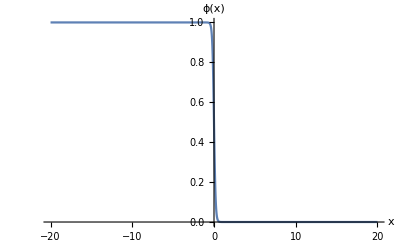

ϕ^(0,1)[x,t]+V[x,t] ϕ^(1,0)[x,t]==(1-ϕ[x,t]) ϕ[x,t]+ϕ^(2,0)[x,t]
-V[x,t]+V^(2,0)[x,t]==2 ϕ^(1,0)[x,t]

```mathematica
(* Initial value data *)
ϕ0[x_]:= 1/(1+Exp[(x)/ϵ]);
pde={D[ϕ[x,t], t] + V[x,t] D[ϕ[x,t], x]== D[ϕ[x,t],{x, 2}] + ϕ[x,t](1-ϕ[x,t]),  Λ^2 D[V[x,t],{x, 2}]-V[x,t] == 2Λ V0 D[ϕ[x,t], x](1+β D[ϕ[x,t],{x, 2}] ) } /. params;
Plot[ ϕ0[x]/.params, {x,-L, L}, AxesLabel->{"x", "ϕ(x)"}]
pde//TableForm
```

## Algebraically solve finite difference equations

Mesh [x_i, t_m] with 0≤ i ≤ N for space, 0 ≤ m≤ M for time
Write ϕ_(i,m) = ϕ[x_i,t_m]
Replace derivatives:
ϕ^(1,0)[x_i,t_m]= (ϕ_(i+1,m)-ϕ_(i-1,m))/(2 Δx) 
ϕ^(0,1)[x_i,t_m]= (ϕ_(i,m+1)-ϕ_(i,m))/Δt
ϕ^(2,0)[x_i,t_m]= (ϕ_(i+1,m)- 2 ϕ_(i,m) + ϕ_(i-1,m))/(Δx)^2

Boundary conditions (for ϕ, same for V)
(1) Dirichlet
ϕ(-L,t)=ϕ_L, ϕ(L,t)=ϕ_R
ϕ_(1,m) =ϕ_L, ϕ_(N,m) =ϕ_R
(2) Neumann
ϕ^(1,0)(-L,t)=f_L(t), ϕ^(1,0)(L,t)=f_R(t)
(ϕ_(1,m))^(1,0)= (ϕ_(2,m)-ϕ_(0,m))/Δx →  Replace ϕ_(-1,m)=ϕ_(1,m)-2Δx f_(L,m), ϕ_(N+1, m)=ϕ_(N-1,m)+2Δx f_(L,m)
Initial conditions
ϕ_(i,0) =ϕ[x_i,0]

### Analytic solution

#### Define mesh, BCs and IVs

```mathematica
Nx = 10; (* number of mesh points *)
T= 20; (* number of time steps *)
ΔxSet = 2L/(Nx);
ΔtSet = tmax/T;
xmesh= Range[-L, L, ΔxSet];
tmesh =Range[0, tmax, tmax/T];
Print[xmesh[[Nx/2+1]]];(* should be equal to zero*)
```

0

```mathematica
(*Dirichlet Boundaries*)
ϕL = 1; ϕR = 0;
VL = 0; VR = 0;
bcϕ={Subscript[ϕ, 0,m]==ϕL,Subscript[ϕ, Nx,m]==ϕR};
bcV={Subscript[V, 0,m]==VL,Subscript[V, Nx,m]==VR};

(*initial conditions *)
(*ϕ0Set=Table[Boole[(i<Nx/2)], {i, 0, Nx}];*)
ϕ0Set=Table[ ϕ0[xmesh[[i]] ], {i, 0, Nx}] /. params;
```

General::munfl: Exp[-1000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-800.] is too small to represent as a normalized machine number; precision may be lost.

#### Discretized form of PDE

```mathematica
FDrules = {ϕ[x,t]-> Subscript[ϕ, i,m],Derivative[1,0][ϕ][x,t]-> (Subscript[ϕ, i+1,m]-Subscript[ϕ, i-1,m])/(2 Δx), Derivative[0,1][ϕ][x,t]->  (Subscript[ϕ, i,m+1]-Subscript[ϕ, i,m])/Δt,Derivative[2,0][ϕ][x,t]-> (Subscript[ϕ, i+1,m]- 2 Subscript[ϕ, i,m] + Subscript[ϕ, i-1,m])/(Δx)^2,V[x,t]-> Subscript[V, i,m], Derivative[2,0][V][x,t]-> (Subscript[V, i+1,m]- 2 Subscript[V, i,m] + Subscript[V, i-1,m])/(Δx)^2};pde2={D[ϕ[x,t], t] + V[x,t] D[ϕ[x,t], x]- D[ϕ[x,t],{x, 2}] - ϕ[x,t](1-ϕ[x,t])==0,  Λ^2 D[V[x,t],{x, 2}]-V[x,t] - 2Λ V0 D[ϕ[x,t], x](1+β D[ϕ[x,t],{x, 2}] ) ==0 };
pdeDiscretized =pde2 /.FDrules
```

{-(1-ϕ_(i,m)) ϕ_(i,m)+(-ϕ_(i,m)+ϕ_(i,1+m))/Δt+(V_(i,m) (-ϕ_(-1+i,m)+ϕ_(1+i,m)))/(2 Δx)-(ϕ_(-1+i,m)-2 ϕ_(i,m)+ϕ_(1+i,m))/Δx^2==0,-V_(i,m)+(Λ^2 (V_(-1+i,m)-2 V_(i,m)+V_(1+i,m)))/Δx^2-(V0 Λ (-ϕ_(-1+i,m)+ϕ_(1+i,m)) (1+(β (ϕ_(-1+i,m)-2 ϕ_(i,m)+ϕ_(1+i,m)))/Δx^2))/Δx==0}

#### Explicit analytic solution of V_(i,m) given ϕ_(i,m)

```mathematica
pdeDiscretized[[2]] (*Discretized equation Subscript[V, i,m], linear and can be solved*)
```

-V_(i,m)+(Λ^2 (V_(-1+i,m)-2 V_(i,m)+V_(1+i,m)))/Δx^2-(V0 Λ (-ϕ_(-1+i,m)+ϕ_(1+i,m)) (1+(β (ϕ_(-1+i,m)-2 ϕ_(i,m)+ϕ_(1+i,m)))/Δx^2))/Δx==0

```mathematica
Vlist=Table[Subscript[V, i,m], {i,0,Nx}];
condsAll=Join[bcV, Table[  pdeDiscretized[[2]]/. { Λ^2/Δx^2-> s, (V0 Λ (-Subscript[ϕ, -1+i,m]+Subscript[ϕ, 1+i,m]) (1+(β (Subscript[ϕ, -1+i,m]-2 Subscript[ϕ, i,m]+Subscript[ϕ, 1+i,m]))/Δx^2))/Δx-> -Subscript[B, i,m]} , {i,1,Nx-1}]];
VDiscSol=First[Solve[condsAll, Vlist] // Simplify]
```

{V_(0,m)→0,V_(1,m)→((1+16 s+105 s^2+364 s^3+715 s^4+792 s^5+462 s^6+120 s^7+9 s^8) B_(1,m)+s ((1+14 s+78 s^2+220 s^3+330 s^4+252 s^5+84 s^6+8 s^7) B_(2,m)+s ((1+12 s+55 s^2+120 s^3+126 s^4+56 s^5+7 s^6) B_(3,m)+s ((1+10 s+36 s^2+56 s^3+35 s^4+6 s^5) B_(4,m)+s ((1+8 s+21 s^2+20 s^3+5 s^4) B_(5,m)+s ((1+6 s+10 s^2+4 s^3) B_(6,m)+s ((1+4 s+3 s^2) B_(7,m)+s ((1+2 s) B_(8,m)+s B_(9,m)))))))))/((1+2 s) (1+16 s+104 s^2+352 s^3+661 s^4+680 s^5+356 s^6+80 s^7+5 s^8)),V_(2,m)→(s (1+12 s+54 s^2+112 s^3+106 s^4+40 s^5+4 s^6) B_(1,m)+(1+14 s+78 s^2+220 s^3+330 s^4+252 s^5+84 s^6+8 s^7) B_(2,m)+s ((1+12 s+55 s^2+120 s^3+126 s^4+56 s^5+7 s^6) B_(3,m)+s ((1+10 s+36 s^2+56 s^3+35 s^4+6 s^5) B_(4,m)+s ((1+8 s+21 s^2+20 s^3+5 s^4) B_(5,m)+s ((1+6 s+10 s^2+4 s^3) B_(6,m)+s ((1+4 s+3 s^2) B_(7,m)+s ((1+2 s) B_(8,m)+s B_(9,m))))))))/(1+16 s+104 s^2+352 s^3+661 s^4+680 s^5+356 s^6+80 s^7+5 s^8),V_(3,m)→(s^2 (1+12 s+55 s^2+120 s^3+126 s^4+56 s^5+7 s^6) B_(1,m)+s (1+14 s+79 s^2+230 s^3+366 s^4+308 s^5+119 s^6+14 s^7) B_(2,m)+(1+4 s+3 s^2) ((1+12 s+55 s^2+120 s^3+126 s^4+56 s^5+7 s^6) B_(3,m)+s ((1+10 s+36 s^2+56 s^3+35 s^4+6 s^5) B_(4,m)+s ((1+8 s+21 s^2+20 s^3+5 s^4) B_(5,m)+s ((1+6 s+10 s^2+4 s^3) B_(6,m)+s ((1+4 s+3 s^2) B_(7,m)+s ((1+2 s) B_(8,m)+s B_(9,m))))))))/((1+2 s) (1+16 s+104 s^2+352 s^3+661 s^4+680 s^5+356 s^6+80 s^7+5 s^8)),V_(4,m)→(s^3 (1+8 s+20 s^2+16 s^3+3 s^4) B_(1,m)+s^2 (1+10 s+36 s^2+56 s^3+35 s^4+6 s^5) B_(2,m)+s B_(3,m)+12 s^2 B_(3,m)+55 s^3 B_(3,m)+120 s^4 B_(3,m)+127 s^5 B_(3,m)+60 s^6 B_(3,m)+9 s^7 B_(3,m)+B_(4,m)+14 s B_(4,m)+78 s^2 B_(4,m)+220 s^3 B_(4,m)+331 s^4 B_(4,m)+258 s^5 B_(4,m)+94 s^6 B_(4,m)+12 s^7 B_(4,m)+s B_(5,m)+12 s^2 B_(5,m)+55 s^3 B_(5,m)+120 s^4 B_(5,m)+127 s^5 B_(5,m)+60 s^6 B_(5,m)+10 s^7 B_(5,m)+s^2 B_(6,m)+10 s^3 B_(6,m)+36 s^4 B_(6,m)+56 s^5 B_(6,m)+36 s^6 B_(6,m)+8 s^7 B_(6,m)+s^3 B_(7,m)+8 s^4 B_(7,m)+21 s^5 B_(7,m)+20 s^6 B_(7,m)+6 s^7 B_(7,m)+s^4 B_(8,m)+6 s^5 B_(8,m)+10 s^6 B_(8,m)+4 s^7 B_(8,m)+s^5 B_(9,m)+4 s^6 B_(9,m)+2 s^7 B_(9,m))/(1+16 s+104 s^2+352 s^3+661 s^4+680 s^5+356 s^6+80 s^7+5 s^8),V_(5,m)→1/((1+2 s) (1+8 s+19 s^2+12 s^3+s^4))(s^4 B_(1,m)+s^3 (1+2 s) B_(2,m)+s^2 B_(3,m)+4 s^3 B_(3,m)+3 s^4 B_(3,m)+s B_(4,m)+6 s^2 B_(4,m)+10 s^3 B_(4,m)+4 s^4 B_(4,m)+B_(5,m)+8 s B_(5,m)+21 s^2 B_(5,m)+20 s^3 B_(5,m)+5 s^4 B_(5,m)+s B_(6,m)+6 s^2 B_(6,m)+10 s^3 B_(6,m)+4 s^4 B_(6,m)+s^2 B_(7,m)+4 s^3 B_(7,m)+3 s^4 B_(7,m)+s^3 B_(8,m)+2 s^4 B_(8,m)+s^4 B_(9,m)),V_(6,m)→(s^5 (1+4 s+2 s^2) B_(1,m)+s^4 (1+6 s+10 s^2+4 s^3) B_(2,m)+s^3 B_(3,m)+8 s^4 B_(3,m)+21 s^5 B_(3,m)+20 s^6 B_(3,m)+6 s^7 B_(3,m)+s^2 B_(4,m)+10 s^3 B_(4,m)+36 s^4 B_(4,m)+56 s^5 B_(4,m)+36 s^6 B_(4,m)+8 s^7 B_(4,m)+s B_(5,m)+12 s^2 B_(5,m)+55 s^3 B_(5,m)+120 s^4 B_(5,m)+127 s^5 B_(5,m)+60 s^6 B_(5,m)+10 s^7 B_(5,m)+B_(6,m)+14 s B_(6,m)+78 s^2 B_(6,m)+220 s^3 B_(6,m)+331 s^4 B_(6,m)+258 s^5 B_(6,m)+94 s^6 B_(6,m)+12 s^7 B_(6,m)+s B_(7,m)+12 s^2 B_(7,m)+55 s^3 B_(7,m)+120 s^4 B_(7,m)+127 s^5 B_(7,m)+60 s^6 B_(7,m)+9 s^7 B_(7,m)+s^2 B_(8,m)+10 s^3 B_(8,m)+36 s^4 B_(8,m)+56 s^5 B_(8,m)+35 s^6 B_(8,m)+6 s^7 B_(8,m)+s^3 B_(9,m)+8 s^4 B_(9,m)+20 s^5 B_(9,m)+16 s^6 B_(9,m)+3 s^7 B_(9,m))/(1+16 s+104 s^2+352 s^3+661 s^4+680 s^5+356 s^6+80 s^7+5 s^8),V_(7,m)→(s^6 (1+4 s+3 s^2) B_(1,m)+s^5 (1+6 s+11 s^2+6 s^3) B_(2,m)+s^4 B_(3,m)+8 s^5 B_(3,m)+22 s^6 B_(3,m)+24 s^7 B_(3,m)+9 s^8 B_(3,m)+s^3 B_(4,m)+10 s^4 B_(4,m)+37 s^5 B_(4,m)+62 s^6 B_(4,m)+46 s^7 B_(4,m)+12 s^8 B_(4,m)+s^2 B_(5,m)+12 s^3 B_(5,m)+56 s^4 B_(5,m)+128 s^5 B_(5,m)+148 s^6 B_(5,m)+80 s^7 B_(5,m)+15 s^8 B_(5,m)+s B_(6,m)+14 s^2 B_(6,m)+79 s^3 B_(6,m)+230 s^4 B_(6,m)+367 s^5 B_(6,m)+314 s^6 B_(6,m)+129 s^7 B_(6,m)+18 s^8 B_(6,m)+B_(7,m)+16 s B_(7,m)+106 s^2 B_(7,m)+376 s^3 B_(7,m)+771 s^4 B_(7,m)+920 s^5 B_(7,m)+609 s^6 B_(7,m)+196 s^7 B_(7,m)+21 s^8 B_(7,m)+s B_(8,m)+14 s^2 B_(8,m)+79 s^3 B_(8,m)+230 s^4 B_(8,m)+366 s^5 B_(8,m)+308 s^6 B_(8,m)+119 s^7 B_(8,m)+14 s^8 B_(8,m)+s^2 B_(9,m)+12 s^3 B_(9,m)+55 s^4 B_(9,m)+120 s^5 B_(9,m)+126 s^6 B_(9,m)+56 s^7 B_(9,m)+7 s^8 B_(9,m))/((1+2 s) (1+16 s+104 s^2+352 s^3+661 s^4+680 s^5+356 s^6+80 s^7+5 s^8)),V_(8,m)→(s^7 B_(1,m)+s^6 (1+2 s) B_(2,m)+s^5 B_(3,m)+4 s^6 B_(3,m)+3 s^7 B_(3,m)+s^4 B_(4,m)+6 s^5 B_(4,m)+10 s^6 B_(4,m)+4 s^7 B_(4,m)+s^3 B_(5,m)+8 s^4 B_(5,m)+21 s^5 B_(5,m)+20 s^6 B_(5,m)+5 s^7 B_(5,m)+s^2 B_(6,m)+10 s^3 B_(6,m)+36 s^4 B_(6,m)+56 s^5 B_(6,m)+35 s^6 B_(6,m)+6 s^7 B_(6,m)+s B_(7,m)+12 s^2 B_(7,m)+55 s^3 B_(7,m)+120 s^4 B_(7,m)+126 s^5 B_(7,m)+56 s^6 B_(7,m)+7 s^7 B_(7,m)+B_(8,m)+14 s B_(8,m)+78 s^2 B_(8,m)+220 s^3 B_(8,m)+330 s^4 B_(8,m)+252 s^5 B_(8,m)+84 s^6 B_(8,m)+8 s^7 B_(8,m)+s B_(9,m)+12 s^2 B_(9,m)+54 s^3 B_(9,m)+112 s^4 B_(9,m)+106 s^5 B_(9,m)+40 s^6 B_(9,m)+4 s^7 B_(9,m))/(1+16 s+104 s^2+352 s^3+661 s^4+680 s^5+356 s^6+80 s^7+5 s^8),V_(9,m)→(s^8 B_(1,m)+s^7 (1+2 s) B_(2,m)+s^6 B_(3,m)+4 s^7 B_(3,m)+3 s^8 B_(3,m)+s^5 B_(4,m)+6 s^6 B_(4,m)+10 s^7 B_(4,m)+4 s^8 B_(4,m)+s^4 B_(5,m)+8 s^5 B_(5,m)+21 s^6 B_(5,m)+20 s^7 B_(5,m)+5 s^8 B_(5,m)+s^3 B_(6,m)+10 s^4 B_(6,m)+36 s^5 B_(6,m)+56 s^6 B_(6,m)+35 s^7 B_(6,m)+6 s^8 B_(6,m)+s^2 B_(7,m)+12 s^3 B_(7,m)+55 s^4 B_(7,m)+120 s^5 B_(7,m)+126 s^6 B_(7,m)+56 s^7 B_(7,m)+7 s^8 B_(7,m)+s B_(8,m)+14 s^2 B_(8,m)+78 s^3 B_(8,m)+220 s^4 B_(8,m)+330 s^5 B_(8,m)+252 s^6 B_(8,m)+84 s^7 B_(8,m)+8 s^8 B_(8,m)+B_(9,m)+16 s B_(9,m)+105 s^2 B_(9,m)+364 s^3 B_(9,m)+715 s^4 B_(9,m)+792 s^5 B_(9,m)+462 s^6 B_(9,m)+120 s^7 B_(9,m)+9 s^8 B_(9,m))/((1+2 s) (1+16 s+104 s^2+352 s^3+661 s^4+680 s^5+356 s^6+80 s^7+5 s^8)),V_(10,m)→0}

Problem: the scheme quickly becomes extremely cumbersome as the mesh size increases.

#### Explicit analytic solution of ϕ_(i,m+1) given ϕ_(i,m) and V_(i,m)

For 1 <= i <= Nx-1:

```mathematica
ϕtDiscSol=First@Solve[{pdeDiscretized[[1]]}, Subscript[ϕ, i,1+m]]
```

{ϕ_(i,1+m)→(2 Δt ϕ_(-1+i,m)+Δt Δx V_(i,m) ϕ_(-1+i,m)-4 Δt ϕ_(i,m)+2 Δx^2 ϕ_(i,m)+2 Δt Δx^2 ϕ_(i,m)-2 Δt Δx^2 ϕ_(i,m)^2+2 Δt ϕ_(1+i,m)-Δt Δx V_(i,m) ϕ_(1+i,m))/(2 Δx^2)}

Boundary conditions:
(1) Dirichlet: set boundary values later
(2) Neumann: define rules for ϕ_(-1,m) and ϕ_(N+1,m). <- Finish this

```mathematica
bcRulesNeumann = {Subscript[ϕ, -1,m]-> Subscript[ϕ, 1,m]-2Δx fL, Subscript[ϕ, Nx+1,m]-> Subscript[ϕ, Nx-1,m]+2Δx fR, Subscript[V, -1,m]-> Subscript[V, 1,m]-2Δx gL, Subscript[V, Nx+1,m]-> Subscript[V, Nx-1,m]+2Δx gR }
```

{ϕ_(-1,m)→-2 fL Δx+ϕ_(1,m),ϕ_(11,m)→2 fR Δx+ϕ_(9,m),V_(-1,m)→-2 gL Δx+V_(1,m),V_(11,m)→2 gR Δx+V_(9,m)}

### Numeric scheme using use algebraic solutions

Use Dirichlet boundaries
ϕ_(0,L)=1, ϕ_(N,L)=0 
V_(0,L)=0, V_(N,L)=0 
Initial conditions
ϕ_(i,0)= 0 if i<N/2, ϕ_(i,0)= 1 if i≥ N/2

```mathematica
(* Initialize values *)
ϕAll=Table[Subscript[ϕ, i,m], {i, 0, Nx}, {m, 0, T}];
VAll=Table[Subscript[V, i,m], {i, 0, Nx}, {m, 0, T}];
ϕAll[[;;, 1]]
```

{ϕ_(0,0),ϕ_(1,0),ϕ_(2,0),ϕ_(3,0),ϕ_(4,0),ϕ_(5,0),ϕ_(6,0),ϕ_(7,0),ϕ_(8,0),ϕ_(9,0),ϕ_(10,0)}

```mathematica
(* set initial values*)
Do[ ϕAll[[i+1, 1]] =ϕ0Set[[i+1]], {i,0,Nx}]; 
ϕAll[[;;, 1]]
```

{1/(1+ⅇ^(10. List)),1.,1.,1.,1.,1.,1/2,1.3839×10^-87,1.91517×10^-174,2.6504×10^-261,3.667874584178×10^-348}

```mathematica
(* set Dirichlet boundary values *)
Do[ϕAll[[1, j+1]] = ϕL, {j, 0, T}]
Do[ϕAll[[Nx+1, j+1]] = ϕR, {j, 0, T}]
Do[VAll[[1, j+1]] = VL, {j, 0, T}]
Do[VAll[[Nx+1, j+1]] = VR, {j, 0, T}]
ϕAll //MatrixForm
VAll //MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
ϕ_(1,0) | ϕ_(1,1) | ϕ_(1,2) | ϕ_(1,3) | ϕ_(1,4) | ϕ_(1,5) | ϕ_(1,6) | ϕ_(1,7) | ϕ_(1,8) | ϕ_(1,9) | ϕ_(1,10) | ϕ_(1,11) | ϕ_(1,12) | ϕ_(1,13) | ϕ_(1,14) | ϕ_(1,15) | ϕ_(1,16) | ϕ_(1,17) | ϕ_(1,18) | ϕ_(1,19) | ϕ_(1,20)
ϕ_(2,0) | ϕ_(2,1) | ϕ_(2,2) | ϕ_(2,3) | ϕ_(2,4) | ϕ_(2,5) | ϕ_(2,6) | ϕ_(2,7) | ϕ_(2,8) | ϕ_(2,9) | ϕ_(2,10) | ϕ_(2,11) | ϕ_(2,12) | ϕ_(2,13) | ϕ_(2,14) | ϕ_(2,15) | ϕ_(2,16) | ϕ_(2,17) | ϕ_(2,18) | ϕ_(2,19) | ϕ_(2,20)
ϕ_(3,0) | ϕ_(3,1) | ϕ_(3,2) | ϕ_(3,3) | ϕ_(3,4) | ϕ_(3,5) | ϕ_(3,6) | ϕ_(3,7) | ϕ_(3,8) | ϕ_(3,9) | ϕ_(3,10) | ϕ_(3,11) | ϕ_(3,12) | ϕ_(3,13) | ϕ_(3,14) | ϕ_(3,15) | ϕ_(3,16) | ϕ_(3,17) | ϕ_(3,18) | ϕ_(3,19) | ϕ_(3,20)
ϕ_(4,0) | ϕ_(4,1) | ϕ_(4,2) | ϕ_(4,3) | ϕ_(4,4) | ϕ_(4,5) | ϕ_(4,6) | ϕ_(4,7) | ϕ_(4,8) | ϕ_(4,9) | ϕ_(4,10) | ϕ_(4,11) | ϕ_(4,12) | ϕ_(4,13) | ϕ_(4,14) | ϕ_(4,15) | ϕ_(4,16) | ϕ_(4,17) | ϕ_(4,18) | ϕ_(4,19) | ϕ_(4,20)
ϕ_(5,0) | ϕ_(5,1) | ϕ_(5,2) | ϕ_(5,3) | ϕ_(5,4) | ϕ_(5,5) | ϕ_(5,6) | ϕ_(5,7) | ϕ_(5,8) | ϕ_(5,9) | ϕ_(5,10) | ϕ_(5,11) | ϕ_(5,12) | ϕ_(5,13) | ϕ_(5,14) | ϕ_(5,15) | ϕ_(5,16) | ϕ_(5,17) | ϕ_(5,18) | ϕ_(5,19) | ϕ_(5,20)
ϕ_(6,0) | ϕ_(6,1) | ϕ_(6,2) | ϕ_(6,3) | ϕ_(6,4) | ϕ_(6,5) | ϕ_(6,6) | ϕ_(6,7) | ϕ_(6,8) | ϕ_(6,9) | ϕ_(6,10) | ϕ_(6,11) | ϕ_(6,12) | ϕ_(6,13) | ϕ_(6,14) | ϕ_(6,15) | ϕ_(6,16) | ϕ_(6,17) | ϕ_(6,18) | ϕ_(6,19) | ϕ_(6,20)
ϕ_(7,0) | ϕ_(7,1) | ϕ_(7,2) | ϕ_(7,3) | ϕ_(7,4) | ϕ_(7,5) | ϕ_(7,6) | ϕ_(7,7) | ϕ_(7,8) | ϕ_(7,9) | ϕ_(7,10) | ϕ_(7,11) | ϕ_(7,12) | ϕ_(7,13) | ϕ_(7,14) | ϕ_(7,15) | ϕ_(7,16) | ϕ_(7,17) | ϕ_(7,18) | ϕ_(7,19) | ϕ_(7,20)
ϕ_(8,0) | ϕ_(8,1) | ϕ_(8,2) | ϕ_(8,3) | ϕ_(8,4) | ϕ_(8,5) | ϕ_(8,6) | ϕ_(8,7) | ϕ_(8,8) | ϕ_(8,9) | ϕ_(8,10) | ϕ_(8,11) | ϕ_(8,12) | ϕ_(8,13) | ϕ_(8,14) | ϕ_(8,15) | ϕ_(8,16) | ϕ_(8,17) | ϕ_(8,18) | ϕ_(8,19) | ϕ_(8,20)
ϕ_(9,0) | ϕ_(9,1) | ϕ_(9,2) | ϕ_(9,3) | ϕ_(9,4) | ϕ_(9,5) | ϕ_(9,6) | ϕ_(9,7) | ϕ_(9,8) | ϕ_(9,9) | ϕ_(9,10) | ϕ_(9,11) | ϕ_(9,12) | ϕ_(9,13) | ϕ_(9,14) | ϕ_(9,15) | ϕ_(9,16) | ϕ_(9,17) | ϕ_(9,18) | ϕ_(9,19) | ϕ_(9,20)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
V_(1,0) | V_(1,1) | V_(1,2) | V_(1,3) | V_(1,4) | V_(1,5) | V_(1,6) | V_(1,7) | V_(1,8) | V_(1,9) | V_(1,10) | V_(1,11) | V_(1,12) | V_(1,13) | V_(1,14) | V_(1,15) | V_(1,16) | V_(1,17) | V_(1,18) | V_(1,19) | V_(1,20)
V_(2,0) | V_(2,1) | V_(2,2) | V_(2,3) | V_(2,4) | V_(2,5) | V_(2,6) | V_(2,7) | V_(2,8) | V_(2,9) | V_(2,10) | V_(2,11) | V_(2,12) | V_(2,13) | V_(2,14) | V_(2,15) | V_(2,16) | V_(2,17) | V_(2,18) | V_(2,19) | V_(2,20)
V_(3,0) | V_(3,1) | V_(3,2) | V_(3,3) | V_(3,4) | V_(3,5) | V_(3,6) | V_(3,7) | V_(3,8) | V_(3,9) | V_(3,10) | V_(3,11) | V_(3,12) | V_(3,13) | V_(3,14) | V_(3,15) | V_(3,16) | V_(3,17) | V_(3,18) | V_(3,19) | V_(3,20)
V_(4,0) | V_(4,1) | V_(4,2) | V_(4,3) | V_(4,4) | V_(4,5) | V_(4,6) | V_(4,7) | V_(4,8) | V_(4,9) | V_(4,10) | V_(4,11) | V_(4,12) | V_(4,13) | V_(4,14) | V_(4,15) | V_(4,16) | V_(4,17) | V_(4,18) | V_(4,19) | V_(4,20)
V_(5,0) | V_(5,1) | V_(5,2) | V_(5,3) | V_(5,4) | V_(5,5) | V_(5,6) | V_(5,7) | V_(5,8) | V_(5,9) | V_(5,10) | V_(5,11) | V_(5,12) | V_(5,13) | V_(5,14) | V_(5,15) | V_(5,16) | V_(5,17) | V_(5,18) | V_(5,19) | V_(5,20)
V_(6,0) | V_(6,1) | V_(6,2) | V_(6,3) | V_(6,4) | V_(6,5) | V_(6,6) | V_(6,7) | V_(6,8) | V_(6,9) | V_(6,10) | V_(6,11) | V_(6,12) | V_(6,13) | V_(6,14) | V_(6,15) | V_(6,16) | V_(6,17) | V_(6,18) | V_(6,19) | V_(6,20)
V_(7,0) | V_(7,1) | V_(7,2) | V_(7,3) | V_(7,4) | V_(7,5) | V_(7,6) | V_(7,7) | V_(7,8) | V_(7,9) | V_(7,10) | V_(7,11) | V_(7,12) | V_(7,13) | V_(7,14) | V_(7,15) | V_(7,16) | V_(7,17) | V_(7,18) | V_(7,19) | V_(7,20)
V_(8,0) | V_(8,1) | V_(8,2) | V_(8,3) | V_(8,4) | V_(8,5) | V_(8,6) | V_(8,7) | V_(8,8) | V_(8,9) | V_(8,10) | V_(8,11) | V_(8,12) | V_(8,13) | V_(8,14) | V_(8,15) | V_(8,16) | V_(8,17) | V_(8,18) | V_(8,19) | V_(8,20)
V_(9,0) | V_(9,1) | V_(9,2) | V_(9,3) | V_(9,4) | V_(9,5) | V_(9,6) | V_(9,7) | V_(9,8) | V_(9,9) | V_(9,10) | V_(9,11) | V_(9,12) | V_(9,13) | V_(9,14) | V_(9,15) | V_(9,16) | V_(9,17) | V_(9,18) | V_(9,19) | V_(9,20)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

#### Explicit analytic updating scheme

Show algebraic results of updating V_(i,m)

```mathematica
thism=2;
rulesBack=With[{Δx = ΔxSet, Δt = ΔtSet}, Join[{s-> Λ^2/Δx^2} ,Table[Subscript[B, i,m]-> (V0 Λ (-Subscript[ϕ, -1+i,m]+Subscript[ϕ, 1+i,m]) (1+(β (Subscript[ϕ, -1+i,m]-2 Subscript[ϕ, i,m]+Subscript[ϕ, 1+i,m]))/Δx^2))/Δx,{i,0,Nx}]] /.params];
ϕReplace=MapThread[#1 -> #2 &,{Table[Subscript[ϕ, i,thism] , {i,0, Nx}], ϕAll[[;;, thism+1]]}];
VReplace=(VDiscSol/.rulesBack /. {m-> thism}/. ϕReplace) (*keep order of replacements!*)
```

{V_(0,2)→0,V_(1,2)→1/27416561018896115078601 26214400000000000000000 ((682008225714761968009 (-1+ϕ_(2,2)))/6553600000000000000000+1/400 ((212068546645044201 (-ϕ_(1,2)+ϕ_(3,2)))/2048000000000000000+1/400 ((4220295700182407 (-ϕ_(2,2)+ϕ_(4,2)))/40960000000000000+1/400 ((5249156487003 (-ϕ_(3,2)+ϕ_(5,2)))/51200000000000+1/400 ((5223073601 (-ϕ_(4,2)+ϕ_(6,2)))/51200000000+1/400 ((16241001 (-ϕ_(5,2)+ϕ_(7,2)))/160000000+1/400 ((161603 (-ϕ_(6,2)+ϕ_(8,2)))/1600000+1/400 (-(ϕ_(8,2))/4000+(201 (-ϕ_(7,2)+ϕ_(9,2)))/2000)))))))),V_(2,2)→1/136400801089035398401 131072000000000000000 ((1055067396244001 (-1+ϕ_(2,2)))/4096000000000000000+(212068546645044201 (-ϕ_(1,2)+ϕ_(3,2)))/2048000000000000000+1/400 ((4220295700182407 (-ϕ_(2,2)+ϕ_(4,2)))/40960000000000000+1/400 ((5249156487003 (-ϕ_(3,2)+ϕ_(5,2)))/51200000000000+1/400 ((5223073601 (-ϕ_(4,2)+ϕ_(6,2)))/51200000000+1/400 ((16241001 (-ϕ_(5,2)+ϕ_(7,2)))/160000000+1/400 ((161603 (-ϕ_(6,2)+ϕ_(8,2)))/1600000+1/400 (-(ϕ_(8,2))/4000+(201 (-ϕ_(7,2)+ϕ_(9,2)))/2000))))))),V_(3,2)→1/27416561018896115078601 26214400000000000000000 ((4220295700182407 (-1+ϕ_(2,2)))/6553600000000000000000+(848279435736663807 (-ϕ_(1,2)+ϕ_(3,2)))/3276800000000000000000+1/160000 161603 ((4220295700182407 (-ϕ_(2,2)+ϕ_(4,2)))/40960000000000000+1/400 ((5249156487003 (-ϕ_(3,2)+ϕ_(5,2)))/51200000000000+1/400 ((5223073601 (-ϕ_(4,2)+ϕ_(6,2)))/51200000000+1/400 ((16241001 (-ϕ_(5,2)+ϕ_(7,2)))/160000000+1/400 ((161603 (-ϕ_(6,2)+ϕ_(8,2)))/1600000+1/400 (-(ϕ_(8,2))/4000+(201 (-ϕ_(7,2)+ϕ_(9,2)))/2000))))))),V_(4,2)→1/136400801089035398401 131072000000000000000 ((26115206403 (-1+ϕ_(2,2)))/16384000000000000000+(5249156487003 (-ϕ_(1,2)+ϕ_(3,2)))/8192000000000000000+(4220295700344009 (-ϕ_(2,2)+ϕ_(4,2)))/16384000000000000000+(424137093306329403 (-ϕ_(3,2)+ϕ_(5,2)))/4096000000000000000+(422029570034401 (-ϕ_(4,2)+ϕ_(6,2)))/1638400000000000000+(1312289121801 (-ϕ_(5,2)+ϕ_(7,2)))/2048000000000000000-(80801 ϕ_(8,2))/8192000000000000000+(13057684003 (-ϕ_(6,2)+ϕ_(8,2)))/8192000000000000000+(16241001 (-ϕ_(7,2)+ϕ_(9,2)))/4096000000000000000),V_(5,2)→1/5249124005001 5120000000000 ((-1+ϕ_(2,2))/256000000000+(201 (-ϕ_(1,2)+ϕ_(3,2)))/128000000000+(161603 (-ϕ_(2,2)+ϕ_(4,2)))/256000000000+(16241001 (-ϕ_(3,2)+ϕ_(5,2)))/64000000000+(5223073601 (-ϕ_(4,2)+ϕ_(6,2)))/51200000000+(16241001 (-ϕ_(5,2)+ϕ_(7,2)))/64000000000-(ϕ_(8,2))/256000000000+(161603 (-ϕ_(6,2)+ϕ_(8,2)))/256000000000+(201 (-ϕ_(7,2)+ϕ_(9,2)))/128000000000),V_(6,2)→1/136400801089035398401 131072000000000000000 ((80801 (-1+ϕ_(2,2)))/8192000000000000000+(16241001 (-ϕ_(1,2)+ϕ_(3,2)))/4096000000000000000+(13057684003 (-ϕ_(2,2)+ϕ_(4,2)))/8192000000000000000+(1312289121801 (-ϕ_(3,2)+ϕ_(5,2)))/2048000000000000000+(422029570034401 (-ϕ_(4,2)+ϕ_(6,2)))/1638400000000000000+(424137093306329403 (-ϕ_(5,2)+ϕ_(7,2)))/4096000000000000000-(26115206403 ϕ_(8,2))/16384000000000000000+(4220295700344009 (-ϕ_(6,2)+ϕ_(8,2)))/16384000000000000000+(5249156487003 (-ϕ_(7,2)+ϕ_(9,2)))/8192000000000000000),V_(7,2)→1/27416561018896115078601 26214400000000000000000 ((161603 (-1+ϕ_(2,2)))/6553600000000000000000+(32482203 (-ϕ_(1,2)+ϕ_(3,2)))/3276800000000000000000+(26115529609 (-ϕ_(2,2)+ϕ_(4,2)))/6553600000000000000000+(2624594484603 (-ϕ_(3,2)+ϕ_(5,2)))/1638400000000000000000+(844064363142403 (-ϕ_(4,2)+ϕ_(6,2)))/1310720000000000000000+(848279435769145809 (-ϕ_(5,2)+ϕ_(7,2)))/3276800000000000000000-(4220295700182407 ϕ_(8,2))/6553600000000000000000+(682012446036577518421 (-ϕ_(6,2)+ϕ_(8,2)))/6553600000000000000000+(848279435736663807 (-ϕ_(7,2)+ϕ_(9,2)))/3276800000000000000000),V_(8,2)→1/136400801089035398401 131072000000000000000 ((-1+ϕ_(2,2))/16384000000000000000+(201 (-ϕ_(1,2)+ϕ_(3,2)))/8192000000000000000+(161603 (-ϕ_(2,2)+ϕ_(4,2)))/16384000000000000000+(16241001 (-ϕ_(3,2)+ϕ_(5,2)))/4096000000000000000+(5223073601 (-ϕ_(4,2)+ϕ_(6,2)))/3276800000000000000+(5249156487003 (-ϕ_(5,2)+ϕ_(7,2)))/8192000000000000000-(1055067396244001 ϕ_(8,2))/4096000000000000000+(4220295700182407 (-ϕ_(6,2)+ϕ_(8,2)))/16384000000000000000+(212068546645044201 (-ϕ_(7,2)+ϕ_(9,2)))/2048000000000000000),V_(9,2)→1/27416561018896115078601 26214400000000000000000 ((-1+ϕ_(2,2))/6553600000000000000000+(201 (-ϕ_(1,2)+ϕ_(3,2)))/3276800000000000000000+(161603 (-ϕ_(2,2)+ϕ_(4,2)))/6553600000000000000000+(16241001 (-ϕ_(3,2)+ϕ_(5,2)))/1638400000000000000000+(5223073601 (-ϕ_(4,2)+ϕ_(6,2)))/1310720000000000000000+(5249156487003 (-ϕ_(5,2)+ϕ_(7,2)))/3276800000000000000000-(682008225714761968009 ϕ_(8,2))/6553600000000000000000+(4220295700182407 (-ϕ_(6,2)+ϕ_(8,2)))/6553600000000000000000+(212068546645044201 (-ϕ_(7,2)+ϕ_(9,2)))/819200000000000000000),V_(10,2)→0}

```mathematica
VAll=(VAll /.VReplace);VAll// MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
V_(1,0) | V_(1,1) | (26214400000000000000000 ((682008225714761968009 (-1+ϕ_(2,2)))/6553600000000000000000+1/400 ((212068546645044201 (-ϕ_(1,2)+ϕ_(3,2)))/2048000000000000000+1/400 ((4220295700182407 (-ϕ_(2,2)+ϕ_(4,2)))/40960000000000000+1/400 ((5249156487003 (-ϕ_(3,2)+ϕ_(5,2)))/51200000000000+1/400 ((5223073601 (-ϕ_(4,2)+ϕ_(6,2)))/51200000000+1/400 ((16241001 (-ϕ_(5,2)+ϕ_(7,2)))/160000000+1/400 ((161603 (-ϕ_(6,2)+ϕ_(8,2)))/1600000+1/400 (-(ϕ_(8,2))/4000+(201 (-ϕ_(7,2)+ϕ_(9,2)))/2000)))))))))/27416561018896115078601 | V_(1,3) | V_(1,4) | V_(1,5) | V_(1,6) | V_(1,7) | V_(1,8) | V_(1,9) | V_(1,10) | V_(1,11) | V_(1,12) | V_(1,13) | V_(1,14) | V_(1,15) | V_(1,16) | V_(1,17) | V_(1,18) | V_(1,19) | V_(1,20)
V_(2,0) | V_(2,1) | (131072000000000000000 ((1055067396244001 (-1+ϕ_(2,2)))/4096000000000000000+(212068546645044201 (-ϕ_(1,2)+ϕ_(3,2)))/2048000000000000000+1/400 ((4220295700182407 (-ϕ_(2,2)+ϕ_(4,2)))/40960000000000000+1/400 ((5249156487003 (-ϕ_(3,2)+ϕ_(5,2)))/51200000000000+1/400 ((5223073601 (-ϕ_(4,2)+ϕ_(6,2)))/51200000000+1/400 ((16241001 (-ϕ_(5,2)+ϕ_(7,2)))/160000000+1/400 ((161603 (-ϕ_(6,2)+ϕ_(8,2)))/1600000+1/400 (-(ϕ_(8,2))/4000+(201 (-ϕ_(7,2)+ϕ_(9,2)))/2000))))))))/136400801089035398401 | V_(2,3) | V_(2,4) | V_(2,5) | V_(2,6) | V_(2,7) | V_(2,8) | V_(2,9) | V_(2,10) | V_(2,11) | V_(2,12) | V_(2,13) | V_(2,14) | V_(2,15) | V_(2,16) | V_(2,17) | V_(2,18) | V_(2,19) | V_(2,20)
V_(3,0) | V_(3,1) | (26214400000000000000000 ((4220295700182407 (-1+ϕ_(2,2)))/6553600000000000000000+(848279435736663807 (-ϕ_(1,2)+ϕ_(3,2)))/3276800000000000000000+(161603 ((4220295700182407 (-ϕ_(2,2)+ϕ_(4,2)))/40960000000000000+1/400 ((5249156487003 (-ϕ_(3,2)+ϕ_(5,2)))/51200000000000+1/400 ((5223073601 (-ϕ_(4,2)+ϕ_(6,2)))/51200000000+1/400 ((16241001 (-ϕ_(5,2)+ϕ_(7,2)))/160000000+1/400 ((161603 (-ϕ_(6,2)+ϕ_(8,2)))/1600000+1/400 (-(ϕ_(8,2))/4000+(201 (-ϕ_(7,2)+ϕ_(9,2)))/2000)))))))/160000))/27416561018896115078601 | V_(3,3) | V_(3,4) | V_(3,5) | V_(3,6) | V_(3,7) | V_(3,8) | V_(3,9) | V_(3,10) | V_(3,11) | V_(3,12) | V_(3,13) | V_(3,14) | V_(3,15) | V_(3,16) | V_(3,17) | V_(3,18) | V_(3,19) | V_(3,20)
V_(4,0) | V_(4,1) | (131072000000000000000 ((26115206403 (-1+ϕ_(2,2)))/16384000000000000000+(5249156487003 (-ϕ_(1,2)+ϕ_(3,2)))/8192000000000000000+(4220295700344009 (-ϕ_(2,2)+ϕ_(4,2)))/16384000000000000000+(424137093306329403 (-ϕ_(3,2)+ϕ_(5,2)))/4096000000000000000+(422029570034401 (-ϕ_(4,2)+ϕ_(6,2)))/1638400000000000000+(1312289121801 (-ϕ_(5,2)+ϕ_(7,2)))/2048000000000000000-(80801 ϕ_(8,2))/8192000000000000000+(13057684003 (-ϕ_(6,2)+ϕ_(8,2)))/8192000000000000000+(16241001 (-ϕ_(7,2)+ϕ_(9,2)))/4096000000000000000))/136400801089035398401 | V_(4,3) | V_(4,4) | V_(4,5) | V_(4,6) | V_(4,7) | V_(4,8) | V_(4,9) | V_(4,10) | V_(4,11) | V_(4,12) | V_(4,13) | V_(4,14) | V_(4,15) | V_(4,16) | V_(4,17) | V_(4,18) | V_(4,19) | V_(4,20)
V_(5,0) | V_(5,1) | (5120000000000 ((-1+ϕ_(2,2))/256000000000+(201 (-ϕ_(1,2)+ϕ_(3,2)))/128000000000+(161603 (-ϕ_(2,2)+ϕ_(4,2)))/256000000000+(16241001 (-ϕ_(3,2)+ϕ_(5,2)))/64000000000+(5223073601 (-ϕ_(4,2)+ϕ_(6,2)))/51200000000+(16241001 (-ϕ_(5,2)+ϕ_(7,2)))/64000000000-(ϕ_(8,2))/256000000000+(161603 (-ϕ_(6,2)+ϕ_(8,2)))/256000000000+(201 (-ϕ_(7,2)+ϕ_(9,2)))/128000000000))/5249124005001 | V_(5,3) | V_(5,4) | V_(5,5) | V_(5,6) | V_(5,7) | V_(5,8) | V_(5,9) | V_(5,10) | V_(5,11) | V_(5,12) | V_(5,13) | V_(5,14) | V_(5,15) | V_(5,16) | V_(5,17) | V_(5,18) | V_(5,19) | V_(5,20)
V_(6,0) | V_(6,1) | (131072000000000000000 ((80801 (-1+ϕ_(2,2)))/8192000000000000000+(16241001 (-ϕ_(1,2)+ϕ_(3,2)))/4096000000000000000+(13057684003 (-ϕ_(2,2)+ϕ_(4,2)))/8192000000000000000+(1312289121801 (-ϕ_(3,2)+ϕ_(5,2)))/2048000000000000000+(422029570034401 (-ϕ_(4,2)+ϕ_(6,2)))/1638400000000000000+(424137093306329403 (-ϕ_(5,2)+ϕ_(7,2)))/4096000000000000000-(26115206403 ϕ_(8,2))/16384000000000000000+(4220295700344009 (-ϕ_(6,2)+ϕ_(8,2)))/16384000000000000000+(5249156487003 (-ϕ_(7,2)+ϕ_(9,2)))/8192000000000000000))/136400801089035398401 | V_(6,3) | V_(6,4) | V_(6,5) | V_(6,6) | V_(6,7) | V_(6,8) | V_(6,9) | V_(6,10) | V_(6,11) | V_(6,12) | V_(6,13) | V_(6,14) | V_(6,15) | V_(6,16) | V_(6,17) | V_(6,18) | V_(6,19) | V_(6,20)
V_(7,0) | V_(7,1) | (26214400000000000000000 ((161603 (-1+ϕ_(2,2)))/6553600000000000000000+(32482203 (-ϕ_(1,2)+ϕ_(3,2)))/3276800000000000000000+(26115529609 (-ϕ_(2,2)+ϕ_(4,2)))/6553600000000000000000+(2624594484603 (-ϕ_(3,2)+ϕ_(5,2)))/1638400000000000000000+(844064363142403 (-ϕ_(4,2)+ϕ_(6,2)))/1310720000000000000000+(848279435769145809 (-ϕ_(5,2)+ϕ_(7,2)))/3276800000000000000000-(4220295700182407 ϕ_(8,2))/6553600000000000000000+(682012446036577518421 (-ϕ_(6,2)+ϕ_(8,2)))/6553600000000000000000+(848279435736663807 (-ϕ_(7,2)+ϕ_(9,2)))/3276800000000000000000))/27416561018896115078601 | V_(7,3) | V_(7,4) | V_(7,5) | V_(7,6) | V_(7,7) | V_(7,8) | V_(7,9) | V_(7,10) | V_(7,11) | V_(7,12) | V_(7,13) | V_(7,14) | V_(7,15) | V_(7,16) | V_(7,17) | V_(7,18) | V_(7,19) | V_(7,20)
V_(8,0) | V_(8,1) | (131072000000000000000 ((-1+ϕ_(2,2))/16384000000000000000+(201 (-ϕ_(1,2)+ϕ_(3,2)))/8192000000000000000+(161603 (-ϕ_(2,2)+ϕ_(4,2)))/16384000000000000000+(16241001 (-ϕ_(3,2)+ϕ_(5,2)))/4096000000000000000+(5223073601 (-ϕ_(4,2)+ϕ_(6,2)))/3276800000000000000+(5249156487003 (-ϕ_(5,2)+ϕ_(7,2)))/8192000000000000000-(1055067396244001 ϕ_(8,2))/4096000000000000000+(4220295700182407 (-ϕ_(6,2)+ϕ_(8,2)))/16384000000000000000+(212068546645044201 (-ϕ_(7,2)+ϕ_(9,2)))/2048000000000000000))/136400801089035398401 | V_(8,3) | V_(8,4) | V_(8,5) | V_(8,6) | V_(8,7) | V_(8,8) | V_(8,9) | V_(8,10) | V_(8,11) | V_(8,12) | V_(8,13) | V_(8,14) | V_(8,15) | V_(8,16) | V_(8,17) | V_(8,18) | V_(8,19) | V_(8,20)
V_(9,0) | V_(9,1) | (26214400000000000000000 ((-1+ϕ_(2,2))/6553600000000000000000+(201 (-ϕ_(1,2)+ϕ_(3,2)))/3276800000000000000000+(161603 (-ϕ_(2,2)+ϕ_(4,2)))/6553600000000000000000+(16241001 (-ϕ_(3,2)+ϕ_(5,2)))/1638400000000000000000+(5223073601 (-ϕ_(4,2)+ϕ_(6,2)))/1310720000000000000000+(5249156487003 (-ϕ_(5,2)+ϕ_(7,2)))/3276800000000000000000-(682008225714761968009 ϕ_(8,2))/6553600000000000000000+(4220295700182407 (-ϕ_(6,2)+ϕ_(8,2)))/6553600000000000000000+(212068546645044201 (-ϕ_(7,2)+ϕ_(9,2)))/819200000000000000000))/27416561018896115078601 | V_(9,3) | V_(9,4) | V_(9,5) | V_(9,6) | V_(9,7) | V_(9,8) | V_(9,9) | V_(9,10) | V_(9,11) | V_(9,12) | V_(9,13) | V_(9,14) | V_(9,15) | V_(9,16) | V_(9,17) | V_(9,18) | V_(9,19) | V_(9,20)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Update ϕ_(i,m+1)

```mathematica
ϕtReplace=Flatten@Table[ϕtDiscSol /.{Δx-> ΔxSet,Δt-> ΔtSet,m-> thism} /. ϕReplace/.VReplace, {i, 1, Nx-1}];
ϕAll=(ϕAll /.ϕtReplace);ϕAll//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
ϕ_(1,0) | ϕ_(1,1) | ϕ_(1,2) | 1/800 (1/10+(4199 ϕ_(1,2))/5-40 ϕ_(1,2)^2+(ϕ_(2,2))/10+(26214400000000000000000 ((682008225714761968009 (-1+ϕ_(2,2)))/6553600000000000000000+1/400 ((212068546645044201 (-ϕ_(1,2)+ϕ_(3,2)))/2048000000000000000+1/400 ((4220295700182407 (-ϕ_(2,2)+ϕ_(4,2)))/40960000000000000+1/400 ((5249156487003 (-ϕ_(3,2)+ϕ_(5,2)))/51200000000000+1/400 ((5223073601 (-ϕ_(4,2)+ϕ_(6,2)))/51200000000+1/400 ((16241001 (-ϕ_(5,2)+ϕ_(7,2)))/160000000+1/400 ((161603 (-ϕ_(6,2)+ϕ_(8,2)))/1600000+1/400 (-(ϕ_(8,2))/4000+(201 (-ϕ_(7,2)+ϕ_(9,2)))/2000)))))))))/27416561018896115078601-(26214400000000000000000 ϕ_(2,2) ((682008225714761968009 (-1+ϕ_(2,2)))/6553600000000000000000+1/400 ((212068546645044201 (-ϕ_(1,2)+ϕ_(3,2)))/2048000000000000000+1/400 ((4220295700182407 (-ϕ_(2,2)+ϕ_(4,2)))/40960000000000000+1/400 ((5249156487003 (-ϕ_(3,2)+ϕ_(5,2)))/51200000000000+1/400 ((5223073601 (-ϕ_(4,2)+ϕ_(6,2)))/51200000000+1/400 ((16241001 (-ϕ_(5,2)+ϕ_(7,2)))/160000000+1/400 ((161603 (-ϕ_(6,2)+ϕ_(8,2)))/1600000+1/400 (-(ϕ_(8,2))/4000+(201 (-ϕ_(7,2)+ϕ_(9,2)))/2000)))))))))/27416561018896115078601) | ϕ_(1,4) | ϕ_(1,5) | ϕ_(1,6) | ϕ_(1,7) | ϕ_(1,8) | ϕ_(1,9) | ϕ_(1,10) | ϕ_(1,11) | ϕ_(1,12) | ϕ_(1,13) | ϕ_(1,14) | ϕ_(1,15) | ϕ_(1,16) | ϕ_(1,17) | ϕ_(1,18) | ϕ_(1,19) | ϕ_(1,20)
ϕ_(2,0) | ϕ_(2,1) | ϕ_(2,2) | 1/800 ((ϕ_(1,2))/10+(4199 ϕ_(2,2))/5-40 ϕ_(2,2)^2+(ϕ_(3,2))/10+(131072000000000000000 ϕ_(1,2) ((1055067396244001 (-1+ϕ_(2,2)))/4096000000000000000+(212068546645044201 (-ϕ_(1,2)+ϕ_(3,2)))/2048000000000000000+1/400 ((4220295700182407 (-ϕ_(2,2)+ϕ_(4,2)))/40960000000000000+1/400 ((5249156487003 (-ϕ_(3,2)+ϕ_(5,2)))/51200000000000+1/400 ((5223073601 (-ϕ_(4,2)+ϕ_(6,2)))/51200000000+1/400 ((16241001 (-ϕ_(5,2)+ϕ_(7,2)))/160000000+1/400 ((161603 (-ϕ_(6,2)+ϕ_(8,2)))/1600000+1/400 (-(ϕ_(8,2))/4000+(201 (-ϕ_(7,2)+ϕ_(9,2)))/2000))))))))/136400801089035398401-(131072000000000000000 ϕ_(3,2) ((1055067396244001 (-1+ϕ_(2,2)))/4096000000000000000+(212068546645044201 (-ϕ_(1,2)+ϕ_(3,2)))/2048000000000000000+1/400 ((4220295700182407 (-ϕ_(2,2)+ϕ_(4,2)))/40960000000000000+1/400 ((5249156487003 (-ϕ_(3,2)+ϕ_(5,2)))/51200000000000+1/400 ((5223073601 (-ϕ_(4,2)+ϕ_(6,2)))/51200000000+1/400 ((16241001 (-ϕ_(5,2)+ϕ_(7,2)))/160000000+1/400 ((161603 (-ϕ_(6,2)+ϕ_(8,2)))/1600000+1/400 (-(ϕ_(8,2))/4000+(201 (-ϕ_(7,2)+ϕ_(9,2)))/2000))))))))/136400801089035398401) | ϕ_(2,4) | ϕ_(2,5) | ϕ_(2,6) | ϕ_(2,7) | ϕ_(2,8) | ϕ_(2,9) | ϕ_(2,10) | ϕ_(2,11) | ϕ_(2,12) | ϕ_(2,13) | ϕ_(2,14) | ϕ_(2,15) | ϕ_(2,16) | ϕ_(2,17) | ϕ_(2,18) | ϕ_(2,19) | ϕ_(2,20)
ϕ_(3,0) | ϕ_(3,1) | ϕ_(3,2) | 1/800 ((ϕ_(2,2))/10+(4199 ϕ_(3,2))/5-40 ϕ_(3,2)^2+(ϕ_(4,2))/10+(26214400000000000000000 ϕ_(2,2) ((4220295700182407 (-1+ϕ_(2,2)))/6553600000000000000000+(848279435736663807 (-ϕ_(1,2)+ϕ_(3,2)))/3276800000000000000000+(161603 ((4220295700182407 (-ϕ_(2,2)+ϕ_(4,2)))/40960000000000000+1/400 ((5249156487003 (-ϕ_(3,2)+ϕ_(5,2)))/51200000000000+1/400 ((5223073601 (-ϕ_(4,2)+ϕ_(6,2)))/51200000000+1/400 ((16241001 (-ϕ_(5,2)+ϕ_(7,2)))/160000000+1/400 ((161603 (-ϕ_(6,2)+ϕ_(8,2)))/1600000+1/400 (-(ϕ_(8,2))/4000+(201 (-ϕ_(7,2)+ϕ_(9,2)))/2000)))))))/160000))/27416561018896115078601-(26214400000000000000000 ϕ_(4,2) ((4220295700182407 (-1+ϕ_(2,2)))/6553600000000000000000+(848279435736663807 (-ϕ_(1,2)+ϕ_(3,2)))/3276800000000000000000+(161603 ((4220295700182407 (-ϕ_(2,2)+ϕ_(4,2)))/40960000000000000+1/400 ((5249156487003 (-ϕ_(3,2)+ϕ_(5,2)))/51200000000000+1/400 ((5223073601 (-ϕ_(4,2)+ϕ_(6,2)))/51200000000+1/400 ((16241001 (-ϕ_(5,2)+ϕ_(7,2)))/160000000+1/400 ((161603 (-ϕ_(6,2)+ϕ_(8,2)))/1600000+1/400 (-(ϕ_(8,2))/4000+(201 (-ϕ_(7,2)+ϕ_(9,2)))/2000)))))))/160000))/27416561018896115078601) | ϕ_(3,4) | ϕ_(3,5) | ϕ_(3,6) | ϕ_(3,7) | ϕ_(3,8) | ϕ_(3,9) | ϕ_(3,10) | ϕ_(3,11) | ϕ_(3,12) | ϕ_(3,13) | ϕ_(3,14) | ϕ_(3,15) | ϕ_(3,16) | ϕ_(3,17) | ϕ_(3,18) | ϕ_(3,19) | ϕ_(3,20)
ϕ_(4,0) | ϕ_(4,1) | ϕ_(4,2) | 1/800 ((ϕ_(3,2))/10+(4199 ϕ_(4,2))/5-40 ϕ_(4,2)^2+(ϕ_(5,2))/10+(131072000000000000000 ϕ_(3,2) ((26115206403 (-1+ϕ_(2,2)))/16384000000000000000+(5249156487003 (-ϕ_(1,2)+ϕ_(3,2)))/8192000000000000000+(4220295700344009 (-ϕ_(2,2)+ϕ_(4,2)))/16384000000000000000+(424137093306329403 (-ϕ_(3,2)+ϕ_(5,2)))/4096000000000000000+(422029570034401 (-ϕ_(4,2)+ϕ_(6,2)))/1638400000000000000+(1312289121801 (-ϕ_(5,2)+ϕ_(7,2)))/2048000000000000000-(80801 ϕ_(8,2))/8192000000000000000+(13057684003 (-ϕ_(6,2)+ϕ_(8,2)))/8192000000000000000+(16241001 (-ϕ_(7,2)+ϕ_(9,2)))/4096000000000000000))/136400801089035398401-(131072000000000000000 ϕ_(5,2) ((26115206403 (-1+ϕ_(2,2)))/16384000000000000000+(5249156487003 (-ϕ_(1,2)+ϕ_(3,2)))/8192000000000000000+(4220295700344009 (-ϕ_(2,2)+ϕ_(4,2)))/16384000000000000000+(424137093306329403 (-ϕ_(3,2)+ϕ_(5,2)))/4096000000000000000+(422029570034401 (-ϕ_(4,2)+ϕ_(6,2)))/1638400000000000000+(1312289121801 (-ϕ_(5,2)+ϕ_(7,2)))/2048000000000000000-(80801 ϕ_(8,2))/8192000000000000000+(13057684003 (-ϕ_(6,2)+ϕ_(8,2)))/8192000000000000000+(16241001 (-ϕ_(7,2)+ϕ_(9,2)))/4096000000000000000))/136400801089035398401) | ϕ_(4,4) | ϕ_(4,5) | ϕ_(4,6) | ϕ_(4,7) | ϕ_(4,8) | ϕ_(4,9) | ϕ_(4,10) | ϕ_(4,11) | ϕ_(4,12) | ϕ_(4,13) | ϕ_(4,14) | ϕ_(4,15) | ϕ_(4,16) | ϕ_(4,17) | ϕ_(4,18) | ϕ_(4,19) | ϕ_(4,20)
ϕ_(5,0) | ϕ_(5,1) | ϕ_(5,2) | 1/800 ((ϕ_(4,2))/10+(4199 ϕ_(5,2))/5-40 ϕ_(5,2)^2+(ϕ_(6,2))/10+(5120000000000 ϕ_(4,2) ((-1+ϕ_(2,2))/256000000000+(201 (-ϕ_(1,2)+ϕ_(3,2)))/128000000000+(161603 (-ϕ_(2,2)+ϕ_(4,2)))/256000000000+(16241001 (-ϕ_(3,2)+ϕ_(5,2)))/64000000000+(5223073601 (-ϕ_(4,2)+ϕ_(6,2)))/51200000000+(16241001 (-ϕ_(5,2)+ϕ_(7,2)))/64000000000-(ϕ_(8,2))/256000000000+(161603 (-ϕ_(6,2)+ϕ_(8,2)))/256000000000+(201 (-ϕ_(7,2)+ϕ_(9,2)))/128000000000))/5249124005001-(5120000000000 ϕ_(6,2) ((-1+ϕ_(2,2))/256000000000+(201 (-ϕ_(1,2)+ϕ_(3,2)))/128000000000+(161603 (-ϕ_(2,2)+ϕ_(4,2)))/256000000000+(16241001 (-ϕ_(3,2)+ϕ_(5,2)))/64000000000+(5223073601 (-ϕ_(4,2)+ϕ_(6,2)))/51200000000+(16241001 (-ϕ_(5,2)+ϕ_(7,2)))/64000000000-(ϕ_(8,2))/256000000000+(161603 (-ϕ_(6,2)+ϕ_(8,2)))/256000000000+(201 (-ϕ_(7,2)+ϕ_(9,2)))/128000000000))/5249124005001) | ϕ_(5,4) | ϕ_(5,5) | ϕ_(5,6) | ϕ_(5,7) | ϕ_(5,8) | ϕ_(5,9) | ϕ_(5,10) | ϕ_(5,11) | ϕ_(5,12) | ϕ_(5,13) | ϕ_(5,14) | ϕ_(5,15) | ϕ_(5,16) | ϕ_(5,17) | ϕ_(5,18) | ϕ_(5,19) | ϕ_(5,20)
ϕ_(6,0) | ϕ_(6,1) | ϕ_(6,2) | 1/800 ((ϕ_(5,2))/10+(4199 ϕ_(6,2))/5-40 ϕ_(6,2)^2+(ϕ_(7,2))/10+(131072000000000000000 ϕ_(5,2) ((80801 (-1+ϕ_(2,2)))/8192000000000000000+(16241001 (-ϕ_(1,2)+ϕ_(3,2)))/4096000000000000000+(13057684003 (-ϕ_(2,2)+ϕ_(4,2)))/8192000000000000000+(1312289121801 (-ϕ_(3,2)+ϕ_(5,2)))/2048000000000000000+(422029570034401 (-ϕ_(4,2)+ϕ_(6,2)))/1638400000000000000+(424137093306329403 (-ϕ_(5,2)+ϕ_(7,2)))/4096000000000000000-(26115206403 ϕ_(8,2))/16384000000000000000+(4220295700344009 (-ϕ_(6,2)+ϕ_(8,2)))/16384000000000000000+(5249156487003 (-ϕ_(7,2)+ϕ_(9,2)))/8192000000000000000))/136400801089035398401-(131072000000000000000 ϕ_(7,2) ((80801 (-1+ϕ_(2,2)))/8192000000000000000+(16241001 (-ϕ_(1,2)+ϕ_(3,2)))/4096000000000000000+(13057684003 (-ϕ_(2,2)+ϕ_(4,2)))/8192000000000000000+(1312289121801 (-ϕ_(3,2)+ϕ_(5,2)))/2048000000000000000+(422029570034401 (-ϕ_(4,2)+ϕ_(6,2)))/1638400000000000000+(424137093306329403 (-ϕ_(5,2)+ϕ_(7,2)))/4096000000000000000-(26115206403 ϕ_(8,2))/16384000000000000000+(4220295700344009 (-ϕ_(6,2)+ϕ_(8,2)))/16384000000000000000+(5249156487003 (-ϕ_(7,2)+ϕ_(9,2)))/8192000000000000000))/136400801089035398401) | ϕ_(6,4) | ϕ_(6,5) | ϕ_(6,6) | ϕ_(6,7) | ϕ_(6,8) | ϕ_(6,9) | ϕ_(6,10) | ϕ_(6,11) | ϕ_(6,12) | ϕ_(6,13) | ϕ_(6,14) | ϕ_(6,15) | ϕ_(6,16) | ϕ_(6,17) | ϕ_(6,18) | ϕ_(6,19) | ϕ_(6,20)
ϕ_(7,0) | ϕ_(7,1) | ϕ_(7,2) | 1/800 ((ϕ_(6,2))/10+(4199 ϕ_(7,2))/5-40 ϕ_(7,2)^2+(ϕ_(8,2))/10+(26214400000000000000000 ϕ_(6,2) ((161603 (-1+ϕ_(2,2)))/6553600000000000000000+(32482203 (-ϕ_(1,2)+ϕ_(3,2)))/3276800000000000000000+(26115529609 (-ϕ_(2,2)+ϕ_(4,2)))/6553600000000000000000+(2624594484603 (-ϕ_(3,2)+ϕ_(5,2)))/1638400000000000000000+(844064363142403 (-ϕ_(4,2)+ϕ_(6,2)))/1310720000000000000000+(848279435769145809 (-ϕ_(5,2)+ϕ_(7,2)))/3276800000000000000000-(4220295700182407 ϕ_(8,2))/6553600000000000000000+(682012446036577518421 (-ϕ_(6,2)+ϕ_(8,2)))/6553600000000000000000+(848279435736663807 (-ϕ_(7,2)+ϕ_(9,2)))/3276800000000000000000))/27416561018896115078601-(26214400000000000000000 ϕ_(8,2) ((161603 (-1+ϕ_(2,2)))/6553600000000000000000+(32482203 (-ϕ_(1,2)+ϕ_(3,2)))/3276800000000000000000+(26115529609 (-ϕ_(2,2)+ϕ_(4,2)))/6553600000000000000000+(2624594484603 (-ϕ_(3,2)+ϕ_(5,2)))/1638400000000000000000+(844064363142403 (-ϕ_(4,2)+ϕ_(6,2)))/1310720000000000000000+(848279435769145809 (-ϕ_(5,2)+ϕ_(7,2)))/3276800000000000000000-(4220295700182407 ϕ_(8,2))/6553600000000000000000+(682012446036577518421 (-ϕ_(6,2)+ϕ_(8,2)))/6553600000000000000000+(848279435736663807 (-ϕ_(7,2)+ϕ_(9,2)))/3276800000000000000000))/27416561018896115078601) | ϕ_(7,4) | ϕ_(7,5) | ϕ_(7,6) | ϕ_(7,7) | ϕ_(7,8) | ϕ_(7,9) | ϕ_(7,10) | ϕ_(7,11) | ϕ_(7,12) | ϕ_(7,13) | ϕ_(7,14) | ϕ_(7,15) | ϕ_(7,16) | ϕ_(7,17) | ϕ_(7,18) | ϕ_(7,19) | ϕ_(7,20)
ϕ_(8,0) | ϕ_(8,1) | ϕ_(8,2) | 1/800 ((ϕ_(7,2))/10+(4199 ϕ_(8,2))/5-40 ϕ_(8,2)^2+(ϕ_(9,2))/10+(131072000000000000000 ϕ_(7,2) ((-1+ϕ_(2,2))/16384000000000000000+(201 (-ϕ_(1,2)+ϕ_(3,2)))/8192000000000000000+(161603 (-ϕ_(2,2)+ϕ_(4,2)))/16384000000000000000+(16241001 (-ϕ_(3,2)+ϕ_(5,2)))/4096000000000000000+(5223073601 (-ϕ_(4,2)+ϕ_(6,2)))/3276800000000000000+(5249156487003 (-ϕ_(5,2)+ϕ_(7,2)))/8192000000000000000-(1055067396244001 ϕ_(8,2))/4096000000000000000+(4220295700182407 (-ϕ_(6,2)+ϕ_(8,2)))/16384000000000000000+(212068546645044201 (-ϕ_(7,2)+ϕ_(9,2)))/2048000000000000000))/136400801089035398401-(131072000000000000000 ϕ_(9,2) ((-1+ϕ_(2,2))/16384000000000000000+(201 (-ϕ_(1,2)+ϕ_(3,2)))/8192000000000000000+(161603 (-ϕ_(2,2)+ϕ_(4,2)))/16384000000000000000+(16241001 (-ϕ_(3,2)+ϕ_(5,2)))/4096000000000000000+(5223073601 (-ϕ_(4,2)+ϕ_(6,2)))/3276800000000000000+(5249156487003 (-ϕ_(5,2)+ϕ_(7,2)))/8192000000000000000-(1055067396244001 ϕ_(8,2))/4096000000000000000+(4220295700182407 (-ϕ_(6,2)+ϕ_(8,2)))/16384000000000000000+(212068546645044201 (-ϕ_(7,2)+ϕ_(9,2)))/2048000000000000000))/136400801089035398401) | ϕ_(8,4) | ϕ_(8,5) | ϕ_(8,6) | ϕ_(8,7) | ϕ_(8,8) | ϕ_(8,9) | ϕ_(8,10) | ϕ_(8,11) | ϕ_(8,12) | ϕ_(8,13) | ϕ_(8,14) | ϕ_(8,15) | ϕ_(8,16) | ϕ_(8,17) | ϕ_(8,18) | ϕ_(8,19) | ϕ_(8,20)
ϕ_(9,0) | ϕ_(9,1) | ϕ_(9,2) | 1/800 ((ϕ_(8,2))/10+(4199 ϕ_(9,2))/5-40 ϕ_(9,2)^2+(26214400000000000000000 ϕ_(8,2) ((-1+ϕ_(2,2))/6553600000000000000000+(201 (-ϕ_(1,2)+ϕ_(3,2)))/3276800000000000000000+(161603 (-ϕ_(2,2)+ϕ_(4,2)))/6553600000000000000000+(16241001 (-ϕ_(3,2)+ϕ_(5,2)))/1638400000000000000000+(5223073601 (-ϕ_(4,2)+ϕ_(6,2)))/1310720000000000000000+(5249156487003 (-ϕ_(5,2)+ϕ_(7,2)))/3276800000000000000000-(682008225714761968009 ϕ_(8,2))/6553600000000000000000+(4220295700182407 (-ϕ_(6,2)+ϕ_(8,2)))/6553600000000000000000+(212068546645044201 (-ϕ_(7,2)+ϕ_(9,2)))/819200000000000000000))/27416561018896115078601) | ϕ_(9,4) | ϕ_(9,5) | ϕ_(9,6) | ϕ_(9,7) | ϕ_(9,8) | ϕ_(9,9) | ϕ_(9,10) | ϕ_(9,11) | ϕ_(9,12) | ϕ_(9,13) | ϕ_(9,14) | ϕ_(9,15) | ϕ_(9,16) | ϕ_(9,17) | ϕ_(9,18) | ϕ_(9,19) | ϕ_(9,20)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

#### Numerically compute solutions: scheme 2 (replace at every time)

Method 2: numerically compute new coefficients without solving full set of algebraic equations first. Instead, replace known quantities by their numerical value before solving equations.

```mathematica
(* Initialize values *)
ϕAll=Table[Subscript[ϕ, i,m], {i, 0, Nx}, {m, 0, T}];
VAll=Table[Subscript[V, i,m], {i, 0, Nx}, {m, 0, T}];
(* set initial values*)
Do[ ϕAll[[i+1, 1]] =ϕ0Set[[i+1]], {i,0,Nx}]; 
(* set Dirichlet boundary values *)
Do[ϕAll[[1, j+1]] = ϕL, {j, 0, T}]
Do[ϕAll[[Nx+1, j+1]] = ϕR, {j, 0, T}]
Do[VAll[[1, j+1]] = VL, {j, 0, T}]
Do[VAll[[Nx+1, j+1]] = VR, {j, 0, T}]
```

Calculate solution for V_(i, m)

```mathematica
thism=0;
ϕReplace=MapThread[#1 -> #2 &,{Table[Subscript[ϕ, i,thism] , {i,0, Nx}], ϕAll[[;;, thism+1]]}];
pdeTemp=pdeDiscretized /. {m-> thism, Δx -> ΔxSet,Δt -> ΔtSet} /. params ;
condsAll=Join[bcV/. {m-> thism},Table[pdeTemp[[2]] , {i, 1, Nx-1}] /.ϕReplace];
Vlist=Table[Subscript[V, i,m], {i,0,Nx}] /. {m-> thism};
VDiscNSol=NSolve[condsAll, Vlist]
```

{{V_(0,0)→0.,V_(1,0)→1.91457×10^-12,V_(2,0)→7.69657×10^-10,V_(3,0)→3.094×10^-7,V_(4,0)→0.000124378,V_(5,0)→0.0499997,V_(6,0)→0.0997512,V_(7,0)→0.0499997,V_(8,0)→0.000124378,V_(9,0)→3.09398×10^-7,V_(10,0)→0.}}

Calculate solution for ϕ_(i, m)

```mathematica
condsAll=Join[Table[pdeTemp[[1]] , {i, 1, Nx-1}]] /.VDiscNSol/.ϕReplace;
ϕlist=Table[Subscript[ϕ, i,m], {i,0,Nx}] /. {m-> (thism+1)};
ϕtDiscNSol=First@NSolve[condsAll, ϕlist]
```

{ϕ_(1,1)→1.,ϕ_(2,1)→1.,ϕ_(3,1)→1.,ϕ_(4,1)→1.,ϕ_(5,1)→0.999969,ϕ_(6,1)→0.512625,ϕ_(7,1)→0.0000937498,ϕ_(8,1)→1.73202×10^-91,ϕ_(9,1)→2.39397×10^-178}

## Numeric solvers

Important: specify discretization scheme under “initialization”.

### Initialization

```mathematica
(* Define mesh *)
Nx=200;
T= 25;
ΔxSet = 2L/(Nx);
ΔtSet = tmax/T;
xmesh= Range[-L, L, ΔxSet];
tmesh =Range[0, tmax, tmax/T];
Print[xmesh[[Nx/2+1]]];
Print[ N@ΔxSet]
Print[ N@ΔtSet]
```

0

0.2

0.2

```mathematica
(* Boundary conditions *)
ϕL = 1; ϕR = 0;
VL = 0; VR = 0;
bcϕ={Subscript[ϕ, 0,m]==ϕL,Subscript[ϕ, Nx,m]==ϕR};
bcV={Subscript[V, 0,m]==VL,Subscript[V, Nx,m]==VR};
bcϕRepl={Subscript[ϕ, 0,m]-> ϕL,Subscript[ϕ, Nx,m]->ϕR};
bcVRepl={Subscript[V, 0,m]-> VL,Subscript[V, Nx,m]->VR};

(* Initial conditions *)
ϕ0Set=Table[Boole[(i<Nx/2)], {i, 0, Nx}];
(*ϕ0Set=Table[ ϕ0[xmesh[[i]]], {i,0, Nx}] /. params; *)
```

```mathematica
(* Initialize values *)
ϕAll=Table[Subscript[ϕ, i,m], {i, 0, Nx}, {m, 0, T}];
VAll=Table[Subscript[V, i,m], {i, 0, Nx}, {m, 0, T}];
(* set initial values*)
Do[ ϕAll[[i+1, 1]] =ϕ0Set[[i+1]], {i,0,Nx}]; 
(* set Dirichlet boundary values *)
Do[ϕAll[[1, j+1]] = ϕL, {j, 0, T}]
Do[ϕAll[[Nx+1, j+1]] = ϕR, {j, 0, T}]
Do[VAll[[1, j+1]] = VL, {j, 0, T}]
Do[VAll[[Nx+1, j+1]] = VR, {j, 0, T}]
```

Discretization schemes: 
* Explicit scheme	
	- Centered difference: best, smallest error
	- Forward difference: works, but larger errors
* Crank-Nicolson scheme
	- Only for ϕ: 
	- For ϕ and V: works only for very small meshes

```mathematica
(* Equations for PDE *)
(* Time derivative*)
discretizationT={Derivative[0,1][ϕ][x,t]->  (Subscript[ϕ, i,m+1]-Subscript[ϕ, i,m])/Δt};

(* explicit scheme, centered diff *)
discretization1 = {ϕ[x,t]-> Subscript[ϕ, i,m], Derivative[1,0][ϕ][x,t]-> (Subscript[ϕ, i+1,m]-Subscript[ϕ, i-1,m])/(2 Δx),Derivative[2,0][ϕ][x,t]-> (Subscript[ϕ, i+1,m]- 2 Subscript[ϕ, i,m] + Subscript[ϕ, i-1,m])/(Δx)^2,V[x,t]-> Subscript[V, i,m], Derivative[2,0][V][x,t]-> (Subscript[V, i+1,m]- 2 Subscript[V, i,m] + Subscript[V, i-1,m])/(Δx)^2};
(* explicit scheme, fwd diff *)
(*discretization1b = {ϕ[x,t]-> Subscript[ϕ, i,m], ϕ^(0,1)[x,t]->  (Subscript[ϕ, i,m+1]-Subscript[ϕ, i,m])/Δt,ϕ^(1,0)[x,t]-> (Subscript[ϕ, i+1,m]-Subscript[ϕ, i,m])/(2 Δx),ϕ^(2,0)[x,t]-> (Subscript[ϕ, i+1,m]- 2 Subscript[ϕ, i,m] + Subscript[ϕ, i-1,m])/(Δx)^2,V[x,t]-> Subscript[V, i,m], V^(2,0)[x,t]-> (Subscript[V, i+1,m]- 2 Subscript[V, i,m] + Subscript[V, i-1,m])/(Δx)^2};*)   

(* implicit scheme, centered diff *)
discretization2 = {ϕ[x,t]-> Subscript[ϕ, i,m], Derivative[1,0][ϕ][x,t]-> (Subscript[ϕ, i+1,m]-Subscript[ϕ, i-1,m])/(2 Δx),Derivative[2,0][ϕ][x,t]-> (Subscript[ϕ, i+1,m]- 2 Subscript[ϕ, i,m] + Subscript[ϕ, i-1,m])/(Δx)^2,V[x,t]-> Subscript[V, i,m], Derivative[2,0][V][x,t]-> (Subscript[V, i+1,m]- 2 Subscript[V, i,m] + Subscript[V, i-1,m])/(Δx)^2} /. {m-> m+1};
(* Crank-Nicolson scheme: combine discretizations *)
```

```mathematica
(* Define PDE system *)
(*pde2={D[ϕ[x,t], t] + V[x,t] D[ϕ[x,t], x]- D[ϕ[x,t],{x, 2}] - ϕ[x,t](1-ϕ[x,t])==0,  Λ^2 D[V[x,t],{x, 2}]-V[x,t] - 2Λ V0 D[ϕ[x,t], x](1+β D[ϕ[x,t],{x, 2}] ) ==0 };
pdeDiscretized =pde2 /. discretization*)

rhs={ V[x,t] D[ϕ[x,t], x]- D[ϕ[x,t],{x, 2}] - ϕ[x,t](1-ϕ[x,t]),  Λ^2 D[V[x,t],{x, 2}]-V[x,t] - 2Λ V0 D[ϕ[x,t], x](1+β D[ϕ[x,t],{x, 2}] ) };
(*pde2 = Thread[{D[ϕ[x,t], t], 0} ==( rhs /. discretization1)] (* explicit / fwd time *)*)
(*pde2 = Thread[{D[ϕ[x,t], t], 0} ==( rhs /. discretization2)](* implicit / bwd time *)*)
pde2 = Thread[({D[ϕ[x,t], t], 0}/.discretizationT) ==((rhs /. discretization1)+ (rhs /. discretization2))/2](* Crank-Nicolson *)
```

{(-ϕ_(i,m)+ϕ_(i,1+m))/Δt==1/2 (-(1-ϕ_(i,m)) ϕ_(i,m)-(1-ϕ_(i,1+m)) ϕ_(i,1+m)+(V_(i,m) (-ϕ_(-1+i,m)+ϕ_(1+i,m)))/(2 Δx)-(ϕ_(-1+i,m)-2 ϕ_(i,m)+ϕ_(1+i,m))/Δx^2+(V_(i,1+m) (-ϕ_(-1+i,1+m)+ϕ_(1+i,1+m)))/(2 Δx)-(ϕ_(-1+i,1+m)-2 ϕ_(i,1+m)+ϕ_(1+i,1+m))/Δx^2),0==1/2 (-V_(i,m)-V_(i,1+m)+(Λ^2 (V_(-1+i,m)-2 V_(i,m)+V_(1+i,m)))/Δx^2+(Λ^2 (V_(-1+i,1+m)-2 V_(i,1+m)+V_(1+i,1+m)))/Δx^2-(V0 Λ (-ϕ_(-1+i,m)+ϕ_(1+i,m)) (1+(β (ϕ_(-1+i,m)-2 ϕ_(i,m)+ϕ_(1+i,m)))/Δx^2))/Δx-(V0 Λ (-ϕ_(-1+i,1+m)+ϕ_(1+i,1+m)) (1+(β (ϕ_(-1+i,1+m)-2 ϕ_(i,1+m)+ϕ_(1+i,1+m)))/Δx^2))/Δx)}

### Stability analysis

Most of the expressions are too complicated, but we can still numerically check the solutions.

#### Explicit scheme

Ansatz: ϕ_(i,m) = Exp[I k x_i], ϕ_(i,m+1) =λ Exp[I k x_i]
Stability condition

```mathematica
rules = {Subscript[ϕ, i,m] -> Exp[I k Subscript[x, i]], Subscript[ϕ, i,m+1] -> λ Exp[I k Subscript[x, i]], Subscript[ϕ, i+1,m] -> Exp[I k (Subscript[x, i]+Δx)], Subscript[ϕ, i-1,m] -> Exp[I k (Subscript[x, i]-Δx)] };
λSol =First@Solve[ pdeDiscretized[[1]] /. rules, λ]
```

{λ→-1/(2 Δx^2)ⅇ^(-ⅈ k x_i) (4 ⅇ^(ⅈ k x_i) Δt-2 ⅇ^(ⅈ k (-Δx+x_i)) Δt-2 ⅇ^(ⅈ k (Δx+x_i)) Δt-2 ⅇ^(ⅈ k x_i) Δx^2-2 ⅇ^(ⅈ k x_i) Δt Δx^2+2 ⅇ^(2 ⅈ k x_i) Δt Δx^2-ⅇ^(ⅈ k (-Δx+x_i)) Δt Δx V_(i,m)+ⅇ^(ⅈ k (Δx+x_i)) Δt Δx V_(i,m))}

```mathematica
ExpToTrig@Expand@FullSimplify[λ/.λSol]
```

1+Δt-(2 Δt)/Δx^2+(2 Δt Cos[k Δx])/Δx^2-Δt Cos[k x_i]-ⅈ Δt Sin[k x_i]-(ⅈ Δt Sin[k Δx] V_(i,m))/Δx

```mathematica
λNorm2=FullSimplify[(1+Δt-(2 Δt)/Δx^2+(2 Δt Cos[k Δx])/Δx^2-Δt Cos[k Subscript[x, i]])^2+( - Δt Sin[k Subscript[x, i]]-(Δt Sin[k Δx] Subscript[V, i,m])/Δx)^2]
```

(1+Δt-(2 Δt)/Δx^2+(2 Δt Cos[k Δx])/Δx^2-Δt Cos[k x_i])^2+(Δt Δx Sin[k x_i]+Δt Sin[k Δx] V_(i,m))^2/Δx^2

```mathematica
(*Solve[λNorm2<1, Δt] (*unstable, ceased to finish*) *)
```

$Aborted

#### Implicit scheme

```mathematica
rules = {Subscript[ϕ, i,m] -> Exp[I k Subscript[x, i]], Subscript[ϕ, i,m+1] -> λ Exp[I k Subscript[x, i]], Subscript[ϕ, i+1,m+1] -> Exp[I k (Subscript[x, i]+Δx)], Subscript[ϕ, i-1,m+1] -> Exp[I k (Subscript[x, i]-Δx)] };
λSol =First@Solve[ pdeDiscretized[[1]] /. rules, λ]
```

{λ→1/2 (ⅇ^(-ⅈ k x_i)-ⅇ^(-ⅈ k x_i)/Δt-(2 ⅇ^(-ⅈ k x_i))/Δx^2-1/(Δt Δx^2)ⅇ^(-ⅈ k x_i) √(4 Δt^2+4 Δt Δx^2-4 Δt^2 Δx^2+4 ⅇ^(ⅈ k (-Δx+x_i)) Δt^2 Δx^2+4 ⅇ^(ⅈ k (Δx+x_i)) Δt^2 Δx^2+Δx^4-2 Δt Δx^4+4 ⅇ^(ⅈ k x_i) Δt Δx^4+Δt^2 Δx^4+2 ⅇ^(ⅈ k (-Δx+x_i)) Δt^2 Δx^3 V_(i,1+m)-2 ⅇ^(ⅈ k (Δx+x_i)) Δt^2 Δx^3 V_(i,1+m)))}

```mathematica
λSol2= FullSimplify[λ/.λSol]
```

(ⅇ^(-ⅈ k x_i) (-2 Δt+(-1+Δt) Δx^2-√((-2 Δt+(-1+Δt) Δx^2)^2+4 ⅇ^(ⅈ k x_i) Δt Δx^2 (Δx^2+2 Δt Cos[k Δx]-ⅈ Δt Δx Sin[k Δx] V_(i,1+m)))))/(2 Δt Δx^2)

```mathematica
λNorm2=FullSimplify[(Re[λSol2])^2+( Im[λSol2])^2]
```

1/4 (Im[1/(Δt Δx^2)ⅇ^(-ⅈ k x_i) (-2 Δt+(-1+Δt) Δx^2-√((-2 Δt+(-1+Δt) Δx^2)^2+4 ⅇ^(ⅈ k x_i) Δt Δx^2 (Δx^2+2 Δt Cos[k Δx]-ⅈ Δt Δx Sin[k Δx] V_(i,1+m))))]^2+Re[1/(Δt Δx^2)ⅇ^(-ⅈ k x_i) (-2 Δt+(-1+Δt) Δx^2-√((-2 Δt+(-1+Δt) Δx^2)^2+4 ⅇ^(ⅈ k x_i) Δt Δx^2 (Δx^2+2 Δt Cos[k Δx]-ⅈ Δt Δx Sin[k Δx] V_(i,1+m))))]^2)

#### Crank-Nicolson scheme

```mathematica
rules = {Subscript[ϕ, i,m] -> Exp[I k Subscript[x, i]], Subscript[ϕ, i,m+1] -> λ Exp[I k Subscript[x, i]], Subscript[ϕ, i+1,m] -> Exp[I k (Subscript[x, i]+Δx)], Subscript[ϕ, i-1,m] -> Exp[I k (Subscript[x, i]-Δx)],  Subscript[ϕ, i+1,m+1] -> Exp[I k (Subscript[x, i]+Δx)], Subscript[ϕ, i-1,m+1] -> Exp[I k (Subscript[x, i]-Δx)] };
λSol =First@Solve[ pdeDiscretized[[1]] /. rules, λ]
```

{λ→-1/(2 (Δt+Δx^2))ⅇ^(-ⅈ k x_i) (2 ⅇ^(ⅈ k x_i) Δt-2 ⅇ^(ⅈ k (-Δx+x_i)) Δt-2 ⅇ^(ⅈ k (Δx+x_i)) Δt-2 ⅇ^(ⅈ k x_i) Δx^2-2 ⅇ^(ⅈ k x_i) Δt Δx^2+2 ⅇ^(2 ⅈ k x_i) Δt Δx^2-ⅇ^(ⅈ k (-Δx+x_i)) Δt Δx V_(i,m)+ⅇ^(ⅈ k (Δx+x_i)) Δt Δx V_(i,m))}

```mathematica
λSol2= FullSimplify[λ/.λSol]
```

(ⅇ^(-ⅈ k Δx) (2 (Δt+ⅇ^(ⅈ k Δx) Δx^2+ⅇ^(ⅈ k Δx) Δt (-1+ⅇ^(ⅈ k Δx)+Δx^2-ⅇ^(ⅈ k x_i) Δx^2))-(-1+ⅇ^(2 ⅈ k Δx)) Δt Δx V_(i,m)))/(2 (Δt+Δx^2))

```mathematica
λNorm2=FullSimplify[(Re[λSol2])^2+( Im[λSol2])^2]
```

1/4 (Im[(ⅇ^(-ⅈ k Δx) (2 (Δt+ⅇ^(ⅈ k Δx) Δx^2+ⅇ^(ⅈ k Δx) Δt (-1+ⅇ^(ⅈ k Δx)+Δx^2-ⅇ^(ⅈ k x_i) Δx^2))-(-1+ⅇ^(2 ⅈ k Δx)) Δt Δx V_(i,m)))/(Δt+Δx^2)]^2+Re[(ⅇ^(-ⅈ k Δx) (2 (Δt+ⅇ^(ⅈ k Δx) Δx^2+ⅇ^(ⅈ k Δx) Δt (-1+ⅇ^(ⅈ k Δx)+Δx^2-ⅇ^(ⅈ k x_i) Δx^2))-(-1+ⅇ^(2 ⅈ k Δx)) Δt Δx V_(i,m)))/(Δt+Δx^2)]^2)

### Run simulation: method 1 - using general solution

Only works for very small mesh sizes (e.g. Nx = 10)

Derive algebraic equations

```mathematica
(* Update eq. for V *)
Vlist=Table[Subscript[V, i,m], {i,0,Nx}];
condsAll=Join[bcV, Table[  pdeDiscretized[[2]]/. { Λ^2/Δx^2-> s, (V0 Λ (-Subscript[ϕ, -1+i,m]+Subscript[ϕ, 1+i,m]) (1+(β (Subscript[ϕ, -1+i,m]-2 Subscript[ϕ, i,m]+Subscript[ϕ, 1+i,m]))/Δx^2))/Δx-> -Subscript[B, i,m]} , {i,1,Nx-1}]];
VDiscSol=First[Solve[condsAll, Vlist] // Simplify];
(* Update eq. for ϕ *)
ϕtDiscSol=First@Solve[{pdeDiscretized[[1]]}, Subscript[ϕ, i,1+m]];
```

$Aborted

```mathematica
(* Update Subscript[V, i,0]*)
rulesBack=With[{Δx = ΔxSet, Δt = ΔtSet}, Join[{s-> Λ^2/Δx^2} ,Table[Subscript[B, i,m]-> (V0 Λ (-Subscript[ϕ, -1+i,m]+Subscript[ϕ, 1+i,m]) (1+(β (Subscript[ϕ, -1+i,m]-2 Subscript[ϕ, i,m]+Subscript[ϕ, 1+i,m]))/Δx^2))/Δx,{i,0,Nx}]] /.params];
ϕReplace=MapThread[#1 -> #2 &,{Table[Subscript[ϕ, i,m] /.{m-> 0}, {i,0, Nx}], ϕAll[[;;, 1]]}] (* for Subscript[ϕ, i,0]*)
VReplace=(VDiscSol/.rulesBack /. {m-> 0}/. ϕReplace) (*keep order of replacements!*)
 VAll=(VAll /.VReplace);
```

{ϕ_(0,0)→1,ϕ_(1,0)→1.,ϕ_(2,0)→1.,ϕ_(3,0)→1.,ϕ_(4,0)→1.,ϕ_(5,0)→1.,ϕ_(6,0)→1/2,ϕ_(7,0)→1.3839×10^-87,ϕ_(8,0)→1.91517×10^-174,ϕ_(9,0)→2.6504×10^-261,ϕ_(10,0)→0}

{V_(0,0)→0,V_(1,0)→-1.91457×10^-12,V_(2,0)→-7.69657×10^-10,V_(3,0)→-3.094×10^-7,V_(4,0)→-0.000124378,V_(5,0)→-0.0499997,V_(6,0)→-0.0997512,V_(7,0)→-0.0499997,V_(8,0)→-0.000124378,V_(9,0)→-3.09398×10^-7,V_(10,0)→0}

```mathematica
Do[ 
(* Update Subscript[ϕ, i,m] *)ϕtReplace=Flatten@Table[ϕtDiscSol /.{Δx-> ΔxSet,Δt-> ΔtSet,m-> thism-1} /. ϕReplace/.VReplace, {i, 1, Nx-1}];
ϕAll=(ϕAll /.ϕtReplace);

(* Update Subscript[V, i,m] *)
rulesBack=With[{Δx = ΔxSet, Δt = ΔtSet}, Join[{s-> Λ^2/Δx^2} ,Table[Subscript[B, i,m]-> (V0 Λ (-Subscript[ϕ, -1+i,m]+Subscript[ϕ, 1+i,m]) (1+(β (Subscript[ϕ, -1+i,m]-2 Subscript[ϕ, i,m]+Subscript[ϕ, 1+i,m]))/Δx^2))/Δx,{i,0,Nx}]] /.params];
ϕReplace=MapThread[#1 -> #2 &,{Table[Subscript[ϕ, i,thism] , {i,0, Nx}], ϕAll[[;;, thism+1]]}];
VReplace=(VDiscSol/.rulesBack /. {m-> thism}/. ϕReplace);(*keep order of replacements!*)
 VAll=(VAll /.VReplace);
,{thism, 1, T}]
```

General::munfl: (1.91517×10^-174)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.6504×10^-261)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.39395×10^-178)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

### Run simulation: method 2, scheme 1

Solve numerically at every time step.

Scheme 1: Solve for V and ϕ separately, let V(x, t=0) be the solution from the PDE for V.

Note: must be run immediately after running “Initialization” in this subsection to prevent pre-defined ϕ and V variables from failing

#### Test code

```mathematica
thism=0;
pdeTemp=(pdeDiscretized /. {m-> thism, Δx -> ΔxSet,Δt -> ΔtSet} /. params);

(* Solve for V *)
ϕReplace=MapThread[#1->#2&,{Table[Subscript[ϕ, i,thism] , {i,0, Nx}], ϕAll[[;;, thism+1]]}]; 
condsAll=Join[bcV/. {m-> thism},Table[pdeTemp[[2]] , {i, 1, Nx-1}]] /.ϕReplace;
Vlist=Table[Subscript[V, i,m], {i,0,Nx}] /. {m-> thism};
VDiscNSol=First@NSolve[condsAll, Vlist];
VAll=(VAll/.VDiscNSol);
```

```mathematica
VDiscNSol
```

{V_(0,0)→0.,V_(1,0)→0.0000385795,V_(2,0)→0.000694431,V_(3,0)→0.0124612,V_(4,0)→0.223607,V_(5,0)→0.0124612,V_(6,0)→0.000694438,V_(7,0)→0.0000386997,V_(8,0)→2.15664×10^-6,V_(9,0)→1.19813×10^-7,V_(10,0)→0.}

```mathematica
VAll//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.0000385795 | V_(1,1) | V_(1,2) | V_(1,3) | V_(1,4) | V_(1,5) | V_(1,6) | V_(1,7) | V_(1,8) | V_(1,9) | V_(1,10)
0.000694431 | V_(2,1) | V_(2,2) | V_(2,3) | V_(2,4) | V_(2,5) | V_(2,6) | V_(2,7) | V_(2,8) | V_(2,9) | V_(2,10)
0.0124612 | V_(3,1) | V_(3,2) | V_(3,3) | V_(3,4) | V_(3,5) | V_(3,6) | V_(3,7) | V_(3,8) | V_(3,9) | V_(3,10)
0.223607 | V_(4,1) | V_(4,2) | V_(4,3) | V_(4,4) | V_(4,5) | V_(4,6) | V_(4,7) | V_(4,8) | V_(4,9) | V_(4,10)
0.0124612 | V_(5,1) | V_(5,2) | V_(5,3) | V_(5,4) | V_(5,5) | V_(5,6) | V_(5,7) | V_(5,8) | V_(5,9) | V_(5,10)
0.000694438 | V_(6,1) | V_(6,2) | V_(6,3) | V_(6,4) | V_(6,5) | V_(6,6) | V_(6,7) | V_(6,8) | V_(6,9) | V_(6,10)
0.0000386997 | V_(7,1) | V_(7,2) | V_(7,3) | V_(7,4) | V_(7,5) | V_(7,6) | V_(7,7) | V_(7,8) | V_(7,9) | V_(7,10)
2.15664×10^-6 | V_(8,1) | V_(8,2) | V_(8,3) | V_(8,4) | V_(8,5) | V_(8,6) | V_(8,7) | V_(8,8) | V_(8,9) | V_(8,10)
1.19813×10^-7 | V_(9,1) | V_(9,2) | V_(9,3) | V_(9,4) | V_(9,5) | V_(9,6) | V_(9,7) | V_(9,8) | V_(9,9) | V_(9,10)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(* Solve for ϕ *)
If[thism<T,
condsAll=Join[bcϕ/.{m->thism+1},Table[pdeTemp[[1]] , {i, 1, Nx-1}]] /.VDiscNSol/.ϕReplace;
ϕlist=Table[Subscript[ϕ, i,m], {i,0,Nx}] /. {m-> (thism+1)};
ϕtDiscNSol=First@NSolve[condsAll, ϕlist];
ϕAll=(ϕAll/.ϕtDiscNSol);
]
```

```mathematica
ϕtDiscNSol
```

{ϕ_(0,1)→1.,ϕ_(1,1)→0.5 (0.+2. ϕ_(1,-1)),ϕ_(2,1)→0.5 (0.+2. ϕ_(2,-1)),ϕ_(3,1)→0.5 (0.+2. ϕ_(3,-1)),ϕ_(4,1)→0.5 (-0.0329915+2. ϕ_(4,-1)),ϕ_(5,1)→0.5 (0.0920085+2. ϕ_(5,-1)),ϕ_(6,1)→0.5 (0.+2. ϕ_(6,-1)),ϕ_(7,1)→0.5 (0.+2. ϕ_(7,-1)),ϕ_(8,1)→0.5 (0.+2. ϕ_(8,-1)),ϕ_(9,1)→0.5 (0.+2. ϕ_(9,-1)),ϕ_(10,1)→0.}

```mathematica
ϕAll//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1. | ϕ_(1,2) | ϕ_(1,3) | ϕ_(1,4) | ϕ_(1,5) | ϕ_(1,6) | ϕ_(1,7) | ϕ_(1,8) | ϕ_(1,9) | ϕ_(1,10)
1 | 1. | ϕ_(2,2) | ϕ_(2,3) | ϕ_(2,4) | ϕ_(2,5) | ϕ_(2,6) | ϕ_(2,7) | ϕ_(2,8) | ϕ_(2,9) | ϕ_(2,10)
1 | 1. | ϕ_(3,2) | ϕ_(3,3) | ϕ_(3,4) | ϕ_(3,5) | ϕ_(3,6) | ϕ_(3,7) | ϕ_(3,8) | ϕ_(3,9) | ϕ_(3,10)
1 | 0.982725 | ϕ_(4,2) | ϕ_(4,3) | ϕ_(4,4) | ϕ_(4,5) | ϕ_(4,6) | ϕ_(4,7) | ϕ_(4,8) | ϕ_(4,9) | ϕ_(4,10)
0 | 0.03125 | ϕ_(5,2) | ϕ_(5,3) | ϕ_(5,4) | ϕ_(5,5) | ϕ_(5,6) | ϕ_(5,7) | ϕ_(5,8) | ϕ_(5,9) | ϕ_(5,10)
0 | 0. | ϕ_(6,2) | ϕ_(6,3) | ϕ_(6,4) | ϕ_(6,5) | ϕ_(6,6) | ϕ_(6,7) | ϕ_(6,8) | ϕ_(6,9) | ϕ_(6,10)
0 | 0. | ϕ_(7,2) | ϕ_(7,3) | ϕ_(7,4) | ϕ_(7,5) | ϕ_(7,6) | ϕ_(7,7) | ϕ_(7,8) | ϕ_(7,9) | ϕ_(7,10)
0 | 0. | ϕ_(8,2) | ϕ_(8,3) | ϕ_(8,4) | ϕ_(8,5) | ϕ_(8,6) | ϕ_(8,7) | ϕ_(8,8) | ϕ_(8,9) | ϕ_(8,10)
0 | 0. | ϕ_(9,2) | ϕ_(9,3) | ϕ_(9,4) | ϕ_(9,5) | ϕ_(9,6) | ϕ_(9,7) | ϕ_(9,8) | ϕ_(9,9) | ϕ_(9,10)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

#### Solve

```mathematica
Do[
Print[thism ];
pdeTemp=(pdeDiscretized /. {m-> thism, Δx -> ΔxSet,Δt -> ΔtSet} /. params);

(* Solve for V *)
ϕReplace=MapThread[#1->#2&,{Table[Subscript[ϕ, i,thism] , {i,0, Nx}], ϕAll[[;;, thism+1]]}]; 
condsAll=Join[bcV/. {m-> thism},Table[pdeTemp[[2]] , {i, 1, Nx-1}]] /.ϕReplace;
Vlist=Table[Subscript[V, i,m], {i,0,Nx}] /. {m-> thism};
VDiscNSol=First@NSolve[condsAll, Vlist];
VAll=(VAll/.VDiscNSol);

(* Solve for ϕ *)
If[thism<T,
condsAll=Join[bcϕ/.{m->thism+1},Table[pdeTemp[[1]] , {i, 1, Nx-1}]] /.VDiscNSol/.ϕReplace;
ϕlist=Table[Subscript[ϕ, i,m], {i,0,Nx}] /. {m-> (thism+1)};
ϕtDiscNSol=First@NSolve[condsAll, ϕlist];
ϕAll=(ϕAll/.ϕtDiscNSol);
]
,{thism, 0, T}];
```

0

First::nofirst: {} has zero length and no first element.

ReplaceAll::reps: {First[{}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

1

Part::partw: Part 2 of First[{}] does not exist.

MapThread::mptd: Object ({{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,ϕ_(1,1),ϕ_(1,2),ϕ_(1,3),ϕ_(1,4),ϕ_(1,5),ϕ_(1,6),ϕ_(1,7),ϕ_(1,8),ϕ_(1,9),ϕ_(1,10),ϕ_(1,11),ϕ_(1,12),ϕ_(1,13),ϕ_(1,14),ϕ_(1,15),ϕ_(1,16),ϕ_(1,17),ϕ_(1,18),ϕ_(1,19),ϕ_(1,20),ϕ_(1,21),ϕ_(1,22),ϕ_(1,23),ϕ_(1,24),ϕ_(1,25)},«48»,«151»}/.First[{}])⟦1;;All,2⟧ at position {2, 2} in MapThread[#1→#2&,{{ϕ_(0,1),ϕ_(1,1),ϕ_(2,1),ϕ_(3,1),ϕ_(4,1),ϕ_(5,1),ϕ_(6,1),ϕ_(7,1),ϕ_(8,1),ϕ_(9,1),ϕ_(10,1),ϕ_(11,1),ϕ_(12,1),ϕ_(13,1),ϕ_(14,1),ϕ_(15,1),ϕ_(16,1),ϕ_(17,1),ϕ_(18,1),ϕ_(19,1),«12»,ϕ_(32,1),ϕ_(33,1),ϕ_(34,1),ϕ_(35,1),ϕ_(36,1),ϕ_(37,1),ϕ_(38,1),ϕ_(39,1),ϕ_(40,1),ϕ_(41,1),ϕ_(42,1),ϕ_(43,1),ϕ_(44,1),ϕ_(45,1),ϕ_(46,1),ϕ_(47,1),ϕ_(48,1),ϕ_(49,1),«151»},(«1»)⟦«1»⟧}] has only 0 of required 1 dimensions.

ReplaceAll::reps: {MapThread[#1→#2&,{{ϕ_(0,1),ϕ_(1,1),ϕ_(2,1),ϕ_(3,1),ϕ_(4,1),ϕ_(5,1),ϕ_(6,1),ϕ_(7,1),ϕ_(8,1),ϕ_(9,1),ϕ_(10,1),ϕ_(11,1),ϕ_(12,1),ϕ_(13,1),ϕ_(14,1),ϕ_(15,1),ϕ_(16,1),ϕ_(17,1),ϕ_(18,1),«13»,ϕ_(32,1),ϕ_(33,1),ϕ_(34,1),ϕ_(35,1),ϕ_(36,1),ϕ_(37,1),ϕ_(38,1),ϕ_(39,1),ϕ_(40,1),ϕ_(41,1),ϕ_(42,1),ϕ_(43,1),ϕ_(44,1),ϕ_(45,1),ϕ_(46,1),ϕ_(47,1),ϕ_(48,1),ϕ_(49,1),«151»},(«1»)⟦«1»⟧}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$Aborted

```mathematica
Max[ϕAll]
```

2.283447×10^10428635

```mathematica
(VAll/.VDiscNSol)//MatrixForm;
(ϕAll/.ϕtDiscNSol)//MatrixForm
```

### Run simulation: method 2, scheme 2

Scheme 2: Solve for V and ϕ simultaneously, give V(x, t=0) as initial condition
NSolve seems to have difficulties with this system.
LinearSolve with “CofactorExpansion” still gives problems, and already breaks down for Nx=16.
Explicit matrix scheme works too, but gives large errors if used without method specification. Need to set Method -> “CofactorExpansion”, but this is super slow.

#### Test code

```mathematica
(* Initial values for V*)
Vt0[x_]:=0;
Vt0Set=Table[Vt0[xmesh[[i]]], {i,0, Nx}] /. params;
Do[ VAll[[i+1, 1]] =Vt0Set[[i+1]], {i,0,Nx}];
```

```mathematica
thism = 0;

(* current values *)
ϕReplace=MapThread[#1->#2&,{Table[Subscript[ϕ, i,thism] , {i,0, Nx}], ϕAll[[;;, thism+1]]}]; VReplace=MapThread[#1->#2&,{Table[Subscript[V, i,thism] , {i,0, Nx}], VAll[[;;, thism+1]]}];

(* boundary conditions *)
bcJoined =Flatten@Table[Join[bcϕRepl, bcVRepl], {m, thism, thism+1}];

(* def system *)
pdeTemp=(pdeDiscretized /. {m-> thism, Δx -> ΔxSet,Δt -> ΔtSet} /. params);
condsAll=Flatten@Table[pdeTemp/. bcJoined /. ϕReplace /. VReplace  , {i, 1, Nx-1}];
varlist=Flatten@Table[{Subscript[V, i,m], Subscript[ϕ, i,m]}, {i,1,Nx-1}] /. {m->thism+1}; (* variables to solve*)
condsAll = Reduce/@condsAll;
```

```mathematica
(* Explicit matrix solution *)
b = Normal@CoefficientArrays[condsAll, varlist][[1]]; (*RHS*)
mat =Normal@CoefficientArrays[condsAll, varlist][[2]]; (*LHS*)
expr = (mat.varlist + b );
(* matsol = -Inverse[mat].b; large errors *)
matsol = LinearSolve[mat, -b];
varNsol = Thread[varlist -> matsol];
```

```mathematica
expr // MatrixForm
```

(-0.9+1. ϕ_(1,1)-0.1 ϕ_(2,1)
0.+1. V_(1,1)-0.5 V_(2,1)
8.+1. ϕ_(1,1)-10. ϕ_(2,1)+1. ϕ_(3,1)
0.+1. V_(1,1)-2. V_(2,1)+1. V_(3,1)
8.+1. ϕ_(2,1)-10. ϕ_(3,1)+1. ϕ_(4,1)
0.+1. V_(2,1)-2. V_(3,1)+1. V_(4,1)
8.+1. ϕ_(3,1)-10. ϕ_(4,1)+1. ϕ_(5,1)
8.24461×10^-9+1. V_(3,1)-2. V_(4,1)+1. V_(5,1)
7.5+1. ϕ_(4,1)-10. ϕ_(5,1)+1. ϕ_(6,1)
2.+1. V_(4,1)-2. V_(5,1)+1. V_(6,1)
6.+1. ϕ_(5,1)-10. ϕ_(6,1)+1. ϕ_(7,1)
4.+1. V_(5,1)-2. V_(6,1)+1. V_(7,1)
0.5+1. ϕ_(6,1)-10. ϕ_(7,1)+1. ϕ_(8,1)
2.+1. V_(6,1)-2. V_(7,1)+1. V_(8,1)
2.06115×10^-9+1. ϕ_(7,1)-10. ϕ_(8,1)+1. ϕ_(9,1)
8.24461×10^-9+1. V_(7,1)-2. V_(8,1)+1. V_(9,1)
4.24835×10^-18+1. ϕ_(8,1)-10. ϕ_(9,1)
1.69934×10^-17+1. V_(8,1)-2. V_(9,1))

```mathematica
condsAll // MatrixForm
```

(ϕ_(1,1)==0.9+0.1 ϕ_(2,1)
V_(1,1)==0.+0.5 V_(2,1)
ϕ_(1,1)==-8.+10. ϕ_(2,1)-1. ϕ_(3,1)
V_(1,1)==0.+2. V_(2,1)-1. V_(3,1)
ϕ_(2,1)==-8.+10. ϕ_(3,1)-1. ϕ_(4,1)
V_(2,1)==0.+2. V_(3,1)-1. V_(4,1)
ϕ_(3,1)==-8.+10. ϕ_(4,1)-1. ϕ_(5,1)
V_(3,1)==-8.24461×10^-9+2. V_(4,1)-1. V_(5,1)
ϕ_(4,1)==-7.5+10. ϕ_(5,1)-1. ϕ_(6,1)
V_(4,1)==-2.+2. V_(5,1)-1. V_(6,1)
ϕ_(5,1)==-6.+10. ϕ_(6,1)-1. ϕ_(7,1)
V_(5,1)==-4.+2. V_(6,1)-1. V_(7,1)
ϕ_(6,1)==-0.5+10. ϕ_(7,1)-1. ϕ_(8,1)
V_(6,1)==-2.+2. V_(7,1)-1. V_(8,1)
ϕ_(7,1)==-2.06115×10^-9+10. ϕ_(8,1)-1. ϕ_(9,1)
V_(7,1)==-8.24461×10^-9+2. V_(8,1)-1. V_(9,1)
ϕ_(8,1)==-4.24835×10^-18+10. ϕ_(9,1)
V_(8,1)==-1.69934×10^-17+2. V_(9,1))

```mathematica
(* set solution to variables *)
VAll=(VAll/.varNsol);
ϕAll=(ϕAll/.varNsol);
```

```mathematica
VAll//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3.2 | V_(1,2) | V_(1,3) | V_(1,4) | V_(1,5) | V_(1,6) | V_(1,7) | V_(1,8) | V_(1,9) | V_(1,10)
0 | 6.4 | V_(2,2) | V_(2,3) | V_(2,4) | V_(2,5) | V_(2,6) | V_(2,7) | V_(2,8) | V_(2,9) | V_(2,10)
0 | 9.6 | V_(3,2) | V_(3,3) | V_(3,4) | V_(3,5) | V_(3,6) | V_(3,7) | V_(3,8) | V_(3,9) | V_(3,10)
0 | 12.8 | V_(4,2) | V_(4,3) | V_(4,4) | V_(4,5) | V_(4,6) | V_(4,7) | V_(4,8) | V_(4,9) | V_(4,10)
0 | 16. | V_(5,2) | V_(5,3) | V_(5,4) | V_(5,5) | V_(5,6) | V_(5,7) | V_(5,8) | V_(5,9) | V_(5,10)
0 | 17.2 | V_(6,2) | V_(6,3) | V_(6,4) | V_(6,5) | V_(6,6) | V_(6,7) | V_(6,8) | V_(6,9) | V_(6,10)
0 | 14.4 | V_(7,2) | V_(7,3) | V_(7,4) | V_(7,5) | V_(7,6) | V_(7,7) | V_(7,8) | V_(7,9) | V_(7,10)
0 | 9.6 | V_(8,2) | V_(8,3) | V_(8,4) | V_(8,5) | V_(8,6) | V_(8,7) | V_(8,8) | V_(8,9) | V_(8,10)
0 | 4.8 | V_(9,2) | V_(9,3) | V_(9,4) | V_(9,5) | V_(9,6) | V_(9,7) | V_(9,8) | V_(9,9) | V_(9,10)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

#### Solve

```mathematica
(* Initial values for V*)
Vt0[x_]:=0;
Vt0Set=Table[Vt0[xmesh[[i]]], {i,0, Nx}] /. params;
Do[ VAll[[i+1, 1]] =Vt0Set[[i+1]], {i,0,Nx}];
```

```mathematica
(*Solve loop *)
Do[
Print[thism ];

(* current values *)
ϕReplace=MapThread[#1->#2&,{Table[Subscript[ϕ, i,thism] , {i,0, Nx}], ϕAll[[;;, thism+1]]}]; VReplace=MapThread[#1->#2&,{Table[Subscript[V, i,thism] , {i,0, Nx}], VAll[[;;, thism+1]]}];

(* boundary conditions *)
bcJoined =Flatten@Table[Join[bcϕRepl, bcVRepl], {m, thism, thism+1}];

(* def system *)
pdeTemp=(pdeDiscretized /. {m-> thism, Δx -> ΔxSet,Δt -> ΔtSet} /. params);
condsAll=Flatten@Table[pdeTemp/. bcJoined /. ϕReplace /. VReplace  , {i, 1, Nx-1}];
varlist=Flatten@Table[{Subscript[V, i,m], Subscript[ϕ, i,m]}, {i,1,Nx-1}] /. {m->thism+1}; (* variables to solve*)

(* solve using NSolve *)
(* varNsol=First@NSolve[condsAll, varlist]; *)

(* solve using explicit matrix inversion*)
b = Normal@CoefficientArrays[condsAll, varlist][[1]]; (*RHS*)
mat =Normal@CoefficientArrays[condsAll, varlist][[2]]; (*LHS*)
(*matsol = -Inverse[mat, Method->"CofactorExpansion"].b; *)
matsol = LinearSolve[mat, -b]; (*, Method->"CofactorExpansion"*)
varNsol = Thread[varlist -> matsol];

(* set solution to variables *)
VAll=(VAll/.varNsol);
ϕAll=(ϕAll/.varNsol);
,{thism, 0, T-1}];
```

0

1

2

3

4

5

6

```mathematica
VAll // MatrixForm;
N[ϕAll] // MatrixForm
```

(1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 0.999813 | 1.01254 | 15.1044 | -278921. | -2.62678×10^11 | -4.42276×10^23 | -6.94217×10^49 | -3.81632×10^102 | -1.14907×10^208 | -1.03771273663239×10^419
1. | 0.998128 | 1.11042 | 97.2623 | -1.15514×10^6 | -1.18745×10^12 | -3.87079×10^24 | -6.92652×10^50 | -3.81246×10^103 | -1.14791×10^209 | -1.03665644501011×10^420
1. | 0.981462 | 1.78368 | 351.855 | -333068. | -8.64311×10^11 | -2.69853×10^25 | -6.73724×10^51 | -3.73592×10^104 | -1.12479×10^210 | -1.01573781188398×10^421
1. | 0.816497 | 4.08238 | 225.338 | 4.49741×10^6 | -1.70043×10^13 | -2.60007×10^26 | -6.08541×10^52 | -3.33467×10^105 | -1.00165×10^211 | -9.04159511894999×10^421
0. | 0.183503 | 3.68939 | -446.123 | 4.07315×10^6 | -1.69059×10^13 | -2.59915×10^26 | -6.09746×10^52 | -3.34738×10^105 | -1.00801×10^211 | -9.13573897773327×10^421
0. | 0.0185376 | 0.950341 | -494.431 | -1.57016×10^6 | -5.51642×10^12 | -5.26542×10^25 | -8.4442×10^51 | -3.95915×10^104 | -1.14512×10^210 | -1.02898278075637×10^421
0. | 0.00187268 | 0.140899 | -147.062 | -2.30482×10^6 | -4.69737×10^12 | -2.31779×10^25 | -1.28775×10^51 | -4.13372×10^103 | -1.17062×10^209 | -1.05056881721573×10^420
0. | 0.000189159 | 0.0174055 | -25.1244 | -699333. | -5.68452×10^11 | -2.60239×10^24 | -1.35554×10^50 | -4.19034×10^102 | -1.18387×10^208 | -1.06231431909752×10^419
0. | 0.0000189159 | 0.00192214 | -3.16803 | -111797. | -1.75301×10^10 | -2.60486×10^23 | -1.36097×10^49 | -4.19182×10^101 | -1.18401×10^207 | -1.06242646944459×10^418
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

### Plot results

```mathematica
plotDataϕ=Flatten[Table[ {xmesh[[i]], tmesh[[j]], ϕAll[[i,j]]}, {i,1,Nx+1}, {j,1, T+1}],1];pϕ=ListDensityPlot[plotDataϕ, PlotLabel-> "ϕ(x,t)", FrameLabel->{"X", "T"}, PlotLegends->Automatic ,PlotRange->All];
plotDataV=Flatten[Table[ {xmesh[[i]], tmesh[[j]], VAll[[i,j]]}, {i,1,Nx+1}, {j,1, T+1}],1];
pV=ListDensityPlot[plotDataV, PlotLabel-> "V(x,t)", FrameLabel->{"X", "T"}, PlotLegends->Automatic , PlotRange->All];
GraphicsRow[{pϕ, pV}]
```

-Graphics-

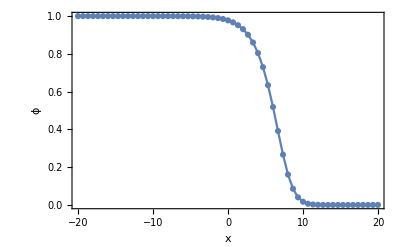

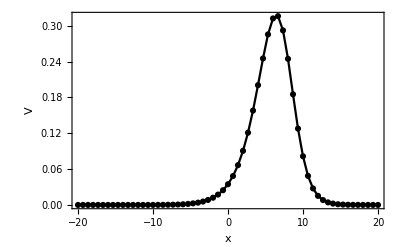

```mathematica
tplot = T;
p1=ListPlot[ Transpose[{xmesh, ϕAll[[;;, tplot]]}],  PlotRange-> Full];
p2=ListPlot[ Transpose[{xmesh, ϕAll[[;;, tplot]]}],  PlotRange-> Full, Joined-> True];
Show[p1, p2, Frame->True, FrameLabel->{"x", "ϕ"}]

p3=ListPlot[ Transpose[{xmesh, VAll[[;;, tplot]]}] ,  PlotRange-> Full,PlotStyle->{Black} ];
p4=ListPlot[ Transpose[{xmesh, VAll[[;;, tplot]]}], PlotRange-> Full, PlotStyle->{Black} , Joined-> True ];

Show[p3, p4, Frame->True, FrameLabel->{"x", "V"}]
(* Show[p1, p2, p3, p4, Frame->True, FrameLabel->{"x", "V"}] *)
```

## Skull model

## Load data

```mathematica
folder="/Users/dang/Documents/Projects/Tabler_skull/Scripts/Simulation_plots/Plots_model4b_FD_solver/simulation_set3/sim5/"
(*folder="/Users/dang/Documents/Projects/Tabler_skull/Scripts/Simulation_plots/Plots_model4b_FD_solver/simulation_set6_vary_viscosity/try2/"*)
ρAll=Import[ StringJoin[folder, "data_rho_1.csv"] ];
ϕAll=Import[ StringJoin[folder, "data_phi_1.csv"] ];
VAll=Import[ StringJoin[folder, "data_V_1.csv"] ];
```

/Users/dang/Documents/Projects/Tabler_skull/Scripts/Simulation_plots/Plots_model4b_FD_solver/simulation_set3/sim5/

```mathematica
parameters =Import[ StringJoin[folder, "data_parameters.csv"] ];
params=Thread[ToExpression@parameters[[;;, 1]]-> parameters[[ ;;, 2]] ]

Clear[Nx, tmax, T, L];
Nx=parameters[[ FirstPosition[ Map[#=="Nx"&, parameters[[;;, 1]]], True], 2 ]][[1]];
tmax=parameters[[ FirstPosition[ Map[#=="tmax"&, parameters[[;;, 1]]], True], 2 ]][[1]];
T=parameters[[ FirstPosition[ Map[#=="T"&, parameters[[;;, 1]]], True], 2 ]][[1]];
L=parameters[[ FirstPosition[ Map[#=="L"&, parameters[[;;, 1]]], True], 2 ]][[1]];

ΔxSet = 2L/(Nx);
ΔtSet = tmax/T;

xmesh= Range[-L, L, ΔxSet];
tmesh =Range[0, tmax, tmax/T];
```

{eO→1000,eM→30,η→25/9,ξ→5/18,τ→10,D1→15,α→1/50000,ρdA→0.0058,ρdB→0.0076,ρh→1/1000,aρ→4,a→4,L→1500,tmax→8,Nx→200,T→100}

```mathematica
parameters
```

{{eO,1000},{eM,30},{η,25/9},{ξ,5/18},{τ,10},{D1,15},{α,1/50000},{ρdA,0.0058},{ρdB,0.0076},{ρh,1/1000},{aρ,4},{a,4},{L,1500},{tmax,8},{Nx,200},{T,100}}

### Load second data set

```mathematica
LoadFolder="/Users/dang/Documents/Projects/Tabler_skull/Scripts/Simulation_plots/Plots_model4b_FD_solver/simulation_set6_vary_viscosity/try3/"
ρAll2=Import[StringJoin[LoadFolder, "data_rho_1.csv"]];
ϕAll2=Import[StringJoin[LoadFolder, "data_phi_1.csv"]];
VAll2=Import[StringJoin[LoadFolder, "data_V_1.csv"]];
```

/Users/dang/Documents/Projects/Tabler_skull/Scripts/Simulation_plots/Plots_model4b_FD_solver/simulation_set6_vary_viscosity/try3/

```mathematica
parameters2=Import[StringJoin[LoadFolder, "data_parameters.csv"]]
params2=Thread[ToExpression@parameters[[;;, 1]]-> parameters[[ ;;, 2]] ]

Clear[Nx2, tmax2, T2, L2];
Nx2=parameters[[ FirstPosition[ Map[#=="Nx"&, parameters[[;;, 1]]], True], 2 ]][[1]];
tmax2=parameters[[ FirstPosition[ Map[#=="tmax"&, parameters[[;;, 1]]], True], 2 ]][[1]];
T2=parameters[[ FirstPosition[ Map[#=="T"&, parameters[[;;, 1]]], True], 2 ]][[1]];
L2=parameters[[ FirstPosition[ Map[#=="L"&, parameters[[;;, 1]]], True], 2 ]][[1]];

ΔxSet2 = 2L2/(Nx2);
ΔtSet2= tmax2/T2;

xmesh2= Range[-L2, L2, ΔxSet2];
tmesh2 =Range[0, tmax2, tmax2/T2];
```

{{eO,4700},{eM,30},{ηM*(1 - ϕ[x, t]) + ηO*ϕ[x, t],(5*(1 - ϕ[x, t]))/18 + (250*ϕ[x, t])/9},{ξ,5/18},{τ,10},{D1,15},{α,4.25532×10^-6},{ρdA,0.0058},{ρdB,0.0076},{ρh,1/200},{aρ,8},{a,8},{L,1500},{tmax,4},{Nx,200},{T,100}}

{eO→4700,eM→30,ηM (1-ϕ[x,t])+ηO ϕ[x,t]→25/9,ξ→5/18,τ→10,D1→15,α→4.25532×10^-6,ρdA→0.0058,ρdB→0.0076,ρh→1/200,aρ→8,a→8,L→2000,tmax→4,Nx→200,T→100}

## Exploring different models

### Examine choices for k_D

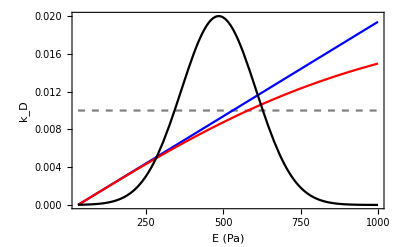

```mathematica
(*
kD := α (e-eM);
kD := Tanh[e];
*)
ϕ0[x_]:=(1-Tanh[a x/L])/2
e:= (eM(1-ϕ0[x])+eO ϕ0[x]);
params={eO-> 1000, eM-> 30, η-> 25/9, ξ-> 5/18, τ-> 10, D1->15, α-> 2*10^(-5), ρdA-> 5.8*10^(-3), ρdB->7.6*10^(-3),aρ->10,a->10,ρh->5*10^(-3)};
L=1500;

kD0:=0.01;
kD1:=α (e-eM);
kD2:=α eO  Tanh[(e-eM)/eO] /. params;
kD3:=0.02*Exp[-(e-(eO-eM)/2)^2/(2*(1/4(eO-eM)/2)^2)]
kD:=kD3

p0=Plot[{kD0/. params} , {e, eM/.params, (eO/.params)}, PlotStyle->{Gray, Dashed}];
p1=Plot[{kD1/. params} , {e, eM/.params, (eO/.params)}, PlotStyle->Blue];
p2=Plot[{kD2/. params} , {e, eM/.params, (eO/.params)}, PlotStyle->Red];
p3=Plot[{kD3/. params} , {e, eM/.params, (eO/.params)}, PlotStyle->Black];
Show[{p0,p1,p2,p3}, Frame-> True, FrameLabel-> {"E (Pa)", "k_D"}]
(*Plot[{kD3/. params} , {e, eM/.params, (eO/.params)}, PlotRange->All]*)
```

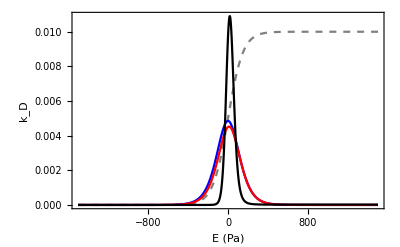

```mathematica
p0=Plot[{kD0(1-ϕ0[x])/. params} , {x, -L, L}, PlotStyle->{Gray, Dashed}, PlotRange->All];
p1=Plot[{kD1(1-ϕ0[x])/. params} , {x, -L, L}, PlotStyle->{Blue}, PlotRange->All];
p2=Plot[{kD2(1-ϕ0[x])/. params} , {x, -L, L}, PlotStyle->{Red}, PlotRange->All];
p3=Plot[{kD3(1-ϕ0[x])/. params} , {x, -L, L}, PlotStyle->{Black}, PlotRange->All];
Show[{p0,p1,p2,p3}, Frame-> True, FrameLabel-> {"E (Pa)", "k_D"}]
```

Differentiation rate

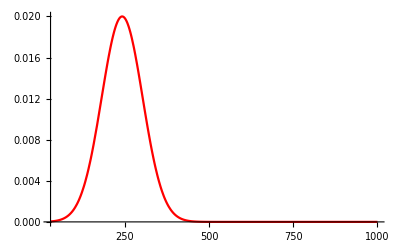

```mathematica
kD3b:=0.02*Exp[-(e-(eO-eM)/4)^2/(2*(1/4(eO-eM)/4)^2)] 
p3b=Plot[{kD3b/. params} , {e, eM/.params, (eO/.params)}, PlotStyle-> Red]
```

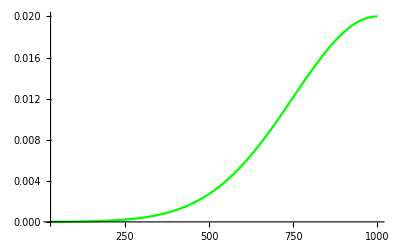

```mathematica
kD3c:=0.02*Exp[-(e-eO)^2/(2*(1/4 eO)^2)]
p3c=Plot[{kD3c/. params} , {e, eM/.params, (eO/.params)}, PlotStyle-> Green]
```

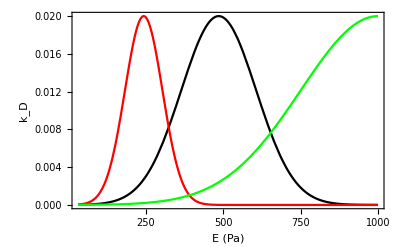

```mathematica
p3=Plot[{kD3/. params} , {e, eM/.params, (eO/.params)}, PlotStyle-> Black];
Show[{p3, p3b, p3c}, Frame-> True, FrameLabel-> {"E (Pa)", "k_D"}]
```

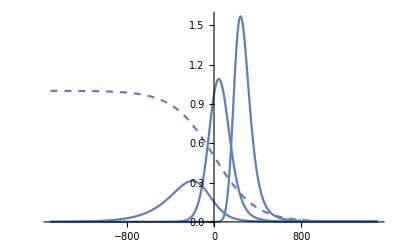

```mathematica
ϕ0[x_]:=(1-Tanh[a x/L])/2
e:=(eM(1-ϕ0[x])+eO ϕ0[x]) 
L=1500;
params={eO-> 1000, eM-> 30, η-> 25/9, ξ-> 5/18, τ-> 10, D1->15, α-> 2*10^(-5), ρdA-> 5.8*10^(-3), ρdB->7.6*10^(-3),aρ->4,a->4,ρh->5*10^(-3)};
pϕ=Plot[(ϕ0[x]) /.params, {x,-L,L}, PlotRange->All, PlotStyle->Dashed];
pDiff=Plot[100*(kD3*(1-ϕ0[x])) /.params, {x,-L,L}, PlotRange->All];
pDiffb=Plot[100*(kD3b*(1-ϕ0[x])) /.params, {x,-L,L}, PlotRange->All];
pDiffc=Plot[100*(kD3c*(1-ϕ0[x])) /.params, {x,-L,L}, PlotRange->All];
Show[pϕ, pDiff, pDiffb,pDiffc]
```

We can shift the differentiation peak by shifting the peak in the kD(E) profile. 
Moreover, the amplitude of the peak decreases towards the left, because the differentiation rate scales with (1-ϕ).

#### Predicted wave velocities

Wave velocity of general Fisher-KPP equation is 2 √D f'(0). For our system with f(ϕ) =k_D(1-ϕ), we get a velocity term 2√D (k_D'(ϕ)-k_D).

```mathematica
(*Simplify[(D[kD0, ϕ[x,t]]-kD0 )/.{ϕ[x,t]-> 0}], no Fisher wave since f[ϕ=0]≠0 *)
c1=Simplify[(D[kD1, ϕ[x,t]]-kD1 )/.{ϕ[x,t]-> 0}]
c2=Simplify[(D[kD2, ϕ[x,t]]-kD2 )/.{ϕ[x,t]-> 0}]
c3=Simplify[(D[kD3, ϕ[x,t]]-kD3 )/.{ϕ[x,t]-> 0}]
c1/.{ρ[x,t]-> ρh}
c2/.{ρ[x,t]-> ρh}
c3/.{ρ[x,t]-> ρh}
```

α (eM+((-2 eM+eO) ρ[x,t])/ρh)

1/50 (Tanh[3/100-6 ρ[x,t]]+194 Sech[3/100-6 ρ[x,t]]^2 ρ[x,t])

(ⅇ^(-(8 ((eM-eO) ρh+2 eM ρ[x,t])^2)/((eM-eO)^2 ρh^2)) ((-0.02 eM+0.02 eO) ρh^2+(0.64 eM ρh-0.64 eO ρh) ρ[x,t]+1.28 eM ρ[x,t]^2))/((eM-1. eO) ρh^2)

(-eM+eO) α

1/50 (194 ρh Sech[3/100-6 ρh]^2+Tanh[3/100-6 ρh])

(ⅇ^(-(8 (2 eM ρh+(eM-eO) ρh)^2)/((eM-eO)^2 ρh^2)) (1.28 eM ρh^2+(-0.02 eM+0.02 eO) ρh^2+ρh (0.64 eM ρh-0.64 eO ρh)))/((eM-1. eO) ρh^2)

```mathematica
N[2Sqrt[D1 c1]/.{ρ[x,t]-> ρh}/. params]
N[2Sqrt[D1 c2]/.{ρ[x,t]-> ρh}/. params]
N[2Sqrt[D1 c3]/.{ρ[x,t]-> ρh}/. params]
```

1.07889

1.07889

0.174593

Low values show that with our parameters the differentiation term doesn’t contribute much to wave propagation?!

#### Examine choices for ϕ_0[x]

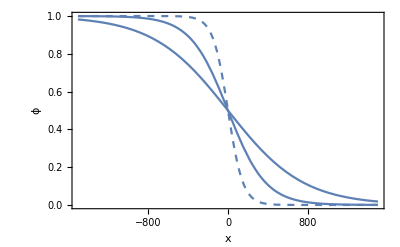

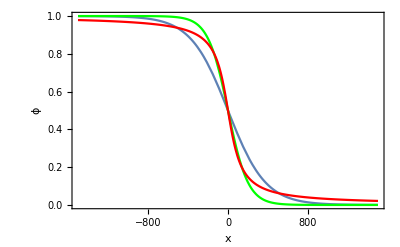

```mathematica
p1=Plot[{(1-Tanh[a x/L])/2} /. {a->4}, {x,-L,L}, Frame-> True, FrameLabel->{"x", "ϕ"}];
p1b=Plot[{(1-Tanh[a x/L])/2} /. {a->10}, {x,-L,L}, PlotStyle->Dashed, Frame-> True, FrameLabel->{"x", "ϕ"}];
p1c=Plot[{(1-Tanh[a x/L])/2} /. {a->2}, {x,-L,L}, Frame-> True, FrameLabel->{"x", "ϕ"}];

p2=Plot[(Exp[-α x]/(1+Exp[-α x])) /.{α-> 0.01}, {x,-L,L},PlotStyle->Green,Frame-> True,FrameLabel->{"x", "ϕ"}];
p3=Plot[(1-2/π ArcTan[α x])/2 /.{α->0.01}, {x,-L,L},PlotStyle->Red,Frame-> True,FrameLabel->{"x", "ϕ"}];
(*p2=Plot[(α/((2(x+L))^nh+c^nh)) /. {α-> 0.9*10^6,c-> 1000,nh-> 2},       {x, -L, L},PlotStyle->Red,Frame-> True,FrameLabel->{"x", "ϕ"}];*)
Show[{p1, p1b, p1c}]
Show[{p1,p2, p3}]
```

## Set up model

### Parameters

These are parameters that gave nice looking solutions with NDSolve but aren’t necessarily relevant.

Important: it seems that we need ρ_h > ρ_A, ρ_B to get reasonable results for the velocity, because we need P>0 everywhere. 
It seems like only D = 1000 microns^2/hr gives reasonable results. For D > 1000 microns^2/hr the system becomes unsolvable.
Viscosity η does not seem to matter at all.
Friction γ sets the overall magnitude of the velocity.

```mathematica
(*Random parameters *)
(*
(*params={ρdA->1, ρdB->1, τ-> 1, D1->.1, η->1, ξ->1, kF->0, z->1, α->1, eM->0.5,eO->1}; *)
params={ρdA->1.1, ρdB->1.1, ρh-> 1.2, τ->0.1, D1->0.01, η->0.1, ξ->0.1, z->1, α->2, eM->0.1, eO->5, a->8}; 
(*params={eM->0.1, eO->1,η->0.1, ξ->0.1,τ->0.1, D1->0.01,  α->2,  ρdA->1.1, ρdB->1.1, ρh-> 1.2 };*)
L=1;
tmax=1;
*)

(*Saved biological parameters*)
(*
params={eO-> 1000, eM-> 30, η-> 25/9, ξ-> 5/18, τ-> 12, D1->3600, α-> 1/1000, ρdA-> 10^(-2), ρdB-> 10^(-2), ρh->1.2*10^(-2), a->8};  
(* higher a = steeper Tanh function *)
(*params={eO-> 1000, eM-> 30, η-> 25/9, ξ-> 5/18, τ-> 10, D1->1000, α-> 10^(-4)/4, ρdA-> 5.8*10^(-3), ρdB->7.6*10^(-3), ρh->1*10^(-3), aρ-> 6,a->6}; *)
L=1500;
tmax=8;
*)
```

```mathematica
(* to play around with *)
(*params={eO-> 1000, eM-> 30, η-> 25/9, ξ-> 3/18, τ-> 10, D1->1000, α-> 2*10^(-5), ρdA-> 5.8*10^(-3), ρdB->7.6*10^(-3), ρh->1*10^(-3), aρ->4,a->4}; 
L=1500;
tmax=8;
*)
(*time in s, length in mm*) 
(*
params = {eO-> 1000, eM-> 30, η-> 10^4, ξ-> 10^9, τ-> 3600, D1-> 10^(-6), α-> 36, ρdA-> 10^4, ρdB-> 10^4}; 
L=1;
tmax=1000;
*)
(*time in hr, length in μm*)
(*params={eO-> 1000, eM-> 30, η-> 25/9, ξ-> 5/18, τ-> 12, D1->3600, α-> 1/1000, ρdA-> 10^(-2), ρdB-> 10^(-2), ρh->1.2*10^(-2), a->8};  (* higher a = steeper Tanh function *)*)
(*params={eO-> 1000, eM-> 30, η-> 25/9, ξ-> 5/18, τ-> 10, D1->3600, α-> 1/100, ρdA-> 10^(-2), ρdB-> 10^(-2), ρh-> 1/2*10^(-2)};*)
(*params={eO-> 1000, eM-> 30, η-> 25/9, ξ-> 5/18, τ-> 1, D1->1, α-> 1/100, ρdA-> 10^(0), ρdB-> 10^(0), ρh-> 10^(0)};*)
(*L=500; (* consistent with input data!*)
tmax=6;
*)
```

```mathematica
(* === new value of D1~15 === *)
(* sim 4 *)
(*params={eO-> 1000, eM-> 30, η-> 25/9, ξ->5/18, τ->10, D1->15, α->1*10^(-5), ρdA->5.8*10^(-3), ρdB->7.6*10^(-3),aρ->4,a->4,ρh->1*10^(-3), f->0};*)
(* sim 4b *)
(*params={eO-> 1000, eM-> 30, η->25/9, ξ->2/9,τ->10,D1->15,α->1*10^(-5),ρdA->5.8*10^(-3),ρdB->7.6*10^(-3),aρ->8,a->8,ρh->1*10^(-3), f->0};*)
params={eO->1000,eM->30,ηM->25/9,ηO->25/9,ξ->5/18,τ->10,D1->15,α->2*10^(-5),ρdA->0.0058,ρdB->0.0076,ρh->1/1000,aρ->4,a->4}
L=1500;
tmax=8;
Nx=200;
T=100;

(* AFM E15.5 data: eO-> 2200, eM-> 200*)
(*params={eO-> 2200, eM-> 200, η-> 25/9, ξ->5/18,τ->10,D1->15,α->2*10^(-5),ρdA->5.8*10^(-3),ρdB->7.6*10^(-3),aρ->4,a->4,ρh->5*10^(-3), f->0};*)
(* Nanoindenter E14.5 data: eO-> 4700, eM-> 200*)
(*params={eO-> 4700, eM-> 30, η-> 25/9, ξ->5/18,τ->10,D1->15,α->2*10^(-5)/4.7,ρdA->5.8*10^(-3),ρdB->7.6*10^(-3),aρ->8,a->8,ρh->5*10^(-3), f->0};*)

(* play around *)
(*
params={eO-> 4700, eM-> 30, ηM-> 10^4/3600, ηO-> 10^4/3600, ξ->5/18,τ->10,D1->15,α->2*10^(-5)/4.7,ρdA->5.8*10^(-3),ρdB->7.6*10^(-3),aρ->8,a->8,ρh->5*10^(-3),f->0};
L=1500;
tmax=4;
*)

(* set 6 *)
(*
params={eO-> 4700, eM-> 200, η-> 25/9, ξ->1.3055,τ->10,D1->15,α->2*10^(-5)/4.7,ρdA->5.8*10^(-3),ρdB->7.6*10^(-3),aρ->8,a->8,ρh->5*10^(-3), f->0, L-> 2000};  (* try 1, neg control*)
params={eO-> 4700, eM-> 30, η-> 25/9,, ξ->5/18,τ->10,D1->15,α->2*10^(-5)/4.7,ρdA->5.8*10^(-3),ρdB->7.6*10^(-3),aρ->8,a->8,ρh->5*10^(-3), f->0};  (* try 2, neg control but with L=2000 *)
params={eO-> 4700, eM-> 30, ηM-> 10^3/3600, ηO-> 10^5/3600, ξ->5/18,τ->10,D1->15,α->2*10^(-5)/4.7,ρdA->5.8*10^(-3),ρdB->7.6*10^(-3),aρ->8,a->8,ρh->5*10^(-3), f->0}; (* try 3 *)
params={eO-> 4700, eM-> 30, ηM-> 10^4/3600, ηO-> 10^4/3600, ξ->5/18,τ->10,D1->15,α->2*10^(-5)/4.7,ρdA->5.8*10^(-3),ρdB->7.6*10^(-3),aρ->8,a->8,ρh->5*10^(-3), f->0}; (* try 3 *)
*)

(*params={eO-> 1000, eM-> 30, ηM-> 10^3/3600, ηO-> 10^5/3600, ξ->2/9,τ->10,D1->15,α->1*10^(-5),ρdA->5.8*10^(-3),ρdB->7.6*10^(-3),aρ->4,a->4,ρh->1*10^(-3),f->0};*)
(*params={eO-> 1000, eM-> 30, η-> 25/9, ξ->0.28,τ->10,D1->15,α->1*10^(-5),ρdA->5.8*10^(-3),ρdB->7.6*10^(-3),aρ->2,a->4,ρh->1*10^(-3), f->0.28*0.1};*)
(*params={eO-> 1000, eM-> 30, η-> 25/9, ξ->0.28,τ->10,D1->15,α->1*10^(-5),ρdA->5.8*10^(-3),ρdB->7.6*10^(-3),aρ->2,a->6,ρh->1*10^(-3), f->0};*)
(*params={eO-> 1000, eM-> 30, η-> 25/9, ξ->5/18,τ->10,D1->15,α->2*10^(-5),ρdA->5.8*10^(-3),ρdB->7.6*10^(-3),aρ->4,a->4,ρh->5*10^(-3), f->0};*)
(*L=2000;*)
(*tmax=8;*)
(*tmax=4;*)
```

{eO→1000,eM→30,ηM→25/9,ηO→25/9,ξ→5/18,τ→10,D1→15,α→1/50000,ρdA→0.0058,ρdB→0.0076,ρh→1/1000,aρ→4,a→4}

#### Estimate some parameters

```mathematica
αEst =α1/.First@Solve[ vw==vc+Sqrt[ D1(α1 (eO-eM)+(kB-kA)/.{ρ[x,t]-> (ρdA+ρdB)/2}  )], α1] /. {vw-> 20, vc ->12 }/. params
```

(64+15 kA-15 kB)/14550

```mathematica
(* proliferation term *)
D1(kB-kA)/.{ρ[x,t]-> (ρdA+ρdB)/2}/. params
(* stiffness term *)
N[D1(α1 (eO-eM)) /. params/.{α1-> 10^(-6)}]
```

15 (-kA+kB)

0.01455

```mathematica
(* Wave velocity term *)
Sqrt[D1(α1 (eO-eM))+ D1(kB-kA)/.{ρ[x,t]-> (ρdA+ρdB)/2} ] /. params/.{α1-> αEst}
```

√(64+15 kA-15 kB+15 (-kA+kB))

#### Initial conditions

```mathematica
ρ0[x_]:=(Tanh[aρ x/L]+1)/2 (ρdA-ρdB)+ ρdB;
ϕ0[x_]:=(1-Tanh[a x/L])/2;
iv={ρ[x,0]==ρ0[x],ϕ[x,0]==ϕ0[x],v[x,0]==0} /. params;
(*iv={ρ[x,0]==ρ0[x],ϕ[x,0]==fData[x],v[x,0]==0} /. params;*)
bc={ρ[-L,t]==ρ0[-L],ρ[L,t]==ρ0[L],ϕ[-L,t]==ϕ0[-L],ϕ[L,t]==ϕ0[L],v[-L,t]==0,v[L,t]==0} /. params;
```

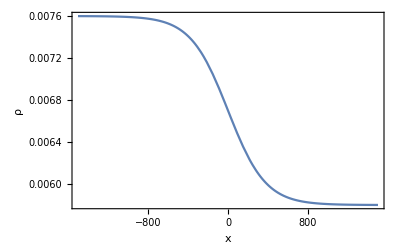
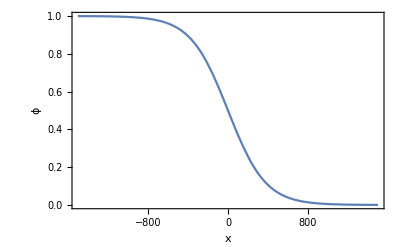

```mathematica
{Plot[{ρ0[x]} /. params, {x, -L, L}, Frame-> True, FrameLabel->{"x", "ρ"}], Plot[{ϕ0[x]} /. params, {x, -L, L}, Frame-> True, FrameLabel->{"x", "ϕ"}]}
```

#### PDE system

```mathematica
kA:=1/τ((ρdA-ρ[x,t])/ρdA);
kB:=1/τ((ρdB-ρ[x,t])/ρdB); 
(* Stiffness *)
e:= (eM(1-ϕ[x,t])+eO ϕ[x,t]) ;  
(*e:= (eM(1-ϕ[x,t])+eO ϕ[x,t]) (ρ[x,t]/ρh);*)
(*kD := α (e-eM); *)
```

```mathematica
(* Differential viscosities *)
Clear[η];
η:= (ηM (1-ϕ[x,t])+ ηO ϕ[x,t]);
```

```mathematica
kD0:=0.01;
kD1:=α (e-eM);
kD2:=α eO  Tanh[(e-eM)/eO] /. params;
kD3:=0.02*Exp[-(e-(eO-eM)/2)^2/(2*((eO-eM)/8)^2)];
kD3b:=0.02*Exp[-(e-(eO-eM)/4)^2/(2*(1/4(eO-eM)/4)^2)];
kD3c:=0.02*Exp[-(e-eO)^2/(2*(1/4 eO)^2)];
kD:=kD1
```

```mathematica
PDEsys={D[ρ[x,t],t]+D[ρ[x,t] (v[x,t]),x]==(kA (1-ϕ[x,t])+kB ϕ[x,t]) ρ[x,t],D[ϕ[x,t],t]+(v[x,t]) D[ϕ[x,t],x]==D1 D[ϕ[x,t],{x,2}]+ D1 D[ρ[x,t],x] D[ϕ[x,t],x]/ρ[x,t]+(kB-kA) ϕ[x,t] (1-ϕ[x,t])+kD (1-ϕ[x,t]),
ρ[x,t](η D[v[x,t],{x,2}]-ξ v[x,t])==e D[ρ[x,t],x] + D[e, x] Log[ρ[x,t]/ρh]*ρ[x,t] };
vars={ρ,ϕ,v};
fullsys=Join[PDEsys/.params,bc,iv]
```

{ρ^(0,1)[x,t]+ρ[x,t] v^(1,0)[x,t]+v[x,t] ρ^(1,0)[x,t]==ρ[x,t] (17.2414 (0.0058-ρ[x,t]) (1-ϕ[x,t])+13.1579 (0.0076-ρ[x,t]) ϕ[x,t]),ϕ^(0,1)[x,t]+v[x,t] ϕ^(1,0)[x,t]==(-17.2414 (0.0058-ρ[x,t])+13.1579 (0.0076-ρ[x,t])) (1-ϕ[x,t]) ϕ[x,t]+((1-ϕ[x,t]) (-30+30 (1-ϕ[x,t])+1000 ϕ[x,t]))/50000+(15 ρ^(1,0)[x,t] ϕ^(1,0)[x,t])/ρ[x,t]+15 ϕ^(2,0)[x,t],ρ[x,t] (-5/18 v[x,t]+(25/9 (1-ϕ[x,t])+25/9 ϕ[x,t]) v^(2,0)[x,t])==(30 (1-ϕ[x,t])+1000 ϕ[x,t]) ρ^(1,0)[x,t]+970 Log[1000 ρ[x,t]] ρ[x,t] ϕ^(1,0)[x,t],ρ[-1500,t]==0.0075994,ρ[1500,t]==0.0058006,ϕ[-1500,t]==1/2 (1+Tanh[4]),ϕ[1500,t]==1/2 (1-Tanh[4]),v[-1500,t]==0,v[1500,t]==0,ρ[x,0]==0.0076-0.0009 (1+Tanh[x/375]),ϕ[x,0]==1/2 (1-Tanh[x/375]),v[x,0]==0}

#### NDSolve

```mathematica
ndsol=NDSolve[fullsys,vars,{x,-L,L},{t,0,tmax},Method->{"EquationSimplification"->"Residual","IndexReduction"->Automatic}]
(*, InterpolationOrder->All, PrecisionGoal-> Infinity, MaxStepSize->30] *)(*, MaxSteps->100000, MaxStepSize->1] *)
```

{{ρ→InterpolatingFunction[…],ϕ→InterpolatingFunction[…],v→InterpolatingFunction[…]}}

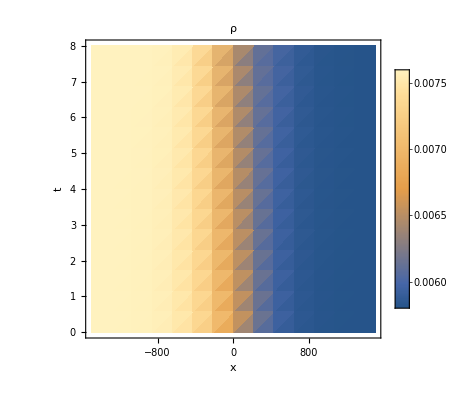
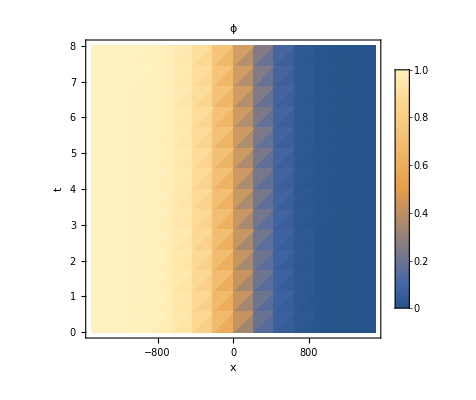
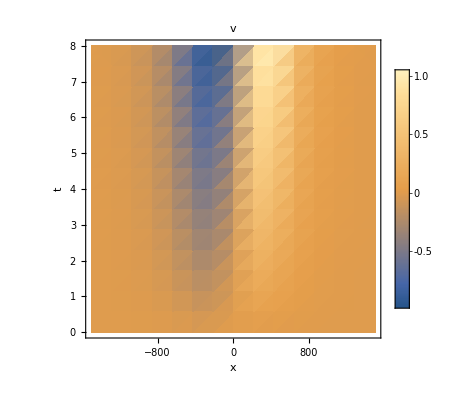

```mathematica
{DensityPlot[ρ[x,t]/.ndsol[[1]],{x,-L,L},{t,0,tmax},Mesh->None,PlotRange-> All, AxesLabel->Automatic,PlotLegends->Automatic, PlotLabel->"ρ"],
DensityPlot[ϕ[x,t]/.ndsol[[1]],{x,-L,L},{t,0,tmax},Mesh->None,PlotRange-> All,AxesLabel->Automatic,PlotLegends->Automatic, PlotLabel->"ϕ"],
DensityPlot[v[x,t]/.ndsol[[1]],{x,-L,L},{t,0,tmax},Mesh->None,PlotRange-> All,AxesLabel->Automatic,PlotLegends->Automatic, PlotLabel->"v"]}
```

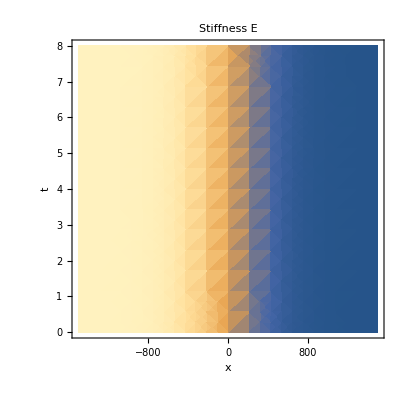

```mathematica
DensityPlot[(eM(1-ϕ[x,t])+eO ϕ[x,t])/. params/.ndsol[[1]],{x,-L,L},{t,0,tmax},Mesh->None,PlotRange-> All, AxesLabel->Automatic,PlotLabel->"Stiffness E"]
```

#### Discretized PDE system

```mathematica
PDEsys
```

{ρ^(0,1)[x,t]+ρ[x,t] v^(1,0)[x,t]+v[x,t] ρ^(1,0)[x,t]==ρ[x,t] (((ρdA-ρ[x,t]) (1-ϕ[x,t]))/(ρdA τ)+((ρdB-ρ[x,t]) ϕ[x,t])/(ρdB τ)),ϕ^(0,1)[x,t]+v[x,t] ϕ^(1,0)[x,t]==(-(ρdA-ρ[x,t])/(ρdA τ)+(ρdB-ρ[x,t])/(ρdB τ)) (1-ϕ[x,t]) ϕ[x,t]+α (1-ϕ[x,t]) (-eM+eM (1-ϕ[x,t])+eO ϕ[x,t])+(D1 ρ^(1,0)[x,t] ϕ^(1,0)[x,t])/ρ[x,t]+D1 ϕ^(2,0)[x,t],ρ[x,t] (-ξ v[x,t]+(ηM (1-ϕ[x,t])+ηO ϕ[x,t]) v^(2,0)[x,t])==(eM (1-ϕ[x,t])+eO ϕ[x,t]) ρ^(1,0)[x,t]+Log[ρ[x,t]/ρh] ρ[x,t] (-eM ϕ^(1,0)[x,t]+eO ϕ^(1,0)[x,t])}

NB explicitly check upwind scheme and CFL condition

```mathematica
(* Equations for PDE *)
(* Time derivative*)
discretizationT={Derivative[0,1][ρ][x,t]->  (Subscript[ρ, i,m+1]-Subscript[ρ, i,m])/Δt, Derivative[0,1][ϕ][x,t]->  (Subscript[ϕ, i,m+1]-Subscript[ϕ, i,m])/Δt}; (* forward scheme*)

(* 1. forward Euler schemes*)
(* a. explicit scheme, centered diff *)
discretization1 = 
{ρ[x,t]-> Subscript[ρ, i,m], Derivative[1,0][ρ][x,t]-> (Subscript[ρ, i+1,m]-Subscript[ρ, i-1,m])/(2 Δx), ϕ[x,t]-> Subscript[ϕ, i,m], Derivative[1,0][ϕ][x,t]-> (Subscript[ϕ, i+1,m]-Subscript[ϕ, i-1,m])/(2 Δx),Derivative[2,0][ϕ][x,t]-> (Subscript[ϕ, i+1,m]- 2 Subscript[ϕ, i,m] + Subscript[ϕ, i-1,m])/(Δx)^2,
v[x,t]-> Subscript[v, i,m], Derivative[1,0][v][x,t]-> (Subscript[v, i+1,m]-Subscript[v, i-1,m])/(2 Δx),Derivative[2,0][v][x,t]-> (Subscript[v, i+1,m]- 2 Subscript[v, i,m] + Subscript[v, i-1,m])/(Δx)^2};
pdeDiscretized1 = PDEsys /.discretizationT /. discretization1;

(* b. explicit scheme, fwd diff *)
(*discretization1b = {ϕ[x,t]-> Subscript[ϕ, i,m], ϕ^(0,1)[x,t]->  (Subscript[ϕ, i,m+1]-Subscript[ϕ, i,m])/Δt,ϕ^(1,0)[x,t]-> (Subscript[ϕ, i+1,m]-Subscript[ϕ, i,m])/(2 Δx),ϕ^(2,0)[x,t]-> (Subscript[ϕ, i+1,m]- 2 Subscript[ϕ, i,m] + Subscript[ϕ, i-1,m])/(Δx)^2,V[x,t]-> Subscript[V, i,m], V^(2,0)[x,t]-> (Subscript[V, i+1,m]- 2 Subscript[V, i,m] + Subscript[V, i-1,m])/(Δx)^2};  
pdeDiscretized =PDEsys /.discretizationT /. discretization1b;*) 

(* 2. backward Euler scheme *) 
(* implicit scheme, centered diff *)
(* NB cannot use implicit scheme for equation for V*)
discretization2 = Join[{ρ[x,t]-> Subscript[ρ, i,m], Derivative[1,0][ρ][x,t]-> (Subscript[ρ, i+1,m]-Subscript[ρ, i-1,m])/(2 Δx),ϕ[x,t]-> Subscript[ϕ, i,m], Derivative[1,0][ϕ][x,t]-> (Subscript[ϕ, i+1,m]-Subscript[ϕ, i-1,m])/(2 Δx),Derivative[2,0][ϕ][x,t]-> (Subscript[ϕ, i+1,m]- 2 Subscript[ϕ, i,m] + Subscript[ϕ, i-1,m])/(Δx)^2}/.{m->m+1}, {v[x,t]-> Subscript[v, i,m],Derivative[1,0][v][x,t]-> (Subscript[v, i+1,m]-Subscript[v, i-1,m])/(2 Δx), Derivative[2,0][v][x,t]-> (Subscript[v, i+1,m]- 2 Subscript[v, i,m] + Subscript[v, i-1,m])/(Δx)^2}];

pdeDiscretized2 =Join[ PDEsys[[;;2]]/.discretizationT /. discretization2, {PDEsys[[3]]/.discretizationT /. discretization1}];

(* 3. Crank-Nicolson scheme: combine discretizations *)
discretization3= {ρ[x,t]->( Subscript[ρ, i,m] + Subscript[ρ, i,m+1])/2, Derivative[1,0][ρ][x,t]-> ((Subscript[ρ, i+1,m]-Subscript[ρ, i-1,m])/(2 Δx)+(Subscript[ρ, i+1,m+1]-Subscript[ρ, i-1,m+1])/(2 Δx))/2,ϕ[x,t]-> (Subscript[ϕ, i,m]+Subscript[ϕ, i,m+1])/2, Derivative[1,0][ϕ][x,t]-> ((Subscript[ϕ, i+1,m]-Subscript[ϕ, i-1,m])/(2 Δx)+(Subscript[ϕ, i+1,m+1]-Subscript[ϕ, i-1,m+1])/(2 Δx))/2,Derivative[2,0][ϕ][x,t]-> ((Subscript[ϕ, i+1,m]- 2 Subscript[ϕ, i,m] + Subscript[ϕ, i-1,m])/(Δx)^2+(Subscript[ϕ, i+1,m+1]- 2 Subscript[ϕ, i,m+1] + Subscript[ϕ, i-1,m+1])/(Δx)^2)/2,
v[x,t]-> (Subscript[v, i,m]+Subscript[v, i,m+1])/2,Derivative[1,0][v][x,t]-> ((Subscript[v, i+1,m]-Subscript[v, i-1,m])/(2 Δx)+(Subscript[v, i+1,m]-Subscript[v, i-1,m])/(2 Δx))/2, Derivative[2,0][v][x,t]->( (Subscript[v, i+1,m]- 2 Subscript[v, i,m] + Subscript[v, i-1,m])/(Δx)^2+(Subscript[v, i+1,m+1]- 2 Subscript[v, i,m+1] + Subscript[v, i-1,m+1])/(Δx)^2)/2};
```

Use upwind scheme for stability. See https://en.wikipedia.org/wiki/Upwind_scheme 
Idea here is just to replace derivatives in for the advection terms by upwind terms while keeping the rest the same.

```mathematica
(*  4. Upwind scheme for 1st derivaties *)
(*upwind1 = {ρ^(1,0)[x,t]-> (Subscript[ρ, i,m]-Subscript[ρ, i-1,m])/Δx, v^(1,0)[x,t]-> (Subscript[v, i,m]-Subscript[v, i-1,m])/Δx, ϕ^(1,0)[x,t]-> (Subscript[ϕ, i,m]-Subscript[ϕ, i-1,m])/Δx};*)

PDEsysUpwind=
{Derivative[0,1][ρ][x,t]+ρ[x,t] (Subscript[v, i,m]-Subscript[v, i-1,m])/Δx+v[x,t] (Subscript[ρ, i,m]-Subscript[ρ, i-1,m])/Δx==ρ[x,t] (((ρdA-ρ[x,t]) (1-ϕ[x,t]))/(ρdA τ)+((ρdB-ρ[x,t]) ϕ[x,t])/(ρdB τ)),Derivative[0,1][ϕ][x,t]+v[x,t] (Subscript[ϕ, i,m]-Subscript[ϕ, i-1,m])/Δx==(-(ρdA-ρ[x,t])/(ρdA τ)+(ρdB-ρ[x,t])/(ρdB τ)) (1-ϕ[x,t]) ϕ[x,t]+α (1-ϕ[x,t]) (-eM+eM (1-ϕ[x,t])+eO ϕ[x,t])+(D1 Derivative[1,0][ρ][x,t] Derivative[1,0][ϕ][x,t])/ρ[x,t]+D1 Derivative[2,0][ϕ][x,t],ρ[x,t] (-ξ v[x,t]+(ηM (1-ϕ[x,t])+ηO ϕ[x,t]) Derivative[2,0][v][x,t])==f+(eM (1-ϕ[x,t])+eO ϕ[x,t]) Derivative[1,0][ρ][x,t]+Log[ρ[x,t]/ρh] ρ[x,t] (-eM Derivative[1,0][ϕ][x,t]+eO Derivative[1,0][ϕ][x,t])}; 
PDEsysUpwind1b=
{Derivative[0,1][ρ][x,t]+ρ[x,t] Derivative[1,0][v][x,t]+v[x,t] (Subscript[ρ, i,m]-Subscript[ρ, i-1,m])/Δx==ρ[x,t] (((ρdA-ρ[x,t]) (1-ϕ[x,t]))/(ρdA τ)+((ρdB-ρ[x,t]) ϕ[x,t])/(ρdB τ)),Derivative[0,1][ϕ][x,t]+v[x,t] (Subscript[ϕ, i,m]-Subscript[ϕ, i-1,m])/Δx==(-(ρdA-ρ[x,t])/(ρdA τ)+(ρdB-ρ[x,t])/(ρdB τ)) (1-ϕ[x,t]) ϕ[x,t]+α (1-ϕ[x,t]) (-eM+eM (1-ϕ[x,t])+eO ϕ[x,t])+(D1 Derivative[1,0][ρ][x,t] Derivative[1,0][ϕ][x,t])/ρ[x,t]+D1 Derivative[2,0][ϕ][x,t],ρ[x,t] (-ξ v[x,t]+(ηM (1-ϕ[x,t])+ηO ϕ[x,t]) Derivative[2,0][v][x,t])==f+(eM (1-ϕ[x,t])+eO ϕ[x,t]) Derivative[1,0][ρ][x,t]+Log[ρ[x,t]/ρh] ρ[x,t] (-eM Derivative[1,0][ϕ][x,t]+eO Derivative[1,0][ϕ][x,t])}; 

(*upwind2 = {ρ^(1,0)[x,t]-> (3 Subscript[ρ, i,m]- 4 Subscript[ρ, i-1,m] + Subscript[ρ, i-2,m])/(2Δx), v^(1,0)[x,t]-> (3 Subscript[v, i,m]-4 Subscript[v, i-1,m]+Subscript[v, i-2,m])/(2 Δx), ϕ^(1,0)[x,t]-> (3 Subscript[ϕ, i,m] - 4 Subscript[ϕ, i-1,m] + Subscript[ϕ, i,m])/(2 Δx)}; (* 2nd order upwind*) *)
PDEsysUpwind2=
{Derivative[0,1][ρ][x,t]+ρ[x,t] (3 Subscript[v, i,m]-4 Subscript[v, i-1,m]+Subscript[v, i-2,m])/(2 Δx)+v[x,t] (3 Subscript[ρ, i,m]- 4 Subscript[ρ, i-1,m] + Subscript[ρ, i-2,m])/(2Δx)==ρ[x,t] (((ρdA-ρ[x,t]) (1-ϕ[x,t]))/(ρdA τ)+((ρdB-ρ[x,t]) ϕ[x,t])/(ρdB τ)),Derivative[0,1][ϕ][x,t]+v[x,t] (3 Subscript[ϕ, i,m] - 4 Subscript[ϕ, i-1,m] + Subscript[ϕ, i,m])/(2 Δx)==(-(ρdA-ρ[x,t])/(ρdA τ)+(ρdB-ρ[x,t])/(ρdB τ)) (1-ϕ[x,t]) ϕ[x,t]+α (1-ϕ[x,t]) (-eM+eM (1-ϕ[x,t])+eO ϕ[x,t])+(D1 Derivative[1,0][ρ][x,t] Derivative[1,0][ϕ][x,t])/ρ[x,t]+D1 Derivative[2,0][ϕ][x,t],ρ[x,t] (-ξ v[x,t]+(ηM (1-ϕ[x,t])+ηO ϕ[x,t]) Derivative[2,0][v][x,t])==f+(eM (1-ϕ[x,t])+eO ϕ[x,t]) Derivative[1,0][ρ][x,t]+Log[ρ[x,t]/ρh] ρ[x,t] (-eM Derivative[1,0][ϕ][x,t]+eO Derivative[1,0][ϕ][x,t])}; 

pdeDiscretized4 =PDEsysUpwind /. discretization1 /.discretizationT;
pdeDiscretized4b =PDEsysUpwind1b/. discretization1 /.discretizationT;
pdeDiscretized42 =PDEsysUpwind2 /. discretization1 /.discretizationT;
pdeDiscretized4
```

{((-v_(-1+i,m)+v_(i,m)) ρ_(i,m))/Δx+(v_(i,m) (-ρ_(-1+i,m)+ρ_(i,m)))/Δx+(-ρ_(i,m)+ρ_(i,1+m))/Δt==ρ_(i,m) (((ρdA-ρ_(i,m)) (1-ϕ_(i,m)))/(ρdA τ)+((ρdB-ρ_(i,m)) ϕ_(i,m))/(ρdB τ)),(v_(i,m) (-ϕ_(-1+i,m)+ϕ_(i,m)))/Δx+(-ϕ_(i,m)+ϕ_(i,1+m))/Δt==(-(ρdA-ρ_(i,m))/(ρdA τ)+(ρdB-ρ_(i,m))/(ρdB τ)) (1-ϕ_(i,m)) ϕ_(i,m)+α (1-ϕ_(i,m)) (-eM+eM (1-ϕ_(i,m))+eO ϕ_(i,m))+(D1 (-ρ_(-1+i,m)+ρ_(1+i,m)) (-ϕ_(-1+i,m)+ϕ_(1+i,m)))/(4 Δx^2 ρ_(i,m))+(D1 (ϕ_(-1+i,m)-2 ϕ_(i,m)+ϕ_(1+i,m)))/Δx^2,ρ_(i,m) (-ξ v_(i,m)+((v_(-1+i,m)-2 v_(i,m)+v_(1+i,m)) (ηM (1-ϕ_(i,m))+ηO ϕ_(i,m)))/Δx^2)==f+((-ρ_(-1+i,m)+ρ_(1+i,m)) (eM (1-ϕ_(i,m))+eO ϕ_(i,m)))/(2 Δx)+Log[(ρ_(i,m))/ρh] ρ_(i,m) (-(eM (-ϕ_(-1+i,m)+ϕ_(1+i,m)))/(2 Δx)+(eO (-ϕ_(-1+i,m)+ϕ_(1+i,m)))/(2 Δx))}

```mathematica
pdeDiscretized = pdeDiscretized1;
Simplify[pdeDiscretized/.params]
```

{((-2 Δx-Δt v_(-1+i,m)+Δt v_(1+i,m)) ρ_(i,m)+2 Δx ρ_(i,1+m)+Δt v_(i,m) (-ρ_(-1+i,m)+ρ_(1+i,m)))/(2 Δt Δx)==4.08348 ρ_(i,m) (0.0244889-3.39852×10^-18 ϕ_(i,m)+ρ_(i,m) (-4.22222+1. ϕ_(i,m))),-(0.5 (7.5 ρ_(-1+i,m)+(30.+Δx v_(i,m)) ρ_(i,m)-7.5 ρ_(1+i,m)) ϕ_(-1+i,m))/(Δx^2 ρ_(i,m))+(-0.0194-1./Δt+30./Δx^2) ϕ_(i,m)+0.0194 ϕ_(i,m)^2+ρ_(i,m) ϕ_(i,m) (-4.08348+4.08348 ϕ_(i,m))+(1. ϕ_(i,1+m))/Δt-(15. ϕ_(1+i,m))/Δx^2+(0.5 v_(i,m) ϕ_(1+i,m))/Δx+((3.75 ρ_(-1+i,m)-3.75 ρ_(1+i,m)) ϕ_(1+i,m))/(Δx^2 ρ_(i,m))==0,(5 (10 v_(-1+i,m)-(20+Δx^2) v_(i,m)+10 v_(1+i,m)) ρ_(i,m))/(18 Δx^2)==-(5 (ρ_(-1+i,m) (3+97 ϕ_(i,m))-ρ_(1+i,m) (3+97 ϕ_(i,m))+97 Log[1000 ρ_(i,m)] ρ_(i,m) (ϕ_(-1+i,m)-ϕ_(1+i,m))))/Δx}

## Simulate model

### Solve discretized system: initialization

```mathematica
(*Define mesh*)
(*
Nx=200;
T= 100;
*)
ΔxSet = 2L/(Nx);
ΔtSet = tmax/T;

xmesh= Range[-L, L, ΔxSet];
tmesh =Range[0, tmax, tmax/T];
Print[xmesh[[Nx/2+1]]];
Print[ N@ΔxSet]
Print[ N@ΔtSet]
```

0

15.

0.08

Check CFL condition (https://en.wikipedia.org/wiki/Courant%E2%80%93Friedrichs%E2%80%93Lewy_condition)
Typically C=(u Δt)/Δx ≤ C_max with C_max=1.
The velocity u needs to be estimated.

```mathematica
vmax=20; (*estimation of max velocity*)
N[ ((ρdA+ρdB)/2/.params)  ΔtSet/ΔxSet] (* ρ[x,t] v^(1,0)[x,t]*)
N[ vmax  ΔtSet/ΔxSet] (*v[x,t] ρ^(1,0)[x,t]*) (*v[x,t] ϕ^(1,0)[x,t]*)
```

0.0000357333

0.106667

```mathematica
(* Boundary conditions *)
ρL=ρ0[-L] /. params; ρR=ρ0[L] /. params; 
(*ϕL = 1; ϕR = 0;*)
ϕL=ϕ0[-L]/.params; ϕR=ϕ0[L]/.params;
VL=0; VR=0;

(* normal *)
bcρ={Subscript[ρ, 0,m]==ρL,Subscript[ρ, Nx,m]==ρR};
bcϕ={Subscript[ϕ, 0,m]==ϕL,Subscript[ϕ, Nx,m]==ϕR};
bcV={Subscript[v, 0,m]==VL,Subscript[v, Nx,m]==VR};
bcρRepl={Subscript[ρ, 0,m]-> ρL,Subscript[ρ, Nx,m]->ρR};
bcϕRepl={Subscript[ϕ, 0,m]-> ϕL,Subscript[ϕ, Nx,m]->ϕR};
bcVRepl={Subscript[v, 0,m]-> VL,Subscript[v, Nx,m]->VR};

(* 2nd order upwind *)
bcρ2={Subscript[ρ, -1,m]==ρL,Subscript[ρ, 0,m]==ρL,Subscript[ρ, Nx,m]==ρR,Subscript[ρ, Nx+1,m]==ρR};
bcϕ2={Subscript[ϕ, -1,m]==ϕL,Subscript[ϕ, 0,m]==ϕL,Subscript[ϕ, Nx,m]==ϕR,Subscript[ϕ, Nx+1,m]==ϕR};
bcV2={Subscript[v, -1,m]==VL,Subscript[v, 0,m]==VL,Subscript[v, Nx,m]==VR,Subscript[v, Nx+1,m]==VR};
bcρRepl2={Subscript[ρ, -1,m]-> ρL,Subscript[ρ, 0,m]-> ρL,Subscript[ρ, Nx,m]->ρR,Subscript[ρ, Nx+1,m]->ρR};
bcϕRepl2={Subscript[ϕ, -1,m]-> ϕL,Subscript[ϕ, 0,m]-> ϕL,Subscript[ϕ, Nx,m]->ϕR,Subscript[ϕ, Nx+1,m]->ϕR};
bcVRepl2={Subscript[v, -1,m]-> VL,Subscript[v, 0,m]-> VL,Subscript[v, Nx,m]->VR,Subscript[v, Nx+1,m]->VR};

(* Initial conditions *)
ρ0Set=Table[ ρ0[ xmesh[[i]] ] , {i,1,Nx+1}] /. params;
(*ϕ0Set=Table[Boole[(i<Nx/2)], {i, 0, Nx}];*)
ϕ0Set=Table[ ϕ0[xmesh[[i]]], {i,1, Nx+1}] /. params;
```

```mathematica
(* Initialize values *)
ρAll=Table[Subscript[ρ, i,m], {i, 0, Nx}, {m, 0, T}];
ϕAll=Table[Subscript[ϕ, i,m], {i, 0, Nx}, {m, 0, T}];
VAll=Table[Subscript[v, i,m], {i, 0, Nx}, {m, 0, T}];

(* set initial values*)
Do[ρAll[[i+1, 1]] =ρ0Set[[i+1]], {i,0,Nx}]; 
Do[ϕAll[[i+1, 1]] =ϕ0Set[[i+1]], {i,0,Nx}]; 

(* set Dirichlet boundary values *)
Do[ρAll[[1, j+1]] = ρL, {j, 0, T}]
Do[ρAll[[Nx+1, j+1]] = ρR, {j, 0, T}]
Do[ϕAll[[1, j+1]] = ϕL, {j, 0, T}]
Do[ϕAll[[Nx+1, j+1]] = ϕR, {j, 0, T}]
Do[VAll[[1, j+1]] = VL, {j, 0, T}]
Do[VAll[[Nx+1, j+1]] = VR, {j, 0, T}]
```

```mathematica
(* Only for Crank-Nicolson: initial values for V*)
(*
Vt0[x_]:=0;
Vt0Set=Table[Vt0[xmesh[[i]]], {i,0, Nx}] /. params;
Do[ VAll[[i+1, 1]] =Vt0Set[[i+1]], {i,0,Nx}];
*)
```

### Solve discretized system: explicit method

#### Test

```mathematica
thism = 0;

(* current values *)
ρReplace=MapThread[#1->#2&,{Table[Subscript[ρ, i,thism] , {i,0, Nx}], ρAll[[;;, thism+1]]}];
ϕReplace=MapThread[#1->#2&,{Table[Subscript[ϕ, i,thism] , {i,0, Nx}], ϕAll[[;;, thism+1]]}]; VReplace=MapThread[#1->#2&,{Table[Subscript[v, i,thism] , {i,0, Nx}], VAll[[;;, thism+1]]}];

(* boundary conditions *)
bcJoined =Flatten@Table[Join[bcϕRepl, bcVRepl], {m, thism, thism+1}];

(* def system *)
pdeTemp=(pdeDiscretized /. {m-> thism, Δx -> ΔxSet,Δt -> ΔtSet} /. params);
condsAll=Flatten@Table[pdeTemp/. bcJoined /.ρReplace/. ϕReplace /. VReplace  , {i, 1, Nx-1}];
varlist=Flatten@Table[{Subscript[ρ, i,m],Subscript[v, i,m], Subscript[ϕ, i,m]}, {i,1,Nx-1}] /. {m->thism}; (* variables to solve*)
```

```mathematica
(* Solve for V*)
condsAll=Join[bcV/. {m-> thism},Table[pdeTemp[[3]] , {i, 1, Nx-1}]]/.ρReplace /.ϕReplace;
Vlist=Table[Subscript[v, i,m], {i,0,Nx}] /. {m-> thism};
VDiscNSol=First@NSolve[condsAll, Vlist];
VAll=(VAll/.VDiscNSol);
```

```mathematica
(* Solve for ρ, ϕ*)
If[thism<T,
condsAll=Join[bcρ/.{m->thism+1},bcϕ/.{m->thism+1},Table[pdeTemp[[1]] , {i, 1, Nx-1}], Table[pdeTemp[[2]] , {i, 1, Nx-1}]] /.VDiscNSol /. ρReplace/.ϕReplace;

varlist=Flatten@Table[{Subscript[ρ, i,m],Subscript[ϕ, i,m]}, {i,0,Nx}] /. {m-> (thism+1)};
DiscNSol=First@NSolve[condsAll, varlist, Reals, Method->"Homotopy"];
ρAll=(ρAll/.DiscNSol);
ϕAll=(ϕAll/.DiscNSol);
]
```

```mathematica
(* solve using explicit matrix inversion*)
(*
b = Normal@CoefficientArrays[condsAll, varlist][[1]]; (*RHS*)
mat =Normal@CoefficientArrays[condsAll, varlist][[2]]; (*LHS*)
(*matsol = -Inverse[mat, Method->"CofactorExpansion"].b; *)
matsol = LinearSolve[mat, -b]; (*, Method->"CofactorExpansion"*)
varNsol = Thread[varlist -> matsol];
*)
```

#### Test 2

```mathematica
thism = 0;

(* current values *)
ρReplace=MapThread[#1->#2&,{Table[Subscript[ρ, i,thism] , {i,-1, Nx+1}], Flatten@{ρL, ρAll[[;;, thism+1]], ρR}   }];
ϕReplace=MapThread[#1->#2&,{Table[Subscript[ϕ, i,thism] , {i,-1, Nx+1}],  Flatten@{ϕL, ϕAll[[;;, thism+1]], ϕR} }]; VReplace=MapThread[#1->#2&,{Table[Subscript[v, i,thism] , {i,-1, Nx+1}],  Flatten@{VL, VAll[[;;, thism+1]], VR} }];

(* boundary conditions *)
bcJoined =Flatten@Table[Join[bcϕRepl2, bcVRepl2], {m, thism, thism+1}];

(* def system *)
pdeTemp=(pdeDiscretized /. {m-> thism, Δx -> ΔxSet,Δt -> ΔtSet} /. params);
condsAll=Flatten@Table[pdeTemp/. bcJoined /.ρReplace/. ϕReplace /. VReplace  , {i, 1, Nx-1}];
varlist=Flatten@Table[{Subscript[ρ, i,m],Subscript[v, i,m], Subscript[ϕ, i,m]}, {i,1,Nx-1}] /. {m->thism}; (* variables to solve*)
```

```mathematica
(* Solve for V*)
condsAll=Join[bcV2/. {m-> thism},Table[pdeTemp[[3]] , {i, 1, Nx-1}]]/.ρReplace /.ϕReplace;
Vlist=Table[Subscript[v, i,m], {i,-1,Nx+1}] /. {m-> thism};
VDiscNSol=First@NSolve[condsAll, Vlist];
VAll=(VAll/.VDiscNSol);
```

```mathematica
(* Solve for ρ, ϕ*)
If[thism<T,
condsAll=Join[bcρ2/.{m->thism+1},bcϕ2/.{m->thism+1},Table[pdeTemp[[1]] , {i, 1, Nx-1}], Table[pdeTemp[[2]] , {i, 1, Nx-1}]] /.VDiscNSol /. ρReplace/.ϕReplace;

varlist=Flatten@Table[{Subscript[ρ, i,m],Subscript[ϕ, i,m]}, {i,-1,Nx+1}] /. {m-> (thism+1)};
DiscNSol=First@NSolve[condsAll, varlist, Reals, Method->"Homotopy"];
ρAll=(ρAll/.DiscNSol);
ϕAll=(ϕAll/.DiscNSol);
]
```

$Aborted

```mathematica
(* solve using explicit matrix inversion*)
(*
b = Normal@CoefficientArrays[condsAll, varlist][[1]]; (*RHS*)
mat =Normal@CoefficientArrays[condsAll, varlist][[2]]; (*LHS*)
(*matsol = -Inverse[mat, Method->"CofactorExpansion"].b; *)
matsol = LinearSolve[mat, -b]; (*, Method->"CofactorExpansion"*)
varNsol = Thread[varlist -> matsol];
*)
```

#### Loop

```mathematica
Do[
Print[thism];



(* current values *)
ρReplace=MapThread[#1->#2&,{Table[Subscript[ρ, i,thism] , {i,0, Nx}], ρAll[[;;, thism+1]]}];
ϕReplace=MapThread[#1->#2&,{Table[Subscript[ϕ, i,thism] , {i,0, Nx}], ϕAll[[;;, thism+1]]}]; VReplace=MapThread[#1->#2&,{Table[Subscript[v, i,thism] , {i,0, Nx}], VAll[[;;, thism+1]]}];

(* boundary conditions *)
bcJoined =Flatten@Table[Join[bcϕRepl, bcVRepl], {m, thism, thism+1}];

(* def system *)
pdeTemp=Simplify@(pdeDiscretized /. {m-> thism, Δx -> ΔxSet,Δt -> ΔtSet} /. params);
condsAll=Flatten@Table[pdeTemp/. bcJoined /.ρReplace/. ϕReplace /. VReplace  , {i, 1, Nx-1}];
varlist=Flatten@Table[{Subscript[ρ, i,m],Subscript[v, i,m], Subscript[ϕ, i,m]}, {i,1,Nx-1}] /. {m->thism}; (* variables to solve*)

(* Solve for V*)
condsAll=Join[bcV/. {m-> thism},Table[pdeTemp[[3]] , {i, 1, Nx-1}]]/.ρReplace /.ϕReplace;
Vlist=Table[Subscript[v, i,m], {i,0,Nx}] /. {m-> thism};
VDiscNSol=First@NSolve[condsAll, Vlist];
VAll=(VAll/.VDiscNSol);

If[thism<T,
condsAll=Join[bcρ/.{m->thism+1},bcϕ/.{m->thism+1},Table[pdeTemp[[1]] , {i, 1, Nx-1}], Table[pdeTemp[[2]] , {i, 1, Nx-1}]] /.VDiscNSol /. ρReplace/.ϕReplace;

varlist=Flatten@Table[{Subscript[ρ, i,m],Subscript[ϕ, i,m]}, {i,0,Nx}] /. {m-> (thism+1)};
DiscNSol=First@NSolve[condsAll, varlist, Reals, Method->"Homotopy"];
ρAll=(ρAll/.DiscNSol);
ϕAll=(ϕAll/.DiscNSol);
],
{thism, 0, T}];
```

0

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

#### Loop 2

Second order upwind scheme

```mathematica
Do[
Print[thism];

(* current values *)
ρReplace=MapThread[#1->#2&,{Table[Subscript[ρ, i,thism] , {i,-1, Nx+1}], Flatten@{ρL, ρAll[[;;, thism+1]],ρR} }];
ϕReplace=MapThread[#1->#2&,{Table[Subscript[ϕ, i,thism] , {i,-1, Nx+1}],  Flatten@{ϕL, ϕAll[[;;, thism+1]], ϕR} }]; VReplace=MapThread[#1->#2&,{Table[Subscript[v, i,thism] , {i,-1, Nx+1}],  Flatten@{VL, VAll[[;;, thism+1]], VR} }];

(* boundary conditions *)
bcJoined =Flatten@Table[Join[bcϕRepl2, bcVRepl2], {m, thism, thism+1}];

(* def system *)
pdeTemp=(pdeDiscretized /. {m-> thism, Δx -> ΔxSet,Δt -> ΔtSet} /. params);
condsAll=Flatten@Table[pdeTemp/. bcJoined /.ρReplace/. ϕReplace /. VReplace  , {i, 1, Nx-1}];
varlist=Flatten@Table[{Subscript[ρ, i,m],Subscript[v, i,m], Subscript[ϕ, i,m]}, {i,1,Nx-1}] /. {m->thism}; (* variables to solve*)

(* Solve for V*)
condsAll=Join[bcV2/. {m-> thism},Table[pdeTemp[[3]] , {i, 1, Nx-1}]]/.ρReplace /.ϕReplace;
Vlist=Table[Subscript[v, i,m], {i,-1,Nx+1}] /. {m-> thism};
VDiscNSol=First@NSolve[condsAll, Vlist];
VAll=(VAll/.VDiscNSol);

If[thism<T,
condsAll=Join[bcρ2/.{m->thism+1},bcϕ2/.{m->thism+1},Table[pdeTemp[[1]] , {i, 1, Nx-1}], Table[pdeTemp[[2]] , {i, 1, Nx-1}]] /.VDiscNSol /. ρReplace/.ϕReplace;

varlist=Flatten@Table[{Subscript[ρ, i,m],Subscript[ϕ, i,m]}, {i,-1,Nx+1}] /. {m-> (thism+1)};
DiscNSol=First@NSolve[condsAll, varlist];
ρAll=(ρAll/.DiscNSol);
ϕAll=(ϕAll/.DiscNSol);
],
{thism, 0, T}];
```

0

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

General::munfl: -1.42225×10^-10 (7.39171×10^-8+1.49892×10^-299 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

18

General::munfl: 4.25532×10^-6 (1.-1.37519×10^-304 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.25532×10^-6 (1.-2.79176×10^-306 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted

## Plot results

```mathematica
plotOptions = {ImageSize-> Small,PerformanceGoal-> "Quality",PlotLegends->Automatic,PlotRange->All, PlotLegends->Placed[BarLegend[Automatic],Right],ImageSize->Small,TicksStyle->Large,LabelStyle->{FontFamily->"Arial",FontSize->14,GrayLevel[0]},AspectRatio->Full}
```

{ImageSize→Small,PerformanceGoal→Quality,PlotLegends→Automatic,PlotRange→All,PlotLegends→Placed[BarLegend[Automatic],Right],ImageSize→Small,TicksStyle→Large,LabelStyle→{FontFamily→Arial,FontSize→14,GrayLevel[0]},AspectRatio→Full}

#### Partial results

```mathematica
(*tstop=12;
ρAllPart = ρAll[[1, ;;, 1;;tstop]];
ϕAllPart =ϕAll[[1, ;;, 1;;tstop]];
VAllPart=VAll[[1, ;;, 1;;tstop]];*)
```

```mathematica
tstop=10;
ρAllPart = ρAll[[;;, 1;;tstop]];
ϕAllPart =ϕAll[[;;, 1;;tstop]];
VAllPart=VAll[[;;, 1;;tstop]];
```

```mathematica
tstop=10;
ρAllPart = ρAll[[;;, 1;;tstop]];
ϕAllPart =ϕAll[[;;, 1;;tstop]];
VAllPart=VAll[[;;, 1;;tstop]];

plotDataρ=Flatten[Table[ {xmesh[[i]], tmesh[[j]], ρAllPart[[i,j]]}, {i,1,Nx+1}, {j,1, tstop}],1];pρ=ListDensityPlot[plotDataρ, PlotLabel-> "ρ(x,t)", FrameLabel->{"X", "T"},  plotOptions];
plotDataϕ=Flatten[Table[ {xmesh[[i]], tmesh[[j]], ϕAllPart[[i,j]]}, {i,1,Nx+1}, {j,1, tstop}],1];pϕ=ListDensityPlot[plotDataϕ, PlotLabel-> "ϕ(x,t)", FrameLabel->{"X", "T"}, plotOptions];
plotDataV=Flatten[Table[ {xmesh[[i]], tmesh[[j]], VAllPart[[i,j]]}, {i,1,Nx+1}, {j,1, tstop}],1];
pV=ListDensityPlot[plotDataV, PlotLabel-> "V(x,t)", FrameLabel->{"X", "T"}, plotOptions];
AllPlots=GraphicsRow[{pρ, pϕ, pV},ImageSize->Full,ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}} ]
```

-Graphics-

#### Full results

```mathematica
plotDataρ=Flatten[Table[ {xmesh[[i]], tmesh[[j]], ρAll[[i,j]]}, {i,1,Nx+1}, {j,1, T+1}],1];pρ=ListDensityPlot[plotDataρ, PlotLabel-> "ρ(x,t)", FrameLabel->{"X", "T"},  plotOptions];
plotDataϕ=Flatten[Table[ {xmesh[[i]], tmesh[[j]], ϕAll[[i,j]]}, {i,1,Nx+1}, {j,1, T+1}],1];pϕ=ListDensityPlot[plotDataϕ, PlotLabel-> "ϕ(x,t)", FrameLabel->{"X", "T"}, plotOptions];
plotDataV=Flatten[Table[ {xmesh[[i]], tmesh[[j]], VAll[[i,j]]}, {i,1,Nx+1}, {j,1, T+1}],1];
pV=ListDensityPlot[plotDataV, PlotLabel-> "V(x,t)", FrameLabel->{"X", "T"}, plotOptions];
AllPlots=GraphicsRow[{pρ, pϕ, pV},ImageSize->Full,ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}} ]
```

-Graphics-

```mathematica
(*
plotDataρ=Flatten[Table[ {xmesh[[i]], tmesh[[j]], ρAll[[i,j]]}, {i,1,Nx+1}, {j,1, T+1}],1];pρ=ListDensityPlot[plotDataρ, PlotLabel-> "ρ(x,t)", FrameLabel->{"X", "T"},  plotOptions];
plotDataϕ=Flatten[Table[ {xmesh[[i]], tmesh[[j]], ϕAll[[i,j]]}, {i,1,Nx+1}, {j,1, T+1}],1];pϕ=ListDensityPlot[plotDataϕ, PlotLabel-> "ϕ(x,t)", FrameLabel->{"X", "T"}, plotOptions];
plotDataV=Flatten[Table[ {xmesh[[i]], tmesh[[j]], VAll[[i,j]]}, {i,1,Nx+1}, {j,1, T+1}],1];
pV=ListDensityPlot[plotDataV, PlotLabel-> "V(x,t)", FrameLabel->{"X", "T"}, plotOptions];
AllPlots=GraphicsRow[{pρ, pϕ, pV},ImageSize->Full,ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}} ]
*)
```

### Other plots

```mathematica
plotOptions = {ImageSize-> Medium,PerformanceGoal-> "Quality",PlotLegends->Automatic,PlotRange->All,TicksStyle->Large,LabelStyle->{FontFamily->"Arial",FontSize->10,GrayLevel[0]}}
```

{ImageSize→Medium,PerformanceGoal→Quality,PlotLegends→Automatic,PlotRange→All,TicksStyle→Large,LabelStyle→{FontFamily→Arial,FontSize→10,GrayLevel[0]}}

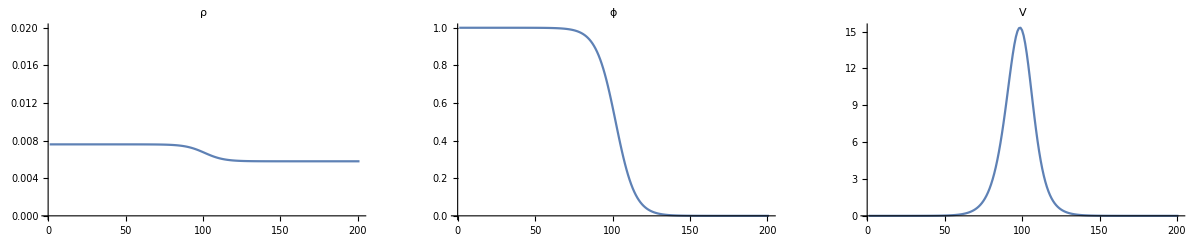

```mathematica
tplot= 1;
p1=ListPlot[ ρAll[[;;, tplot]], Joined-> True , PlotRange-> {Automatic, {0, 0.02}}, PlotLabel->"ρ", plotOptions];
p2=ListPlot[ ϕAll[[;;, tplot]], Joined-> True, PlotRange-> {Automatic, {0, 1}},PlotLabel->"ϕ",plotOptions];
p3=ListPlot[ VAll[[;;, tplot]], Joined-> True, PlotLabel->"V",plotOptions];
GraphicsRow[{p1,p2,p3}, ImageSize->Full]
(*Show[p1,p2,p3, PlotRange-> All]*)
```

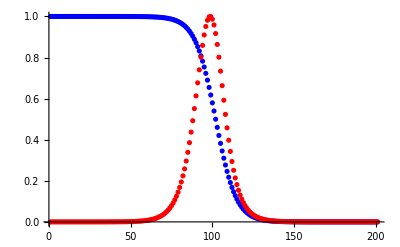

```mathematica
tplot= 1;
p1=ListPlot[ρAll[[;;,tplot]]/Max[ρAll[[;;,tplot]]], PlotStyle-> {Black} ];
p2=ListPlot[ϕAll[[;;,tplot]]/Max[ϕAll[[;;,tplot]]], PlotStyle-> {Blue} ];
p3=ListPlot[VAll[[;;,tplot]]/Max[VAll[[;;,tplot]]], PlotStyle-> {Red}, PlotRange->All ];
Show[ p2, p3, PlotRange-> All, AxesOrigin-> {0,0}]
```

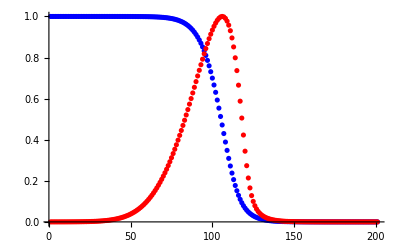

```mathematica
tplot= T;
p1=ListPlot[ρAll[[;;,tplot]]/Max[ρAll[[;;,tplot]]], PlotStyle-> {Black} ];
p2=ListPlot[ϕAll[[;;,tplot]]/Max[ϕAll[[;;,tplot]]], PlotStyle-> {Blue} ];
p3=ListPlot[VAll[[;;,tplot]]/Max[VAll[[;;,tplot]]], PlotStyle-> {Red}, PlotRange->All ];
Show[ p2, p3, PlotRange-> All, AxesOrigin-> {0,0}]
```

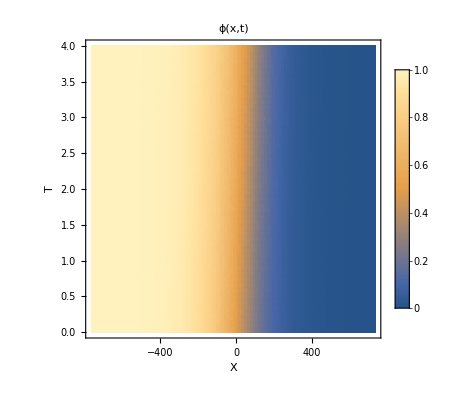

```mathematica
(* Zoom in *)
plotDataϕ=Flatten[Table[ {xmesh[[i]], tmesh[[j]], ϕAll[[i,j]]}, {i,Round[Nx/4],Round[Nx*3/4]}, {j,1, T+1}],1];pϕ=ListDensityPlot[plotDataϕ, PlotLabel-> "ϕ(x,t)", FrameLabel->{"X", "T"}, PlotLegends->Automatic ,PlotRange->All]
```

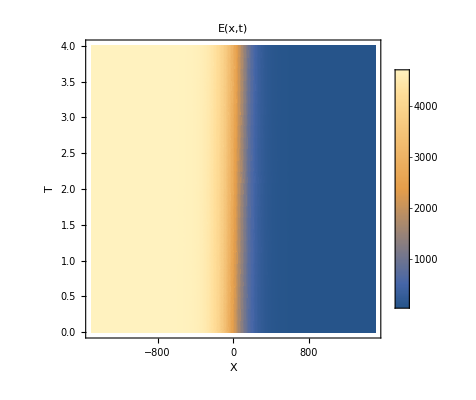

```mathematica
(*Stiffness *)
plotDataE=Flatten[Table[ {xmesh[[i]], tmesh[[j]],(eM(1-ϕAll[[i,j]])+eO ϕAll[[i,j]]) /. params}, {i,1, Nx+1}, {j,1, T+1}],1];ListDensityPlot[plotDataE, PlotLabel-> "E(x,t)", FrameLabel->{"X", "T"}, PlotLegends->Automatic ,PlotRange->All]
```

### Save data points for plots

```mathematica
(*OutNameRoot =FileNameJoin[{NotebookDirectory[], "Plots_model4b_FD_solver/", "simulation_set6_vary_viscosity/","data"}]
*)
OutNameRoot =FileNameJoin[{"/Users/dang/Documents/Projects/Tabler_skull/Scripts/Simulation_plots/Plots_model4b_FD_solver/simulation_set3_upwind/sim5/"}]
```

/Users/dang/Documents/Projects/Tabler_skull/Scripts/Simulation_plots/Plots_model4b_FD_solver/simulation_set3_upwind/sim5

```mathematica
allParams={eO,eM,η,ξ,τ,D1,α,ρdA,ρdB,ρh,aρ,a,"L","tmax","Nx","T"} ;
allValues=allParams /. params /. {"L"-> L, "tmax"-> tmax, "Nx"-> Nx, "T"-> T};
allParamsOut =Transpose[{allParams, allValues}];
```

```mathematica
(* Export parameters*)
(*AllParams=Join[ params, {"L"-> L, "tmax"-> tmax, "Nx"-> Nx, "T"-> T, "Dirichlet Boundaries"}]*)
allParams={eO,eM,η,ξ,τ,D1,α,ρdA,ρdB,ρh,aρ,a,"L","tmax","Nx","T"} ;
allValues=allParams /. params /. {"L"-> L, "tmax"-> tmax, "Nx"-> Nx, "T"-> T};
allParamsOut =Transpose[{allParams, allValues}];
Export[StringJoin[OutNameRoot, "data_parameters.csv"], allParamsOut, "csv"]
```

/Users/dang/Documents/Projects/Tabler_skull/Scripts/Simulation_plots/Plots_model4b_FD_solver/simulation_set6_vary_viscositydata_parameters.csv

```mathematica
(*dataSave =Map[DecimalForm[#, dec]&, N[ρAll, dec], {2}];*)
Clear[dataSave];dataSave = N[ρAll]// TableForm;
Export[StringJoin[OutNameRoot, "data_rho_1.csv"], dataSave, "CSV"]
Clear[dataSave];dataSave = N[ϕAll]// TableForm;
Export[StringJoin[OutNameRoot, "data_phi_1.csv"], dataSave, "CSV"]
Clear[dataSave];dataSave =N[VAll] // TableForm;
Export[StringJoin[OutNameRoot, "data_V_1.csv"], dataSave, "CSV"]
```

/Users/dang/Documents/Projects/Tabler_skull/Scripts/Simulation_plots/Plots_model4b_FD_solver/simulation_set3_upwind/sim5data_rho_1.csv

/Users/dang/Documents/Projects/Tabler_skull/Scripts/Simulation_plots/Plots_model4b_FD_solver/simulation_set3_upwind/sim5data_phi_1.csv

/Users/dang/Documents/Projects/Tabler_skull/Scripts/Simulation_plots/Plots_model4b_FD_solver/simulation_set3_upwind/sim5data_V_1.csv

Save plots
Needs improvement...

```mathematica
(*fileOut =FileNameJoin[{NotebookDirectory[], "Plots_model4b_FD_solver/", "simulation_set6_vary_viscosity/","plot"}];*)
Export[StringJoin[OutNameRoot, "plot_rho_1.eps"], pρ, "EPS"]
Export[StringJoin[OutNameRoot, "plot_phi_1.eps"], pϕ, "EPS"]
Export[StringJoin[OutNameRoot, "plot_V_1.eps"], pV, "EPS"]
(*Export[StringJoin[fileOut, "_200dpi.png"], pρ, "PNG", ImageResolution-> 200] ugly *)
```

/Users/dang/Documents/Projects/Tabler_skull/Scripts/Simulation_plots/Plots_model4b_FD_solver/simulation_set3_upwind/sim5plot_rho_1.eps

/Users/dang/Documents/Projects/Tabler_skull/Scripts/Simulation_plots/Plots_model4b_FD_solver/simulation_set3_upwind/sim5plot_phi_1.eps

/Users/dang/Documents/Projects/Tabler_skull/Scripts/Simulation_plots/Plots_model4b_FD_solver/simulation_set3_upwind/sim5plot_V_1.eps

## Plot average interface position

According to position of ϕ

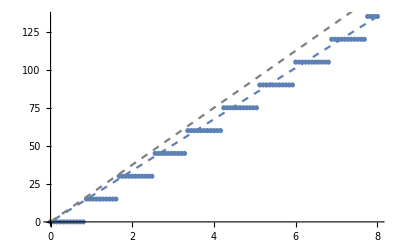

```mathematica
indices=Flatten@Map[ FirstPosition[#, True]&, Transpose@Map[  (#<0.5)&, ϕAll, {2}  ]];
positions = Map[ xmesh[[#]]&, indices]-xmesh[[indices[[1]]]];

p1=ListPlot[ Transpose[{tmesh, positions}] ];
p2=ListPlot[{{tmesh[[-1]], positions[[-1]]}, {tmesh[[1]],  positions[[1]]}}, Joined-> True, PlotStyle->Dashed];
(*p3=ListPlot[{{0, 0}, {4, 75}}, Joined-> True, PlotStyle->{Dashed, Gray}]; *)
p3=Plot[75/4 x,{x,0,T}, PlotStyle->{Dashed, Gray}];(*experiments est.*)
Show[p1,p2, p3]
```

According to position of V (peak)

```mathematica
indices2=Flatten@Table[ Position[ VAll[[;;,ti]], Max@VAll[[;;,ti]] ], {ti, 1, T+1}];
positions2 = Map[ xmesh[[#]]&, indices2]-xmesh[[indices2[[1]]]];
```

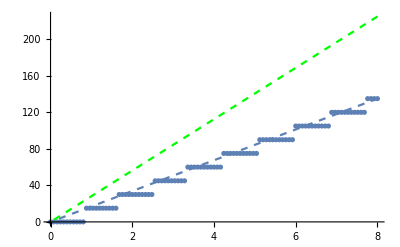

```mathematica
p1=ListPlot[ Transpose[{tmesh, positions}] ];
p2=ListPlot[{{tmesh[[-1]], positions[[-1]]}, {tmesh[[1]],  positions[[1]]}}, Joined-> True, PlotStyle->Dashed];
p2b=ListPlot[{{tmesh[[-1]], positions2[[-1]]}, {tmesh[[1]],  positions2[[1]]}}, Joined-> True, PlotStyle->{Green,Dashed}];
(*p3=ListPlot[{{0, 0}, {4, 75}}, Joined-> True, PlotStyle->{Dashed, Gray}]; *)
p3=Plot[75/4 x,{x,0,T}, PlotStyle->{Dashed, Gray}];(*experiments est.*)
Show[p1,p2,p2b, PlotRange-> Full]
```

## Compare two conditions

```mathematica
plotOptions = {ImageSize-> Large,PerformanceGoal-> "Quality",PlotLegends->Automatic,PlotRange->All, PlotLegends->Placed[BarLegend[Automatic],Right],ImageSize->Small,TicksStyle->Large,LabelStyle->{FontFamily->"Arial",FontSize->18,GrayLevel[0]}}
```

{ImageSize→Large,PerformanceGoal→Quality,PlotLegends→Automatic,PlotRange→All,PlotLegends→Placed[BarLegend[Automatic],Right],ImageSize→Small,TicksStyle→Large,LabelStyle→{FontFamily→Arial,FontSize→18,GrayLevel[0]}}

```mathematica
tplot= 1;
p1=ListPlot[Transpose[{xmesh, ρAll[[;;,tplot]]/Max[ρAll[[;;,tplot]]] }], PlotStyle-> {Black} , Joined->True ];
p2=ListPlot[Transpose[{xmesh, ϕAll[[;;,tplot]]/Max[ϕAll[[;;,tplot]]] }], PlotStyle-> {Blue}, Joined->True ];
p3=ListPlot[Transpose[{xmesh, VAll[[;;,tplot]]/Max[VAll[[;;,tplot]]] }], PlotStyle-> {Red}, Joined->True, PlotRange-> All];

p12=ListPlot[ Transpose[{xmesh, ρAll2[[;;,tplot]]/Max[ρAll2[[;;,tplot]]] }], PlotStyle-> {Black, Dashed} , Joined->True];
p22=ListPlot[ Transpose[{xmesh, ϕAll2[[;;,tplot]]/Max[ϕAll2[[;;,tplot]]] }], PlotStyle-> {Blue, Dashed} , Joined->True];
p32=ListPlot[ Transpose[{xmesh, VAll2[[;;,tplot]]/Max[VAll2[[;;,tplot]]] }], PlotStyle-> {Red, Dashed}, Joined->True, PlotRange-> All];
ListPlot[VAll[[;;,tplot]], PlotStyle-> {Red}, PlotRange->All ];
Show[ p2, p3, p22, p32, PlotRange-> All, AxesOrigin-> {0,0}, Frame-> True, FrameLabel-> {"x (μm)"}, plotOptions]
```

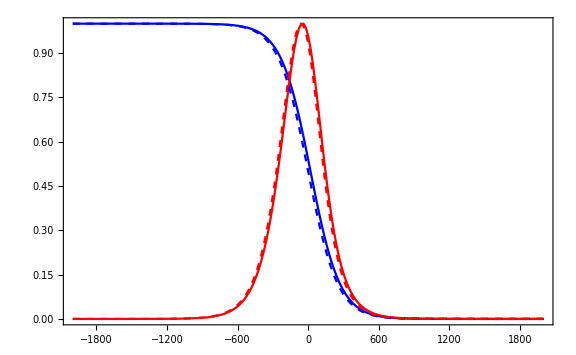

```mathematica
(* Plot velocities together *)
indicesϕ=Flatten@Map[ FirstPosition[#, True]&, Transpose@Map[  (#<0.5)&, ϕAll, {2}  ]];
positionsϕ = Map[ xmesh[[#]]&, indices]-xmesh[[indices[[1]]]];
indicesV=Flatten@Table[ Position[ VAll[[;;,ti]], Max@VAll[[;;,ti]] ], {ti, 1, T+1}];
positionsV = Map[ xmesh[[#]]&, indices2]-xmesh[[indices2[[1]]]];

indicesϕ2=Flatten@Map[ FirstPosition[#, True]&, Transpose@Map[  (#<0.5)&, ϕAll2, {2}  ]];
positionsϕ2 = Map[ xmesh2[[#]]&, indices]-xmesh2[[indices[[1]]]];
indicesV2=Flatten@Table[ Position[ VAll2[[;;,ti]], Max@VAll2[[;;,ti]] ], {ti, 1, T+1}];
positionsV2 = Map[ xmesh2[[#]]&, indices2]-xmesh[[indices2[[1]]]];
```

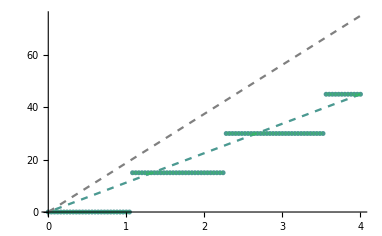

```mathematica
p1ϕ=ListPlot[ Transpose[{tmesh, positionsϕ}] ];
p2ϕ=ListPlot[{{tmesh[[-1]], positionsϕ[[-1]]}, {tmesh[[1]],  positionsϕ[[1]]}}, Joined-> True, PlotStyle->Dashed];
p1ϕ2=ListPlot[ Transpose[{tmesh2, positionsϕ2}], PlotStyle->{Green, Opacity[0.2]} ];
p2ϕ2=ListPlot[{{tmesh2[[-1]], positionsϕ2[[-1]]}, {tmesh2[[1]],  positionsϕ2[[1]]}}, Joined-> True, PlotStyle->{Green, Dashed, Opacity[0.2]}];
p3=Plot[75/4 x,{x,0,tmax}, PlotStyle->{Dashed, Gray}];(*experiments est.*)
Show[p1,p2,p12,p22, p3, PlotRange-> Full]
```

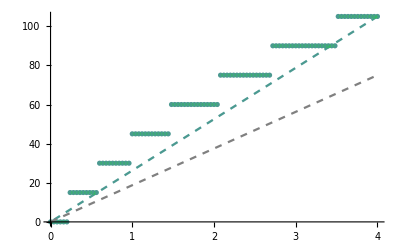

```mathematica
p1V=ListPlot[ Transpose[{tmesh, positionsV}] ];
p2V=ListPlot[{{tmesh[[-1]], positionsV[[-1]]}, {tmesh[[1]],  positionsV[[1]]}}, Joined-> True, PlotStyle->Dashed];
p1V2=ListPlot[ Transpose[{tmesh2, positionsV2}], PlotStyle->{Green, Opacity[0.2]} ];
p2V2=ListPlot[{{tmesh2[[-1]], positionsV2[[-1]]}, {tmesh2[[1]],  positionsV2[[1]]}}, Joined-> True, PlotStyle->{Green, Dashed, Opacity[0.2]}];
p3=Plot[75/4 x,{x,0,tmax}, PlotStyle->{Dashed, Gray}];(*experiments est.*)
Show[p1V,p2V,p1V2,p2V2, p3, PlotRange-> Full]
```

## Integrate single-cell trajectories

### Plot velocity profile

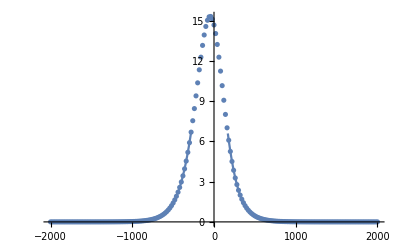

```mathematica
(* Interpolation function*)
idx =1;
dataTmp =Transpose[{xmesh, VAll[[;;, idx]]}];
InterpolationV =Interpolation[ dataTmp, InterpolationOrder->1];
p1=ListPlot[dataTmp ];
p2=Plot[InterpolationV[x], {x, -L , L}];
Show[p1, p2, PlotRange-> All]
```

### Simulate 1 cell

Initial positions to take: 0, -200, -400 μm, corresponding to the locations of the tracked cells

```mathematica
(*folder for saving*)
RootFolder="/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/simulation_set6_vary_viscosity/"
```

/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/simulation_set6_vary_viscosity/

```mathematica
(*Settings*)
IntOrder=1; (*interpolation order*)
xCell0List = {0, -200, -400};
(*sim=1;*)

xCellAllAll = {};
vCellAllAll = {};

For[sim=1, sim< 4,sim++,
Print[sim];

(* interpolation func*)
xCell0 = xCell0List[[sim]]; (*initial position of tracked cell*)
tIdx =1;
dataTmp =Transpose[{xmesh, VAll[[;;, tIdx]]}];
InterpolationV0 =Interpolation[ dataTmp, InterpolationOrder->IntOrder];
vCell0=InterpolationV0[xCell0];
xCellAll={xCell0};
vCellAll={vCell0};
For[tIdx=2, tIdx≤ T+1, tIdx++,
xCellTmp = xCellAll[[-1]];
vCellTmp=vCellAll[[-1]];
xCellNew =xCellTmp+vCellTmp*ΔtSet;

(* define new interpolation func*)
dataTmp =Transpose[{xmesh, VAll[[;;, tIdx]]}];
InterpolationVTmp =Interpolation[ dataTmp, InterpolationOrder->IntOrder];
vCellNew = InterpolationVTmp[xCellNew];

(* add results to lists *)
AppendTo[xCellAll, xCellNew];
AppendTo[vCellAll, vCellNew];
];

(* Save results *)
AppendTo[xCellAllAll, xCellAll];
AppendTo[vCellAllAll, vCellAll];


settingsToSave={{"xCell0", xCell0},{"IntOrder", IntOrder}};
Export[FileNameJoin[{RootFolder, StringJoin["1cell_sim",ToString[sim],"_xCellAll.csv"]}], xCellAll, "CSV"];
Export[FileNameJoin[{RootFolder, StringJoin["1cell_sim",ToString[sim],"_vCellAll.csv"]}], vCellAll, "CSV"];
Export[FileNameJoin[{RootFolder, StringJoin["1cell_sim",ToString[sim],"_settings.csv"]}], settingsToSave, "CSV"];

]
```

1

2

3

```mathematica
(*
ListPlot[Transpose[{tmesh,xCellAll }] ]
ListPlot[Transpose[{tmesh,vCellAll }] ]
*)
```

```mathematica
(* For troubleshooting *)
(*
tIdx=2;
xCellTmp=xCellAll[[-1]];
vCellTmp=vCellAll[[-1]];
xCellNew=xCellTmp+vCellTmp*ΔtSet;
(* define new interpolation func*)
dataTmp=Transpose[{xmesh, VAll[[tIdx,;;]]}];
InterpolationVTmp=Interpolation[ dataTmp, InterpolationOrder->IntOrder];
vCellNew=InterpolationVTmp[xCellNew];
*)
```

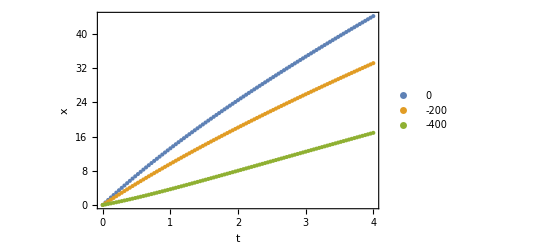

```mathematica
ListPlot[ Table[ Transpose[{tmesh, xCellAllAll[[i,;;]]-xCell0List[[i]]  }], {i, 1, 3}  ],PlotLegends->{ToString/@xCell0List}, Frame-> True, FrameLabel-> {"t", "x"} ]
```

## Systematically calculate v for range of parameter values

### Theoretical front velocity

Note: the front velocity for a pulled wave is approximately
	v_F = (D(k_B-k_A) + α(E_B-E_A))^(1/2) + v_A
Problem: k_A, k_B not constant. Approximate as (k_A+k_B)/2.

```mathematica
params
```

{eO→4700,eM→200,η→25/9,ξ→1.30556,τ→10,D1→15,α→1/50000,ρdA→0.0058,ρdB→0.0076,aρ→4,a→4,ρh→1/200,f→0}

```mathematica
Sqrt[D1(kB-kA) + α (eO-eM)] /. {ρ[x,t]-> (ρdA+ρdB)/2}/.params
```

0.707383

### Calculate Δϕ

Numerically solve for wave velocity by shifting the profile ϕ[x, t] to ϕ[x + v δt, t + δt] and finding v for which the difference | ϕ[x, t] - ϕ[x + v δt, t + δt] | is minimized. 
Do for a range of values of t (denoted t1), but only one δt should be sufficient.

Boundaries: -L <= xp+vp δt <= L, so xp <= L - vp δt, so need to set this as integral / sum upper bound

```mathematica
(* quick calculation, without multiple T*)
(*
t1=20;
δt=10;
vpList=Range[0, 2*δt]/δt;
ΔϕFull=Sum@Table[
Sum[ (ϕAll[[x,t1 ]]-ϕAll[[x+vpList[[vj]] δt, t1+δt]] ), 
{x, 1, Nx-vpList[[vj]] δt}],
{vj, 1, Length[vpList]}
];
*)
```

```mathematica
T
```

100

```mathematica
Nx
```

200

```mathematica
(*Numerically test across a range of values for t and v*)
T1=20;δt=30;
t1All = Range[T1, T-δt, δt]; (* set time range*)
t1len= Length@t1All;
vpList=Range[0, 0.5*δt]/δt;
```

```mathematica
(*Test *)
(*(ϕAll[[x, t]]-ϕAll[[x+vp dt, t+dt]] )/.{x-> Nx/2, t-> T/2, vp-> vpList[[1]],dt -> 10}*)
```

Note: smallest possible difference in v testable is ΔxSet/δt, as the mesh size ΔxSet is fixed.
Testable difference in V (μm/hr):

```mathematica
N[ΔxSet/δt]
```

0.666667

```mathematica
Module[{dt = δt},
ΔϕFull=Abs[
Table[
Sum[ (ϕAll[[x, t1All[[tj]] ]]-ϕAll[[x+vpList[[vj]] dt, t1All[[tj]]+dt]] ), {x, 1, Nx-vpList[[vj]] dt}],
{tj, 1, t1len}, {vj, 1, Length[vpList]}
]
];
]
(*ΔϕFull=Table[  NIntegrate[Abs[((ϕsol/.{t->t1, x->xp})-(ϕsol/.{t->t1+δt, x->xp+vp δt} ) )] /.{x->xp} , {xp, -L, L-vp δt}, MaxRecursion->12],  {t1, t1All[[1]], t1All[[-1]], δt }, {vp, vpList[[1]], vpList[[-1]], δvp}];*)
```

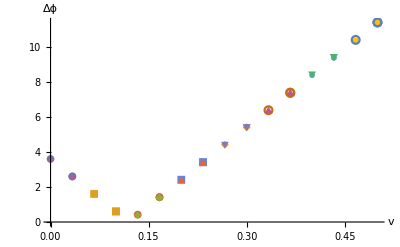

```mathematica
t1temp=ConstantArray[vpList, t1len] ;
plotdata=Partition[  Transpose[ {Flatten@t1temp, Flatten@ΔϕFull} ] , t1len];hplot=ListPlot[plotdata, Frame->False, PlotMarkers->{Automatic, 8},AxesLabel->{Style["v",Black, FontSize-> 20],Style["Δϕ", Black,FontSize-> 20] }, TicksStyle->Directive[Black,16]]
```

```mathematica
(* Save plot *)
fnameOut=StringJoin["/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/simulation_set4_try_kD_profiles/","calculate_v_from_del_phi.eps"];
(*fnameOut=StringJoin[NotebookDirectory[] , "Velocity_data/", "del_phi_convergence_kF_", ToString[kF /. params],"_sM_30_sO_", ToString[sO /. params],"_epsphi_", ToString[ϵϕ],".eps"];*)
(*Export[fnameOut, hplot, "EPS"]*)
```

#### Find optimal v

```mathematica
(*Find minima of Δϕ for each t1*)
findmin=Position[#,Min[#]]&;
ϕminPos=Flatten[findmin/@ΔϕFull];
vValsϕmin = vpList[[ ϕminPos ]] (*values of velocity where the difference is minimal *)
```

{2/15,2/15}

```mathematica
(*Find minimal distance averaged over all t1*)
Δϕavg=Mean[ΔϕFull];
vInferred =vpList[[ Sequence@@First@findmin[Δϕavg] ]]  (* "optimal v" *)
```

2/15

```mathematica
ΔϕInferred= Δϕavg[[ Sequence@@First@findmin[Δϕavg] ]]
```

0.407455

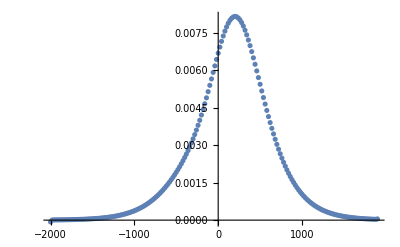

```mathematica
(* Plot difference between profiles given a certain shift *)
Module[{t1 = T1,dt = δt},
xvals = Table[xmesh[[xj]], {xj, 1, Nx-vInferred dt}];
δvals=Table[ϕAll[[x, t1 ]]-ϕAll[[x+vInferred dt, t1+dt]], {x, 1, Nx-vInferred dt}];
]
p1=ListPlot[Transpose[{xvals, δvals}],PlotRange-> All,PlotLegends->"Δϕ"]
```

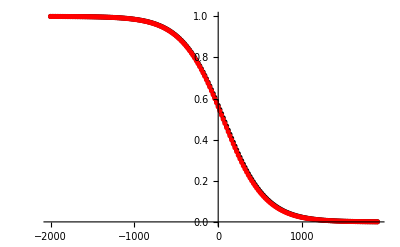

```mathematica
(* Plot both profiles given a certain shift *)
Module[{t1 = T1,dt = δt},
xvals = Table[xmesh[[xj]], {xj, 1, Nx-vInferred dt}];
ϕ1vals=Table[ϕAll[[x, t1 ]], {x, 1, Nx-vInferred dt}];
ϕ2vals=Table[ϕAll[[x+vInferred dt, t1+dt]], {x, 1, Nx-vInferred dt}];
]

p1=ListPlot[Transpose[{xvals, ϕ1vals}],PlotRange-> All,PlotLegends->"ϕ1", PlotStyle-> {Black}];
p2=ListPlot[Transpose[{xvals, ϕ2vals}],PlotRange-> All,PlotLegends->"ϕ2", PlotStyle-> {Red}];
Show[p1,p2]
```

In units of μm/hr:

```mathematica
N[vInferred*ΔxSet/ΔtSet]
```

33.3333

### Width of ϕ profile

Obtain by simply setting thresholds ϕ_L≤ ϕ ≤ ϕ_H

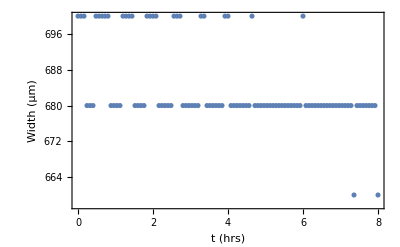

```mathematica
ϕL=0.2; ϕH=0.8;
ϕMid=Boole@Map[(ϕL<#)&& (#<ϕH)&,ϕAll, {2}];
AllWidths=Total[ϕMid]*ΔxSet;

ϕwidth = Mean[ AllWidths[[Round[T/2];;]] ];
ListPlot[ Transpose[{tmesh,AllWidths}] , Frame-> True, FrameLabel->{"t (hrs)", "Width (μm)"}]
```

```mathematica
N[ϕwidth]
```

680.769

### Organize data together and save

Save parameters + inferred v + error Δϕ

```mathematica
params
```

{eO→4700,eM→200,η→25/9,ξ→1.30556,τ→10,D1→15,α→1/50000,ρdA→0.0058,ρdB→0.0076,aρ→4,a→4,ρh→1/200,f→0}

```mathematica
(*vars={{τ,ρdA,ρdB,ρh},{D1,α,kF},{fc,ξ,χ,η,κ},{sM,sO,a,τs}};*)
vars = {eO,eM,η,ξ,τ,D1,α,ρdA,ρdB,aρ,a,ρh};
varsVals=Map[Replace[#, Flatten@params]&,vars, 2]
```

{4700,200,25/9,1.30556,10,15,1/50000,0.0058,0.0076,4,4,1/200}

deltavUnits:

```mathematica
(*varsOut=ToString/@{{tau,rhoA,rhoB,rhoh},{D1,alpha,kDiff},{fc,xi,chi,eta,kappa},{sM,sO,a,taus},{"xmin", "xmax", "tmax", "deltat", "deltavp"},{"vInferred", "DeltaphiInferred"}}*)
varsOut=ToString/@{{eO,eM,eta,xi,tau,D1,alpha,rhodA,rhodB,aRho,a,rhoh},{"xmin", "xmax", "tmax", "deltat", "deltavUnits"},{"vInferred", "DeltaphiInferred", "vInferredMicrons", "phiWidthMicrons"}}
varsValsOut=N/@Join[varsVals,{{-L,L,tmax,δt,ΔxSet/δt}},{{vInferred, ΔϕInferred, vInferred*ΔxSet/ΔtSet, ϕwidth}}]
```

{{eO, eM, eta, xi, tau, D1, alpha, rhodA, rhodB, aRho, a, rhoh},{xmin, xmax, tmax, deltat, deltavUnits},{vInferred, DeltaphiInferred, vInferredMicrons, phiWidthMicrons}}

{4700.,200.,2.77778,1.30556,10.,15.,0.00002,0.0058,0.0076,4.,4.,0.005,{-2000.,2000.,8.,30.,0.666667},{0.133333,0.407455,33.3333,680.769}}

```mathematica
(*fnameOut=StringJoin[NotebookDirectory[] , "Velocity_data/", "vdata_kF_", ToString[kF /. params],"_sM_30_sO", ToString[sO /. params],"_es_", ToString[ϵs],"_epsphi_", ToString[ϵϕ],"_t20.csv"]*)
fnameOut=StringJoin["/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/", "simulation_set3/", "velocity_data.csv"] 
(*Export[fnameOut, {varsOut,varsValsOut}, "CSV"]*)
```

/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/simulation_set3/velocity_data.csv

## Compare multiple simulations

#### Load data

```mathematica
(* Load data*)
LoadFolder = "/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/simulation_set4_try_kD_profiles/0_constant/data";
ρAll0=Import[StringJoin[LoadFolder, "_rho_1.csv"]];
ϕAll0=Import[StringJoin[LoadFolder, "_phi_1.csv"]];
VAll0=Import[StringJoin[LoadFolder, "_V_1.csv"]];
params0 = Import[StringJoin[LoadFolder, "_parameters.csv"]];

(* Load data*)
LoadFolder = "/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/simulation_set4_try_kD_profiles/1_linear/data";
ρAll1=Import[StringJoin[LoadFolder, "_rho_1.csv"]];
ϕAll1=Import[StringJoin[LoadFolder, "_phi_1.csv"]];
VAll1=Import[StringJoin[LoadFolder, "_V_1.csv"]];
params1 = Import[StringJoin[LoadFolder, "_parameters.csv"]];

(* Load data*)
LoadFolder = "/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/simulation_set4_try_kD_profiles/2_sigmoidal/data";
ρAll2=Import[StringJoin[LoadFolder, "_rho_1.csv"]];
ϕAll2=Import[StringJoin[LoadFolder, "_phi_1.csv"]];
VAll2=Import[StringJoin[LoadFolder, "_V_1.csv"]];
params2 = Import[StringJoin[LoadFolder, "_parameters.csv"]];

(* Load data*)
LoadFolder = "/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/simulation_set4_try_kD_profiles/3_gaussian/data";
ρAll3=Import[StringJoin[LoadFolder, "_rho_1.csv"]];
ϕAll3=Import[StringJoin[LoadFolder, "_phi_1.csv"]];
VAll3=Import[StringJoin[LoadFolder, "_V_1.csv"]];
params3 = Import[StringJoin[LoadFolder, "_parameters.csv"]];

(* Load data*)
LoadFolder = "/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/simulation_set4_try_kD_profiles/3b_gaussian_shifted_left/data";
ρAll3b=Import[StringJoin[LoadFolder, "_rho_1.csv"]];
ϕAll3b=Import[StringJoin[LoadFolder, "_phi_1.csv"]];
VAll3b=Import[StringJoin[LoadFolder, "_V_1.csv"]];
params3b = Import[StringJoin[LoadFolder, "_parameters.csv"]];

(* Load data*)
LoadFolder = "/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/simulation_set4_try_kD_profiles/3c_gaussian_shifted_right/data";
ρAll3c=Import[StringJoin[LoadFolder, "_rho_1.csv"]];
ϕAll3c=Import[StringJoin[LoadFolder, "_phi_1.csv"]];
VAll3c=Import[StringJoin[LoadFolder, "_V_1.csv"]];
params3c = Import[StringJoin[LoadFolder, "_parameters.csv"]];
```

Common parameters

```mathematica
(*params={eO-> 1000, eM-> 30, η-> 25/9, ξ-> 5/18, τ-> 10, D1->1000, α-> 1/1000, ρdA-> 5.8*10^(-3), ρdB->7.6*10^(-3), ρh->1*10^(-3), aρ-> 8,a->8}; *)
L=1500;
tmax=8;
Nx = 100;
T=100;
```

```mathematica
(* Define mesh *)
ΔxSet = 2L/(Nx);
ΔtSet = tmax/T;
xmesh= Range[-L, L, ΔxSet];
tmesh =Range[0, tmax, tmax/T];
```

#### Plot results

```mathematica
plotOptions = {ImageSize-> Small,PerformanceGoal-> "Quality",PlotLegends->Automatic,PlotRange->All, PlotLegends->Placed[BarLegend[Automatic],Right],ImageSize->Small,TicksStyle->Large,LabelStyle->{FontFamily->"Arial",FontSize->14,GrayLevel[0]},AspectRatio->Full}
```

{ImageSize→Small,PerformanceGoal→Quality,PlotLegends→Automatic,PlotRange→All,PlotLegends→Placed[BarLegend[Automatic],Right],ImageSize→Small,TicksStyle→Large,LabelStyle→{FontFamily→Arial,FontSize→14,GrayLevel[0]},AspectRatio→Full}

```mathematica
plotDataϕ0=Flatten[Table[ {xmesh[[i]],tmesh[[j]],ϕAll0[[i,j]]}, {i,1,Nx+1}, {j,1,T+1}],1];
pϕ0=ListDensityPlot[plotDataϕ0, PlotLabel-> "ϕ(x,t)", FrameLabel->{"X", "T"}, plotOptions];
plotDataϕ1=Flatten[Table[ {xmesh[[i]],tmesh[[j]],ϕAll1[[i,j]]}, {i,1,Nx+1}, {j,1,T+1}],1];
pϕ1=ListDensityPlot[plotDataϕ1, PlotLabel-> "ϕ(x,t)", FrameLabel->{"X", "T"}, plotOptions];
plotDataϕ2=Flatten[Table[ {xmesh[[i]],tmesh[[j]],ϕAll2[[i,j]]}, {i,1,Nx+1}, {j,1,T+1}],1];
pϕ2=ListDensityPlot[plotDataϕ2, PlotLabel-> "ϕ(x,t)", FrameLabel->{"X", "T"}, plotOptions];
plotDataϕ3=Flatten[Table[ {xmesh[[i]],tmesh[[j]],ϕAll3[[i,j]]}, {i,1,Nx+1}, {j,1,T+1}],1];
pϕ3=ListDensityPlot[plotDataϕ3, PlotLabel-> "ϕ(x,t)", FrameLabel->{"X", "T"}, plotOptions];
plotDataϕ3b=Flatten[Table[ {xmesh[[i]],tmesh[[j]],ϕAll3b[[i,j]]}, {i,1,Nx+1}, {j,1,T+1}],1];
pϕ3b=ListDensityPlot[plotDataϕ3, PlotLabel-> "ϕ(x,t)", FrameLabel->{"X", "T"}, plotOptions];
plotDataϕ3c=Flatten[Table[ {xmesh[[i]],tmesh[[j]],ϕAll3c[[i,j]]}, {i,1,Nx+1}, {j,1,T+1}],1];
pϕ3c=ListDensityPlot[plotDataϕ3, PlotLabel-> "ϕ(x,t)", FrameLabel->{"X", "T"}, plotOptions];
AllPlots=GraphicsRow[{pϕ0, pϕ1,pϕ2, pϕ3},ImageSize->Full,ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}} ]
AllPlots=GraphicsRow[{pϕ3, pϕ3b, pϕ3c},ImageSize->Full,ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}} ]
```

-Graphics-

-Graphics-

#### Plot profiles at fixed time

```mathematica
plotOptions = {ImageSize-> Medium,PerformanceGoal-> "Quality",PlotLegends->Automatic,PlotRange->All,TicksStyle->Large,LabelStyle->{FontFamily->"Arial",FontSize->10,GrayLevel[0]}}
```

{ImageSize→Medium,PerformanceGoal→Quality,PlotLegends→Automatic,PlotRange→All,TicksStyle→Large,LabelStyle→{FontFamily→Arial,FontSize→10,GrayLevel[0]}}

```mathematica
tplot= T;
pρ0=ListPlot[Transpose[{xmesh,ρAll0[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Blue, Opacity[0.5]}];
pϕ0=ListPlot[Transpose[{xmesh,ϕAll0[[;;, tplot]]}], Joined-> True,plotOptions, PlotStyle->{Blue, Opacity[0.5]}];
pV0=ListPlot[Transpose[{xmesh,VAll0[[;;, tplot]] }], Joined-> True, plotOptions, PlotStyle->{Blue, Opacity[0.5]}];

pρ1=ListPlot[Transpose[{xmesh,ρAll1[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Blue, Opacity[0.5]}];
pϕ1=ListPlot[Transpose[{xmesh,ϕAll1[[;;, tplot]]}], Joined-> True,plotOptions, PlotStyle->{Blue, Opacity[0.5]}];
pV1=ListPlot[Transpose[{xmesh,VAll1[[;;, tplot]] }], Joined-> True, plotOptions, PlotStyle->{Blue, Opacity[0.5]}];

pρ2=ListPlot[Transpose[{xmesh, ρAll2[[;;, tplot]]}], Joined-> True,  plotOptions, PlotStyle->{Red, Opacity[0.5]}];
pϕ2=ListPlot[ Transpose[{xmesh,ϕAll2[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Red, Opacity[0.5]}];
pV2=ListPlot[ Transpose[{xmesh,VAll2[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Red, Opacity[0.5]}];

pρ3=ListPlot[ Transpose[{xmesh,ρAll3[[;;, tplot]]}], Joined-> True,  plotOptions, PlotStyle->{Black, Opacity[0.5]}];
pϕ3=ListPlot[ Transpose[{xmesh,ϕAll3[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Black, Opacity[0.5]}];
pV3=ListPlot[ Transpose[{xmesh,VAll3[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Black, Opacity[0.5]}];

pρ3b=ListPlot[ Transpose[{xmesh,ρAll3b[[;;, tplot]]}], Joined-> True,  plotOptions, PlotStyle->{Red, Opacity[0.5]}];
pϕ3b=ListPlot[ Transpose[{xmesh,ϕAll3b[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Red, Opacity[0.5]}];
pV3b=ListPlot[ Transpose[{xmesh,VAll3b[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Red, Opacity[0.5]}];

pρ3c=ListPlot[ Transpose[{xmesh,ρAll3c[[;;, tplot]]}], Joined-> True,  plotOptions, PlotStyle->{Green, Opacity[0.5]}];
pϕ3c=ListPlot[ Transpose[{xmesh,ϕAll3c[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Green, Opacity[0.5]}];
pV3c=ListPlot[ Transpose[{xmesh,VAll3c[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Green, Opacity[0.5]}];
```

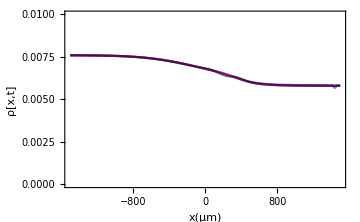

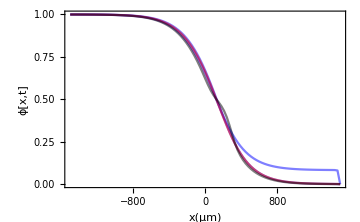

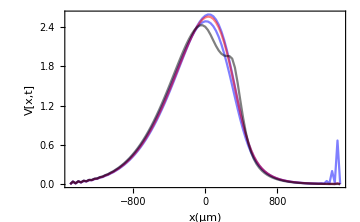

```mathematica
Show[pρ0, pρ1,pρ2,pρ3,PlotRange->{Automatic, {0, 0.01}}, AxesOrigin-> {0,0}, Frame-> True, FrameLabel->{"x(μm)", "ρ[x,t]"}]
Show[pϕ0, pϕ1,pϕ2,pϕ3,PlotRange-> All, Frame-> True, FrameLabel->{"x(μm)", "ϕ[x,t]"}]
Show[pV0, pV1,pV2,pV3,PlotRange-> All, Frame-> True, FrameLabel->{"x(μm)", "V[x,t]"}]
```

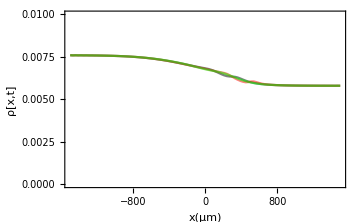

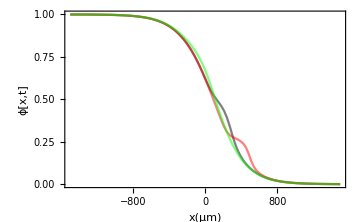

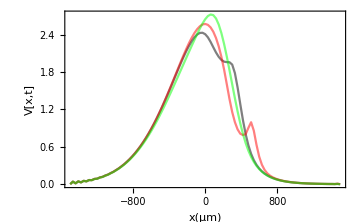

```mathematica
Show[pρ3,pρ3b,pρ3c,PlotRange->{Automatic, {0, 0.01}}, AxesOrigin-> {0,0}, Frame-> True, FrameLabel->{"x(μm)", "ρ[x,t]"}]
Show[pϕ3,pϕ3b,pϕ3c,PlotRange-> All, Frame-> True, FrameLabel->{"x(μm)", "ϕ[x,t]"}]
Show[pV3,pV3b,pV3c,PlotRange-> All, Frame-> True, FrameLabel->{"x(μm)", "V[x,t]"}]
```

#### Plot difference between profiles

```mathematica
pρ21=ListPlot[Transpose[{xmesh, ρAll2[[;;, tplot]]-ρAll1[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Purple, Opacity[0.5]}];
pρ31=ListPlot[Transpose[{xmesh, ρAll3[[;;, tplot]]-ρAll1[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Black, Opacity[0.5]}];
pρ32=ListPlot[Transpose[{xmesh, ρAll3[[;;, tplot]]-ρAll2[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Orange, Opacity[0.5]}];
ϕρ21=ListPlot[Transpose[{xmesh, ϕAll2[[;;, tplot]]-ϕAll1[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Purple, Opacity[0.5]}];
ϕρ31=ListPlot[Transpose[{xmesh, ϕAll3[[;;, tplot]]-ϕAll1[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Black, Opacity[0.5]}];
ϕρ32=ListPlot[Transpose[{xmesh, ϕAll3[[;;, tplot]]-ϕAll2[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Orange, Opacity[0.5]}];
Vρ21=ListPlot[Transpose[{xmesh, VAll2[[;;, tplot]]-VAll1[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Purple, Opacity[0.5]}];
Vρ31=ListPlot[Transpose[{xmesh, VAll3[[;;, tplot]]-VAll1[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Black, Opacity[0.5]}];
Vρ32=ListPlot[Transpose[{xmesh, VAll3[[;;, tplot]]-VAll2[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Orange, Opacity[0.5]}];
```

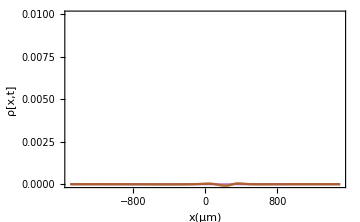

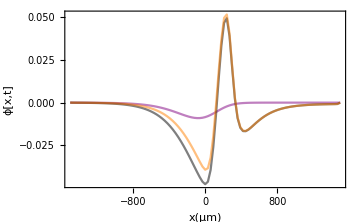

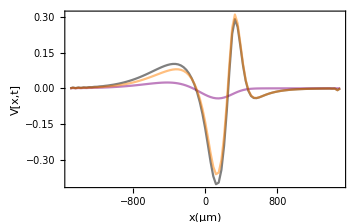

```mathematica
Show[pρ21,pρ31,pρ32,PlotRange->{Automatic, {0, 0.01}}, AxesOrigin-> {0,0}, Frame-> True, FrameLabel->{"x(μm)", "ρ[x,t]"}]
Show[ϕρ21,ϕρ31,ϕρ32, PlotRange-> All, Frame-> True, FrameLabel->{"x(μm)", "ϕ[x,t]"}]
Show[Vρ21,Vρ31,Vρ32, PlotRange-> All, Frame-> True, FrameLabel->{"x(μm)", "V[x,t]"}]
```

## Parameters and velocities

List of parameters and velocities.

```mathematica
(*Set 2a*)
params={eO-> 1000, eM-> 30, η-> 25/9, ξ-> 3/18, τ-> 10, D1->15, α-> 4*10^(-5), ρdA-> 5.8*10^(-3), ρdB->7.6*10^(-3), aρ->4,a->4,ρh->1*10^(-3)};
L=1500;
tmax=8;
vOut = 25;
```

```mathematica
(*Set 2b*)
params={eO-> 1000, eM-> 30, η-> 25/9, ξ-> 3/18, τ-> 10, D1->15, α-> 1*10^(-5), ρdA-> 5.8*10^(-3), ρdB->7.6*10^(-3), aρ->4,a->4,ρh->1*10^(-3)};
L=1500;
tmax=8;
vOut = 12.5;
```

```mathematica
(* set 4 *)
params={eO-> 1000, eM-> 30, η-> 25/9, ξ-> 5/18, τ-> 10, D1->15, α-> 2*10^(-5), ρdA-> 5.8*10^(-3), ρdB->7.6*10^(-3),aρ->4,a->4,ρh->5*10^(-3)};
L=1500;
tmax=8;
kD1:=α (e-eM);
kD2:=α eO  Tanh[(e-eM)/eO] /. params;
kD3:=0.02*Exp[-(e-(eO-eM)/2)^2/(2*((eO-eM)/8)^2)]
kD:=kD1
```

Part::partw: Part 16 of {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} does not exist.

Part::partw: Part 17 of {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} does not exist.

Part::partw: Part 18 of {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

Part::partw: Part 4 of 1;;All does not exist.

Part::partw: Part 5 of 1;;All does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListDensityPlot::nonopt: Options expected (instead of plotOptions) beyond position 1 in ListDensityPlot[<<3774339888 bytes>>]. An option must be a rule or a list of rules.

Part::take: Cannot take positions 1 through 12 in 1/2 (1+Tanh[8]).

ListDensityPlot::nonopt: Options expected (instead of plotOptions) beyond position 1 in ListDensityPlot[<<4049446240 bytes>>]. An option must be a rule or a list of rules.

Part::take: Cannot take positions 1 through 12 in 0.0076.

General::stop: Further output of Part::take will be suppressed during this calculation.

ListDensityPlot::nonopt: Options expected (instead of plotOptions) beyond position 1 in ListDensityPlot[<<3774339888 bytes>>]. An option must be a rule or a list of rules.

General::stop: Further output of ListDensityPlot::nonopt will be suppressed during this calculation.

$Aborted